```mathematica
tau = {0, 1};
n = {1, 0};
taux = {0, 1};
nx = {1, 0};
x = 0; 
s =Asymptotic[ u/Sqrt[1+h k]-((h kp) u^2)/(6 (1+h k)^2)+(((h^2 kp^2)/(18 (1+h k)^2)-(-3 k^2-6 h k^3-3 h^2 k^4-h^2 kp^2+3 h kpp+3 h^2 k kpp)/(72 (1+h k)^2)) u^3)/(1+h k)^(3/2),h->0,SeriesTermGoal->3]// ExpandAll;
sp = D[s,u];
kappa = k + s*kp + 1/2 s^2*kpp+ 1/6 s^3*kppp;
kappap = kp + s *kpp +1/2*s^2*kppp + O[u]^10;
sigma = sig + s*sigp + 1/2 s^2*sigpp+ O[u]^10;
y = s*tau - s^2/2*k*n-s^3/6*(kp*n+k^2*tau)+ s^4/24((-kpp+k^3)*n - 3*k*kp*tau);
r = x+h*nx-y;
r2 = h^2+u^2;
r4 = r2^2;
r6 = r2^3;
r8 = r2^4;
tauy = tau - s*k*n-s^2/2*(kp*n+k^2*tau)+s^3/6*((-kpp+k^3)*n-3*k*kp*tau);
ny = n + s*k*tau+s^2/2*(kp*tau - k^2*n)+s^3/6*((kpp-k^3)tau-3*k*kp*n);
Normal[Series[(r.nx)(r.tauy)(sp)(sigma),{h,0,4},{u,0,4}]]// ExpandAll
```

-h sig u-h sigp u^2+1/2 h^2 k sigp u^2-3/8 h^3 k^2 sigp u^2+5/16 h^4 k^3 sigp u^2-1/2 k sig u^3+1/2 h k^2 sig u^3-1/2 h^2 k^3 sig u^3+1/2 h^3 k^4 sig u^3+3/64 h^4 k^5 sig u^3+1/6 h^2 kp sigp u^3-1/3 h^3 k kp sigp u^3+1/2 h^4 k^2 kp sigp u^3-1/2 h sigpp u^3+1/2 h^2 k sigpp u^3-1/2 h^3 k^2 sigpp u^3+1/2 h^4 k^3 sigpp u^3-1/6 kp sig u^4+5/8 h k kp sig u^4-35/24 h^2 k^2 kp sig u^4+485/192 h^3 k^3 kp sig u^4-725/384 h^4 k^4 kp sig u^4-5/27 h^4 kp^3 sig u^4+5/24 h^3 kp kpp sig u^4-35/48 h^4 k kp kpp sig u^4-1/2 k sigp u^4+17/24 h k^2 sigp u^4-7/8 h^2 k^3 sigp u^4+65/64 h^3 k^4 sigp u^4-175/384 h^4 k^5 sigp u^4-5/72 h^3 kp^2 sigp u^4+35/144 h^4 k kp^2 sigp u^4+1/24 h^2 kpp sigp u^4-5/48 h^3 k kpp sigp u^4+35/192 h^4 k^2 kpp sigp u^4+1/6 h^2 kp sigpp u^4-5/12 h^3 k kp sigpp u^4+35/48 h^4 k^2 kp sigpp u^4

```mathematica
tau = {0, 1};
n = {1, 0};
taux = {0, 1};
nx = {1, 0};
x = 0; 
y = s*tau - s^2/2*k*n-s^3/6*(kp*n+k^2*tau)+ s^4/24((-kpp+k^3)*n - 3*k*kp*tau)+O[s]^5;
r = x+h*nx-y;
InverseSeries[r.r-h^2,u2]
```

(√u2)/(√(1+h k))-((h kp) u2)/(6 (1+h k)^2)+(((h^2 kp^2)/(18 (1+h k)^2)-(-3 k^2-6 h k^3-3 h^2 k^4-h^2 kp^2+3 h kpp+3 h^2 k kpp)/(72 (1+h k)^2)) u2^(3/2))/(1+h k)^(3/2)+O[u2]^2

```mathematica
(3/2(r.ny)+3(r.ny)(nx.ny)^2+3(r.nx)(nx.ny))(sp)*sigma+ O[u]^4// ExpandAll
```

((15 h sig)/2-15/4 h^2 k sig+45/16 h^3 k^2 sig-75/32 h^4 k^3 sig)+(-5/2 h^2 kp sig+5 h^3 k kp sig-15/2 h^4 k^2 kp sig+(15 h sigp)/2-15/2 h^2 k sigp+15/2 h^3 k^2 sigp-15/2 h^4 k^3 sigp+435/128 h^5 k^4 sigp-225/128 h^6 k^5 sigp+375/512 h^7 k^6 sigp) u+(-(3 k sig)/4-45/8 h k^2 sig+279/32 h^2 k^3 sig-705/64 h^3 k^4 sig+3465/256 h^4 k^5 sig-5229/512 h^5 k^6 sig+(14805 h^6 k^7 sig)/2048-(18423 h^7 k^8 sig)/4096+(14715 h^8 k^9 sig)/8192-(11775 h^9 k^10 sig)/16384+(3375 h^10 k^11 sig)/16384-15/4 h^2 kp sigp+75/8 h^3 k kp sigp-525/32 h^4 k^2 kp sigp+615/64 h^5 k^3 kp sigp-105/16 h^6 k^4 kp sigp+225/64 h^7 k^5 kp sigp+(15 h sigpp)/4-45/8 h^2 k sigpp+225/32 h^3 k^2 sigpp-525/64 h^4 k^3 sigpp+1575/256 h^5 k^4 sigpp-2205/512 h^6 k^5 sigpp+(5355 h^7 k^6 sigpp)/2048-(4275 h^8 k^7 sigpp)/4096+(3375 h^9 k^8 sigpp)/8192-(1875 h^10 k^9 sigpp)/16384) u^2+(-kp sig-17/4 h k kp sig+27/2 h^2 k^2 kp sig-107/4 h^3 k^3 kp sig+1507/32 h^4 k^4 kp sig-3025/64 h^5 k^5 kp sig+5463/128 h^6 k^6 kp sig-8563/256 h^7 k^7 kp sig+(73511 h^8 k^8 kp sig)/4096-(153307 h^9 k^9 kp sig)/16384+(16085 h^10 k^10 kp sig)/4096-(30225 h^11 k^11 kp sig)/32768+(19625 h^12 k^12 kp sig)/65536-(16875 h^13 k^13 kp sig)/262144-(3 k sigp)/4-21/4 h k^2 sigp+45/4 h^2 k^3 sigp-69/4 h^3 k^4 sigp+3081/128 h^4 k^5 sigp-3051/128 h^5 k^6 sigp+10677/512 h^6 k^7 sigp-1035/64 h^7 k^8 sigp+(162981 h^8 k^9 sigp)/16384-(91137 h^9 k^10 sigp)/16384+(86655 h^10 k^11 sigp)/32768-(3825 h^11 k^12 sigp)/4096+(79125 h^12 k^13 sigp)/262144-(16875 h^13 k^14 sigp)/262144+5/12 h^3 kp^2 sigp-5/3 h^4 k kp^2 sigp+25/6 h^5 k^2 kp^2 sigp-5 h^6 k^3 kp^2 sigp+15/4 h^7 k^4 kp^2 sigp-5/2 h^2 kp sigpp+15/2 h^3 k kp sigpp-15 h^4 k^2 kp sigpp+15 h^5 k^3 kp sigpp-1745/128 h^6 k^4 kp sigpp+1325/128 h^7 k^5 kp sigpp-2465/512 h^8 k^6 kp sigpp+575/256 h^9 k^7 kp sigpp-375/512 h^10 k^8 kp sigpp) u^3+O[u]^4

```mathematica
s^2 // ExpandAll
```

(1-h k+h^2 k^2-h^3 k^3+(29 h^4 k^4)/64-(15 h^5 k^5)/64+(25 h^6 k^6)/256) u^2+(-(h kp)/3+5/6 h^2 k kp-35/24 h^3 k^2 kp+41/48 h^4 k^3 kp-7/12 h^5 k^4 kp+5/16 h^6 k^5 kp) u^3+O[u]^4

```mathematica
(r.taux)(r.tauy) // ExpandAll
```

(1-(35 h^4 k^4)/64+(7 h^5 k^5)/32-(35 h^6 k^6)/256+(25 h^7 k^7)/256) u^2+((h kp)/6-1/4 h^2 k kp+5/16 h^3 k^2 kp-163/96 h^4 k^3 kp+419/384 h^5 k^4 kp-649/768 h^6 k^5 kp+(677 h^7 k^6 kp)/1024-(285 h^8 k^7 kp)/2048+(225 h^9 k^8 kp)/4096-(125 h^10 k^9 kp)/8192) u^3+O[u]^4

```mathematica
Integrate[3 /2 1/(h^2+u^2)-(3u^2+6h^2)/2/(h^2+u^2)^2 + 2 h^4/(h^2+u^2)^3,{u,-ϵ,ϵ}]
```

ConditionalExpression[(h^2 ϵ)/((h^2+ϵ^2)^2), Im[h/ϵ]>1||Im[h/ϵ]<-1||Re[h/ϵ]≠0]

```mathematica
Integrate[u^2/(h^2+u^2),{u,-ϵ,ϵ}]
```

ConditionalExpression[2 ϵ-2 h ArcTan[ϵ/h], Im[h/ϵ]>1||Im[h/ϵ]<-1||Re[h/ϵ]≠0]

```mathematica
3/4 Integrate[1/(h^2+u^2)-2u^2/(h^2+u^2)^2,{u,-ϵ,ϵ}]
```

ConditionalExpression[(3 ϵ)/(2 (h^2+ϵ^2)), Im[h/ϵ]>1||Im[h/ϵ]<-1||Re[h/ϵ]≠0]

```mathematica
Integrate[-1 /2 1/(h^2+u^2)+1/2 (u^2+6h u^2 k)/(h^2+u^2)^2 +2 (h^2 u^2 - h^3 u^2 k-h u^4 k)/(h^2+u^2)^3 ,{u,-ϵ,ϵ}]
```

ConditionalExpression[-(h ϵ (h+h^2 k+k ϵ^2))/((h^2+ϵ^2)^2)+k ArcTan[ϵ/h], Im[h/ϵ]>1||Im[h/ϵ]<-1||Re[h/ϵ]≠0]

```mathematica
-1 /4 1/(h^2+u^2)+1/2 (6h u^2 k)/(h^2+u^2)^2 +2 (h^2 u^2 - h^3 u^2 k)/(h^2+u^2)^3 -1/4/(h^2+u^2)+2/4 u^2/(h^2+u^2)^2
```

u^2/(2 (h^2+u^2)^2)+(3 h k u^2)/((h^2+u^2)^2)-1/(2 (h^2+u^2))+(2 (h^2 u^2-h^3 k u^2))/((h^2+u^2)^3)

```mathematica
3/2 r.ny + 3(r.ny)(nx.ny)^2 + 3(r.nx)(nx.ny)// ExpandAll
```

(15 h)/2+(-(3 k)/4-6 h k^2+6 h^2 k^3-6 h^3 k^4+(1641 h^4 k^5)/256-(369 h^5 k^6)/128+(1545 h^6 k^7)/1024-(675 h^7 k^8)/1024) u^2+(-kp-5 h k kp+79/8 h^2 k^2 kp-15 h^3 k^3 kp+1429/64 h^4 k^4 kp-3905/256 h^5 k^5 kp+1377/128 h^6 k^6 kp-(13389 h^7 k^7 kp)/2048+(7245 h^8 k^8 kp)/4096-(5825 h^9 k^9 kp)/8192+(3375 h^10 k^10 kp)/16384) u^3+O[u]^4

```mathematica
-6 (r.ny)(r.nx)^2 -12 (r.ny)^2 (r.nx)(nx.ny) - 2 (r.ny)^3// ExpandAll
```

-20 h^3+(6 h^2 k+18 h^3 k^2-18 h^4 k^3+18 h^5 k^4-(681 h^6 k^5)/32+(303 h^7 k^6)/32-(645 h^8 k^7)/128+(75 h^9 k^8)/32) u^2+(8 h^2 kp+10 h^3 k kp-24 h^4 k^2 kp+155/4 h^5 k^3 kp-277/4 h^6 k^4 kp+755/16 h^7 k^5 kp-2183/64 h^8 k^6 kp+2817/128 h^9 k^7 kp-1485/256 h^10 k^8 kp+1225/512 h^11 k^9 kp-375/512 h^12 k^10 kp) u^3+O[u]^4

```mathematica
12(r.ny)^3(r.nx)^2// ExpandAll
```

12 h^5+(-6 h^4 k-12 h^5 k^2+12 h^6 k^3-12 h^7 k^4+(489 h^8 k^5)/32-(27 h^9 k^6)/4+(465 h^10 k^7)/128-(225 h^11 k^8)/128) u^2+(-8 h^4 kp-4 h^5 k kp+13 h^6 k^2 kp-45/2 h^7 k^3 kp+379/8 h^8 k^4 kp-1031/32 h^9 k^5 kp+759/32 h^10 k^6 kp-4083/256 h^11 k^7 kp+2115/512 h^12 k^8 kp-(1775 h^13 k^9 kp)/1024+(1125 h^14 k^10 kp)/2048) u^3+O[u]^4

```mathematica
Integrate[3 h/4/(h^2+u^2) ,{u,-ϵ,ϵ}]
```

ConditionalExpression[3/2 ArcTan[ϵ/h], Im[h/ϵ]>1||Im[h/ϵ]<-1||Re[h/ϵ]≠0]

```mathematica
(3/4/(h^2+u^2) - 3 h^2/(h^2+u^2)^2+2 h^4/(h^2+u^2)^3) // Simplify
```

-(h^4+6 h^2 u^2-3 u^4)/(4 (h^2+u^2)^3)

```mathematica
Integrate[(3/4/(h^2+u^2) - 3 h^2/(h^2+u^2)^2+2 h^4/(h^2+u^2)^3),{u,-ϵ,ϵ}]
```

ConditionalExpression[-(ϵ (h^2+3 ϵ^2))/(2 (h^2+ϵ^2)^2), Im[h/ϵ]>1||Im[h/ϵ]<-1||Re[h/ϵ]≠0]

```mathematica
Integrate[4*h^4/(h^2+u^2)^3,u]// Simplify
```

(5 h^3 u+3 h u^3+3 (h^2+u^2)^2 ArcTan[u/h])/(2 h (h^2+u^2)^2)

```mathematica
Integrate[3*h u^2 k/(h^2+u^2)^2,{u,-ϵ,ϵ}]// Expand
```

ConditionalExpression[-(3 h k ϵ)/(h^2+ϵ^2)+3 k ArcTan[ϵ/h], Im[h/ϵ]>1||Im[h/ϵ]<-1||Re[h/ϵ]≠0]

```mathematica
Integrate[-4*h^3 u^2 k/(h^2+u^2)^3,{u,-ϵ,ϵ}]// Expand
```

ConditionalExpression[(h^3 k ϵ)/((h^2+ϵ^2)^2)-(h k ϵ^3)/((h^2+ϵ^2)^2)-k ArcTan[ϵ/h], Im[h/ϵ]>1||Im[h/ϵ]<-1||Re[h/ϵ]≠0]

(3 k)/(8 π)+(kp s)/(4 π)+(-k^3/(16 π)-(3 (-k^3/8+1/6 (k^3-kpp)+1/24 (-k^3+kpp)))/(4 π)) s^2+O[s]^3

```mathematica
1/(2 Pi)(r.ny)(r.tauy)^2/r2^2 - 1/(4 Pi)(r.ny)/r2
```

-k/(8 π)-(kp s)/(12 π)+((1/6 (k^3-kpp)+1/24 (-k^3+kpp))/(2 π)-(-k^3/8+1/6 (k^3-kpp)+1/24 (-k^3+kpp))/(4 π)) s^2+O[s]^3

```mathematica
1/(2Pi)(r.ny)(nx.ny)/r2 -1/(2Pi)(r.nx)(r.ny)^2/r2^2+1/(4Pi)(r.nx)/r2
```

-k/(8 π)-(kp s)/(8 π)+(-k^3/(16 π)+(k^3/24+1/24 (-k^3+kpp))/(4 π)+(k^3/8+1/6 (k^3-kpp)+1/24 (-k^3+kpp))/(2 π)) s^2+O[s]^3

```mathematica
1/(2Pi)(r.tauy)(nx.tauy)/r2 -1/(2Pi)(r.nx)(r.tauy)^2/r2^2+1/(4Pi)(r.nx)/r2
```

(3 k)/(8 π)+(5 kp s)/(24 π)+(-(-k^3/12+1/24 (-k^3+kpp))/(2 π)+(k^3/24+1/24 (-k^3+kpp))/(4 π)+(-k^3/12+1/6 (-k^3+kpp))/(2 π)) s^2+O[s]^3

```mathematica
Expand[r.ny]
```

-(k s^2)/2-(kp s^3)/3+(k^3 s^4)/24-(kpp s^4)/8-1/8 k^2 kp s^5-(k^5 s^6)/144-1/48 k kp^2 s^6+1/144 k^2 kpp s^6

```mathematica
Expand[r.n]
```

(k s^2)/2+(kp s^3)/6-(k^3 s^4)/24+(kpp s^4)/24

```mathematica
Expand[r.tauy]
```

-s+(k^2 s^3)/6+5/24 k kp s^4+(k^4 s^5)/24-(kp^2 s^5)/12-1/8 k kpp s^5-7/72 k^3 kp s^6-7/144 kp kpp s^6-(k^6 s^7)/144-1/16 k^2 kp^2 s^7+1/72 k^3 kpp s^7-(kpp^2 s^7)/144

```mathematica
Expand[r.tau]
```

-s+(k^2 s^3)/6+1/8 k kp s^4

```mathematica
Expand[n.ny]
```

1-(k^2 s^2)/2-1/2 k kp s^3

```mathematica
Expand[tau.tauy]
```

1-(k^2 s^2)/2-1/2 k kp s^3

```mathematica
Expand[n.tauy]
```

-k s-(kp s^2)/2+(k^3 s^3)/6-(kpp s^3)/6

```mathematica
Expand[ny.tau]
```

k s+(kp s^2)/2-(k^3 s^3)/6+(kpp s^3)/6

```mathematica
Asymptotic[kpy*(-1/(2*Pi)*(r.nx)(nx.tauy)/r2 + 1/(2Pi)(r.tauy)(r.nx)^2/r2^2 - 1/(4Pi)(r.tauy)/r2),s->0, SeriesTermGoal->2] // Expand
```

kpp/(4 π)+kp/(4 π s)+(5 k^2 kp s)/(48 π)+(kppp s)/(8 π)+(3 k kp^2 s^2)/(32 π)+(5 k^2 kpp s^2)/(48 π)+(kpppp s^2)/(24 π)

```mathematica
Asymptotic[kpy*(-1/(2*Pi)*(r.taux)(taux.tauy)/r2 + 1/(2Pi)(r.tauy)(r.taux)^2/r2^2 - 1/(4Pi)(r.tauy)/r2),s->0, SeriesTermGoal->2] // Expand
```

kpp/(4 π)+kp/(4 π s)-(7 k^2 kp s)/(48 π)+(kppp s)/(8 π)-(5 k kp^2 s^2)/(32 π)-(7 k^2 kpp s^2)/(48 π)+(kpppp s^2)/(24 π)

d^2/ds^2 D

```mathematica
Asymptotic[-4(taux.ny)(r.taux)/s^4-2*(r.ny)/s^4+8(r.ny)(r.taux)^2/s^6-k(nx.ny)/s^2+2k*(r.ny)(r.nx)/s^4,s->0, SeriesTermGoal->2] // Expand
```

k^3/4-kpp/12

```mathematica
Asymptotic[-4(taux.ny)(r.taux)/r2^2-2*(r.ny)/r2^2+8(r.ny)(r.taux)^2/r2^3-k(nx.ny)/r2+2k*(r.ny)(r.nx)/r2^2,s->0, SeriesTermGoal->2] // Expand
```

-kpp/12

d^2/ds^2 H

```mathematica
Asymptotic[-4(taux.tauy)(r.taux)/r2^2-2*(r.tauy)/r2^2+8(r.tauy)(r.taux)^2/r2^3-k(nx.tauy)/r2+2k*(r.tauy)(r.nx)/r2^2,s->0, SeriesTermGoal->2] /Pi // Expand
```

-(k kp)/(12 π)-2/(π s^3)+(k^4 s)/(24 π)-(kp^2 s)/(6 π)-(k kpp s)/(6 π)-(5 k^3 kp s^2)/(24 π)-(kp kpp s^2)/(8 π)

```mathematica
Asymptotic[-4(taux.tauy)(r.taux)/s^4-2*(r.tauy)/s^4+8(r.tauy)(r.taux)^2/s^6-k(nx.tauy)/s^2+2k*(r.tauy)(r.nx)/s^4,s->0, SeriesTermGoal->2] // Expand
```

(11 k kp)/12-2/s^3+k^2/s-(kp^2 s)/2-(2 k kpp s)/3-23/24 k^3 kp s^2-7/24 kp kpp s^2

```mathematica
Asymptotic[-4(taux.ny)(r.taux)/r2^2-2*(r.ny)/r2^2+8(r.ny)(r.taux)^2/r2^3-k(nx.ny)/r2+2k*(r.ny)(r.nx)/r2^2,s->0] // Simplify
```

-kpp/12

```mathematica
-kpp/12
```

```mathematica
Asymptotic[ ___,s->0] // Simplify
```

___

H

```mathematica
Asymptotic[1/Pi*(r.tauy)/r2,s->0] // Simplify
```

-1/(π s)

G_{nx nx ny}

```mathematica
Asymptotic[-1/(2*Pi)*(r.nx)(nx.ny)/r2 +1/(2*Pi)*(r.ny)(r.nx)^2/r2^2-1/(4*Pi)*(r.ny)/r2,s->0] // Simplify
```

-k/(8 π)

G_{taux taux ny}

```mathematica
Asymptotic[-1/(2*Pi)*(r.taux)(taux.ny)/r2 +1/(2*Pi)*(r.ny)(r.taux)^2/r2^2-1/(4*Pi)*(r.ny)/r2,s->0] // Simplify
```

(3 k)/(8 π)

k’(y) G_{nx nx ty}

```mathematica
kpGnxnxty = Asymptotic[kpy(-1/(2*Pi)*(r.nx)(nx.tauy)/r2 +1/(2*Pi)*(r.tauy)(r.nx)^2/r2^2 - 1/(4Pi)(r.tauy)/r2),s->0,SeriesTermGoal->3] // Expand
```

kpp/(4 π)+kp/(4 π s)+(5 k^2 kp s)/(48 π)+(kppp s)/(8 π)+(3 k kp^2 s^2)/(32 π)+(5 k^2 kpp s^2)/(48 π)+(kpppp s^2)/(24 π)

k’(y) G_{taux taux tauy}

```mathematica
kpGtxtxty = Asymptotic[kpy(-1/(2*Pi)*(r.taux)(taux.tauy)/r2 +1/(2*Pi)*(r.tauy)(r.taux)^2/r2^2 - 1/(4Pi)(r.tauy)/r2),s->0,SeriesTermGoal->3] // Expand
```

kpp/(4 π)+kp/(4 π s)-(7 k^2 kp s)/(48 π)+(kppp s)/(8 π)-(5 k kp^2 s^2)/(32 π)-(7 k^2 kpp s^2)/(48 π)+(kpppp s^2)/(24 π)

G_{nx nx tauy}+1/4*H

```mathematica
Asymptotic[-1/(2*Pi)*(r.nx)(nx.tauy)/r2 +1/(2*Pi)*(r.tauy)(r.nx)^2/r2^2,s->0] // Simplify
```

s/(8 π)

G_{taux taux tauy}+1/4*H

```mathematica
Asymptotic[-1/(2*Pi)*(r.taux)(taux.tauy)/r2 +1/(2*Pi)*(r.tauy)(r.taux)^2/r2^2,s->0] // Simplify
```

-(k^2 s)/(8 π)

kappa(y) * G_nx nx ny ty

```mathematica
Asymptotic[ ky*(1/(2Pi)(nx.ny)(nx.tauy)/r2  -1/Pi(nx.ny)(r.tauy)(r.nx)/r2^2-1/Pi(r.ny)(r.nx)(nx.tauy)/r2^2-1/(2Pi)(r.ny)(r.tauy)/r2^2+2/Pi(r.ny)(r.tauy)(r.nx)^2/r2^3),s->0,SeriesTermGoal->2] // Expand
```

-(k kp)/(2 π)-k^2/(4 π s)+(k^4 s)/(48 π)-(kp^2 s)/(4 π)-(11 k kpp s)/(48 π)

kappa(y) * G_tx tx ny ty

```mathematica
Asymptotic[ ky*(1/(2Pi)(taux.ny)(taux.tauy)/r2  -1/Pi(taux.ny)(r.tauy)(r.taux)/r2^2-1/Pi(r.ny)(r.taux)(taux.tauy)/r2^2-1/(2Pi)(r.ny)(r.tauy)/r2^2+2/Pi(r.ny)(r.tauy)(r.taux)^2/r2^3),s->0,SeriesTermGoal->2] // Expand
```

-(k kp)/(3 π)-k^2/(4 π s)+(k^4 s)/(48 π)-(kp^2 s)/(12 π)-(7 k kpp s)/(48 π)

kappa(y) G_{nx nx ny ny}

```mathematica
Asymptotic[ky*(1/(2Pi)(nx.ny)^2/r2 -2/Pi(r.nx)(r.ny)(nx.ny)/r2^2 + 1/(4Pi r2)-1/(2Pi)(r.ny)^2/r2^2 + 2/Pi(r.nx)^2(r.ny)^2/r2^3 - 1/(2Pi)(r.nx)^2/r2^2),s->0,SeriesTermGoal->2] // Expand
```

-(3 k^3)/(16 π)+(3 kpp)/(8 π)+(3 k)/(4 π s^2)+(3 kp)/(4 π s)-(3 k^2 kp s)/(8 π)+(kppp s)/(8 π)

```mathematica
Asymptotic[ky*(1/(2Pi)(taux.ny)^2/r2 -2/Pi(r.taux)(r.ny)(taux.ny)/r2^2 + 1/(4Pi r2)-1/(2Pi)(r.ny)^2/r2^2 + 2/Pi(r.taux)^2(r.ny)^2/r2^3 - 1/(2Pi)(r.taux)^2/r2^2),s->0,SeriesTermGoal->2] // Expand
```

-k^3/(48 π)-kpp/(8 π)-k/(4 π s^2)-kp/(4 π s)-(k^2 kp s)/(8 π)-(kppp s)/(24 π)

G_nx nx nx ny

```mathematica
Asymptotic[ -3/(4*Pi)*(nx.ny)/s^2+3/(2*Pi)*(r.ny)(r.nx)/s^4+3/(2*Pi)*(r.nx)^2(nx.ny)/s^4-2/Pi*(r.nx)^3(r.ny)/s^6,s->0,SeriesTermGoal->2] // Expand
```

(3 k^2)/(8 π)-3/(4 π s^2)+(k kp s)/(4 π)

```mathematica
Asymptotic[ -3/(4*Pi)*(nx.ny)/r2+3/(2*Pi)*(r.ny)(r.nx)/r2^2+3/(2*Pi)*(r.nx)^2(nx.ny)/r2^2-2/Pi*(r.nx)^3(r.ny)/r2^3,s->0,SeriesTermGoal->2] // Expand
```

(5 k^2)/(16 π)-3/(4 π s^2)+(3 k kp s)/(16 π)

G_nx taux taux ny

```mathematica
Asymptotic[ 1/(2*Pi)(r.taux)^2(nx.ny)/r2^2+1/Pi(r.taux)(taux.ny)(r.nx)/r2^2-2/Pi(r.ny)(r.nx)(r.taux)^2/r2^3-1/(4*Pi)(nx.ny)/r2+1/(2*Pi)(r.ny)(r.nx)/r2^2,s->0,SeriesTermGoal->2] // Expand
```

-(17 k^2)/(48 π)+1/(4 π s^2)-(11 k kp s)/(48 π)+(11 k^4 s^2)/(192 π)-(kp^2 s^2)/(48 π)-(k kpp s^2)/(32 π)

```mathematica
Asymptotic[ 1/(2*Pi)(r.taux)^2(nx.ny)/s^4+1/Pi(r.taux)(taux.ny)(r.nx)/s^4-2/Pi(r.ny)(r.nx)(r.taux)^2/s^6-1/(4*Pi)(nx.ny)/s^2+1/(2*Pi)(r.ny)(r.nx)/s^4,s->0,SeriesTermGoal->2] // Expand
```

-(5 k^2)/(12 π)+1/(4 π s^2)-(7 k kp s)/(24 π)+(11 k^4 s^2)/(144 π)

d/ds(H)

```mathematica
Asymptotic[ 1/Pi*((taux.tauy)/r2-2(r.taux)(r.tauy)/r2^2),s->0,SeriesTermGoal->2] // Expand
```

-k^2/(12 π)-1/(π s^2)-(k kp s)/(12 π)+(k^4 s^2)/(48 π)-(kp^2 s^2)/(12 π)-(k kpp s^2)/(8 π)

```mathematica
Asymptotic[ 1/Pi*((taux.tauy)/s^2-2(r.taux)(r.tauy)/s^4),s->0,SeriesTermGoal->2] // Expand
```

k^2/(6 π)-1/(π s^2)+(k kp s)/(6 π)+(k^4 s^2)/(36 π)-(kp^2 s^2)/(6 π)-(k kpp s^2)/(4 π)

G_{nx nx nx tauy}

```mathematica
Asymptotic[-3/(4*Pi)(nx.tauy)/r2 +3/(2*Pi)(r.nx)(r.tauy)/r2^2+3/(2*Pi)(r.nx)^2(nx.tauy)/r2^2-2/Pi(r.tauy)(r.nx)^3/r2^3, s->0, SeriesTermGoal->3]
```

kp/(8 π)+((-2 k^3+kpp) s)/(16 π)-(k^2 kp s^2)/(16 π)+((4 k^5-8 k kp^2-11 k^2 kpp) s^3)/(96 π)

G_{nx taux taux tauy}

```mathematica
Asymptotic[ 1/(2*Pi)(r.taux)^2(nx.tauy)/r2^2+1/Pi(r.taux)(taux.tauy)(r.nx)/r2^2-2/Pi(r.tauy)(r.nx)(r.taux)^2/r2^3-1/(4*Pi)(nx.tauy)/r2+1/(2*Pi)(r.tauy)(r.nx)/r2^2,s->0,SeriesTermGoal->2] // Expand
```

-kp/(24 π)+(k^3 s)/(8 π)-(kpp s)/(48 π)+(7 k^2 kp s^2)/(48 π)

G_{taux taux } - G_{nx nx}

```mathematica
Asymptotic[1/(4*Pi)-1/(2*Pi)(r.nx)^2/r2, s->0,SeriesTermGoal->3]
```

1/(4 π)-(k^2 s^2)/(8 π)-(k kp s^3)/(12 π)

G_{nx nx ny ny ny}

```mathematica
Gnxnxnynyny = Asymptotic[3/(2*Pi)(r.ny)/r2^2 - 6/Pi(r.ny)(r.nx)^2/r2^3+3/Pi(r.ny)(nx.ny)^2/r2^2-12/Pi(r.ny)^2(r.nx)(nx.ny)/r2^3-2/Pi(r.ny)^3/r2^3+12/Pi(r.ny)^3(r.nx)^2/r2^4+3/Pi*(r.nx)(nx.ny)/r2^2,s->0, SeriesTermGoal->2] // Expand
```

(3 k^3)/(16 π)-(7 kpp)/(16 π)-(3 k)/(4 π s^2)-kp/(π s)

G_{taux taux ny ny ny}

```mathematica
Gtxtxnynyny = Asymptotic[3/(2*Pi)(r.ny)/r2^2 - 6/Pi(r.ny)(r.taux)^2/r2^3+3/Pi(r.ny)(taux.ny)^2/r2^2-12/Pi(r.ny)^2(r.taux)(taux.ny)/r2^3-2/Pi(r.ny)^3/r2^3+12/Pi(r.ny)^3(r.taux)^2/r2^4+3/Pi*(r.taux)(taux.ny)/r2^2,s->0, SeriesTermGoal->2] // Expand
```

(3 k^3)/(16 π)+kpp/(16 π)-(3 k)/(4 π s^2)

G_{nx nx ny tauy tauy}

```mathematica
Gnxnxnytyty = Asymptotic[2/Pi*(nx.ny)(nx.tauy)(r.tauy)/r2^2-4/Pi(nx.ny)(r.tauy)^2(r.nx)/r2^3+1/Pi(r.ny)(nx.tauy)^2/r2^2-8/Pi(r.ny)(r.tauy)(r.nx)(nx.tauy)/r2^3-2/Pi(r.ny)(r.tauy)^2/r2^3+12/Pi(r.ny)(r.tauy)^2(r.nx)^2/r2^4+1/Pi(nx.ny)(r.nx)/r2^2+1/(2Pi)(r.ny)/r2^2-2/Pi(r.ny)(r.nx)^2/r2^3,s->0, SeriesTermGoal->2] // Expand
```

-(7 k^3)/(48 π)+(19 kpp)/(48 π)+(5 k)/(4 π s^2)+kp/(π s)

```mathematica
G_{taux taux ny tauy tauy}
```

```mathematica
Gtxtxnytyty = Asymptotic[2/Pi*(taux.ny)(taux.tauy)(r.tauy)/r2^2-4/Pi(taux.ny)(r.tauy)^2(r.taux)/r2^3+1/Pi(r.ny)(taux.tauy)^2/r2^2-8/Pi(r.ny)(r.tauy)(r.taux)(taux.tauy)/r2^3-2/Pi(r.ny)(r.tauy)^2/r2^3+12/Pi(r.ny)(r.tauy)^2(r.taux)^2/r2^4+1/Pi(taux.ny)(r.taux)/r2^2+1/(2Pi)(r.ny)/r2^2-2/Pi(r.ny)(r.taux)^2/r2^3,s->0, SeriesTermGoal->2] // Expand
```

-(11 k^3)/(48 π)-kpp/(48 π)+k/(4 π s^2)

G_{nx nx ny ny tauy}

```mathematica
Asymptotic[2/Pi(nx.tauy)(nx.ny)(r.ny)/r2^2-4/Pi(nx.tauy)(r.ny)^2(r.nx)/r2^3+1/Pi(r.tauy)(nx.ny)^2/r2^2-8/Pi(r.tauy)(r.ny)(r.nx)(nx.ny)/r2^3-2/Pi(r.tauy)(r.ny)^2/r2^3+12/Pi(r.tauy)(r.ny)^2(r.nx)^2/r2^4+1/Pi(nx.tauy)(r.nx)/r2^2+1/(2Pi)(r.tauy)/r2^2-2/Pi(r.tauy)(r.nx)^2/r2^3,s->0,SeriesTermGoal->2]
```

(13 k kp)/(16 π)-3/(2 π s^3)+k^2/(2 π s)+((7 k^4+4 kp^2-10 k kpp) s)/(96 π)+((-k^3 kp+7 kp kpp) s^2)/(96 π)

G_{taux taux ny ny tauy}

```mathematica
Asymptotic[2/Pi(taux.tauy)(taux.ny)(r.ny)/r2^2-4/Pi(taux.tauy)(r.ny)^2(r.taux)/r2^3+1/Pi(r.tauy)(taux.ny)^2/r2^2-8/Pi(r.tauy)(r.ny)(r.taux)(taux.ny)/r2^3-2/Pi(r.tauy)(r.ny)^2/r2^3+12/Pi(r.tauy)(r.ny)^2(r.taux)^2/r2^4+1/Pi(taux.tauy)(r.taux)/r2^2+1/(2Pi)(r.tauy)/r2^2-2/Pi(r.tauy)(r.taux)^2/r2^3,s->0,SeriesTermGoal->2]
```

(9 k kp)/(16 π)+1/(2 π s^3)+k^2/(2 π s)+((-5 k^4+12 kp^2+22 k kpp) s)/(96 π)+((19 k^3 kp+7 kp kpp) s^2)/(96 π)

G_{nx nx tauy tauy tauy}

```mathematica
Asymptotic[3/(2Pi)(r.tauy)/r2^2 - 6/Pi(r.tauy)(r.nx)^2/r2^3+3/Pi(r.tauy)(nx.tauy)^2/r2^2-12/Pi(r.tauy)^2(r.nx)(nx.tauy)/r2^3-2/Pi(r.tauy)^3/r2^3+12/Pi(r.tauy)^3(r.nx)^2/r2^4+3/Pi(r.nx)(nx.tauy)/r2^2,s->0,SeriesTermGoal->2]
```

-(15 k kp)/(16 π)+1/(2 π s^3)-k^2/(2 π s)+((-13 k^4+12 kp^2+30 k kpp) s)/(96 π)+((5 k^3 kp+kp kpp) s^2)/(32 π)

G_{taux taux tauy tauy tauy}

```mathematica
Asymptotic[3/(2Pi)(r.tauy)/r2^2 - 6/Pi(r.tauy)(r.taux)^2/r2^3+3/Pi(r.tauy)(taux.tauy)^2/r2^2-12/Pi(r.tauy)^2(r.taux)(taux.tauy)/r2^3-2/Pi(r.tauy)^3/r2^3+12/Pi(r.tauy)^3(r.taux)^2/r2^4+3/Pi*(r.taux)(taux.tauy)/r2^2,s->0,SeriesTermGoal->2]
```

-(7 k kp)/(16 π)+1/(2 π s^3)-k^2/(2 π s)+((11 k^4-28 kp^2-42 k kpp) s)/(96 π)+((-33 k^3 kp-17 kp kpp) s^2)/(96 π)

## G nx nx ny ny * kappa(y)

```mathematica
kyGnxnxnyny = Asymptotic[ky*(1/(2Pi)*(nx.ny)^2/r2 - 2/Pi*(r.nx)(r.ny)(nx.ny)/r2^2+1/(4Pi r2)-1/(2Pi)(r.ny)^2/r2^2+2/Pi*(r.nx)^2(r.ny)^2/r2^3-1/(2Pi)(r.nx)^2/r2^2),s->0,SeriesTermGoal->2] // Expand
```

-(3 k^3)/(16 π)+(3 kpp)/(8 π)+(3 k)/(4 π s^2)+(3 kp)/(4 π s)-(3 k^2 kp s)/(8 π)+(kppp s)/(8 π)

G taux taux ny ny * kappa(y)

```mathematica
kyGtxtxnyny = Asymptotic[ky*(1/(2Pi)*(taux.ny)^2/r2 - 2/Pi*(r.taux)(r.ny)(taux.ny)/r2^2+1/(4Pi r2)-1/(2Pi)(r.ny)^2/r2^2+2/Pi*(r.taux)^2(r.ny)^2/r2^3-1/(2Pi)(r.taux)^2/r2^2),s->0,SeriesTermGoal->2] // Expand
```

-k^3/(48 π)-kpp/(8 π)-k/(4 π s^2)-kp/(4 π s)-(k^2 kp s)/(8 π)-(kppp s)/(24 π)

G_{nx nx tauy tauy} * kappa(y)

```mathematica
Asymptotic[ky*(1/(2Pi)*(nx.tauy)^2/r2 - 2/Pi*(r.nx)(r.tauy)(nx.tauy)/r2^2+1/(4Pi r2)-1/(2Pi)(r.tauy)^2/r2^2+2/Pi*(r.nx)^2(r.tauy)^2/r2^3-1/(2Pi)(r.nx)^2/r2^2),s->0,SeriesTermGoal->2] // Expand
```

-k^3/(48 π)-kpp/(8 π)-k/(4 π s^2)-kp/(4 π s)+(k^2 kp s)/(24 π)-(kppp s)/(24 π)

G_{taux taux tauy tauy} * kappa(y)

```mathematica
Asymptotic[ky*(1/(2Pi)*(taux.tauy)^2/r2 - 2/Pi*(r.taux)(r.tauy)(taux.tauy)/r2^2+1/(4Pi r2)-1/(2Pi)(r.tauy)^2/r2^2+2/Pi*(r.taux)^2(r.tauy)^2/r2^3-1/(2Pi)(r.taux)^2/r2^2),s->0,SeriesTermGoal->2] // Expand
```

(11 k^3)/(48 π)-kpp/(8 π)-k/(4 π s^2)-kp/(4 π s)+(11 k^2 kp s)/(24 π)-(kppp s)/(24 π)

H

```mathematica
Asymptotic[(r.tauy)/r2,s->0,SeriesTermGoal->2]
```

-1/s+(k^2 s)/12+1/8 k kp s^2

```mathematica
A = 9/4(-1+nu)+alpha*5/4+nu*alpha/4
```

(5 alpha)/4+9/4 (-1+nu)+(alpha nu)/4

```mathematica
Simplify[A]
```

1/4 (9 (-1+nu)+alpha (5+nu))

```mathematica
Expand[1/4 (9 (-1+nu)+alpha (5+nu))]
```

-9/4+(5 alpha)/4+(9 nu)/4+(alpha nu)/4

```mathematica
B = 3/2*kp(-1+nu)+ alpha*kp
```

alpha kp+3/2 kp (-1+nu)

```mathematica
Simplify[B]
```

kp (alpha+3/2 (-1+nu))

```mathematica
-A-9/4+9*nu/4+alpha*5/4+alpha*nu/4
```

-9/4-9/4 (-1+nu)+(9 nu)/4

```mathematica
Simplify[-9/4-9/4 (-1+nu)+(9 nu)/4]
```

0

```mathematica
A
```

(5 alpha)/4+9/4 (-1+nu)+(alpha nu)/4

```mathematica
-B-3kp/2+nu*3kp/2+alpha*kp
```

-(3 kp)/2-3/2 kp (-1+nu)+(3 kp nu)/2

```mathematica
Simplify[-(3 kp)/2-3/2 kp (-1+nu)+(3 kp nu)/2]
```

0

```mathematica
(13*k^3-9*kpp)/16+nu*(-5*k^3+9*kpp)/16+alpha(-7*k^3+19*kpp)/48-alpha*(11*k^3+kpp)/48-12k^2*B
```

1/16 (13 k^3-9 kpp)-1/48 alpha (11 k^3+kpp)+1/48 alpha (-7 k^3+19 kpp)-12 k^2 (alpha kp+3/2 kp (-1+nu))+1/16 (-5 k^3+9 kpp) nu

```mathematica
Expand[1/16 (13 k^3-9 kpp)-1/48 alpha (11 k^3+kpp)+1/48 alpha (-7 k^3+19 kpp)-12 k^2 (alpha kp+3/2 kp (-1+nu))+1/16 (-5 k^3+9 kpp) nu]
```

(13 k^3)/16-(3 alpha k^3)/8+18 k^2 kp-12 alpha k^2 kp-(9 kpp)/16+(3 alpha kpp)/8-(5 k^3 nu)/16-18 k^2 kp nu+(9 kpp nu)/16

```mathematica
Co = -a2*3/4+nu/4*a2+a3/4+nu*a3*7/4
```

-(3 a2)/4+a3/4+(a2 nu)/4+(7 a3 nu)/4

```mathematica
Simplify[Co]
```

1/4 (a3+a2 (-3+nu)+7 a3 nu)

Checking asymptotics by plotting

```mathematica
R = 1;
nx = {1, 0};
taux={0,1};
x= {R,0};
y = {R*Cos[theta],R*Sin[theta]};
ny =  {Cos[theta],Sin[theta]};
tauy =  {-Sin[theta], Cos[theta]};
G[target_,source_] = 1/(16Pi)(target-source).(target-source)* Log[(target-source).(target-source)];
Gnxnxnxny[theta_] =nx.Grad[nx.Grad[nx.Grad[ny.Grad[G [targ,src],{targ,src}],{targ,src}],{targ,src}],{targ src}];
```

Set::write: Tag Dot in ({1,0}.()[theta_] is Protected.

{1,0}.(Cos[theta] (-(1.(-src+targ)+(-src+targ).1)^3/(16 π ((-src+targ).(-src+targ))^2)+(3 1.1 (1.(-src+targ)+(-src+targ).1))/(8 π (-src+targ).(-src+targ)))+(-(((-1).(-src+targ)+(-src+targ).(-1)) (1.(-src+targ)+(-src+targ).1)^2)/(16 π ((-src+targ).(-src+targ))^2)+(1.1 ((-1).(-src+targ)+(-src+targ).(-1)))/(8 π (-src+targ).(-src+targ))+(((-1).1+1.(-1)) (1.(-src+targ)+(-src+targ).1))/(8 π (-src+targ).(-src+targ))) Sin[theta]){src targ}

```mathematica
G[x1_,x2_,y1_,y2_] = 1/(16Pi)((y1-x1)^2+(y2-x2)^2)* Log[(y1-x1)^2+(y2-x2)^2];
H[nx1_,nx2_,ny1_,ny2_,taux1_,taux2_,tauy1_,tauy2_,x1_,x2_,y1_,y2_] = 1/Pi*{x1-y1,x2-y2}.{tauy1,tauy2}/((y1-x1)^2+(y2-x2)^2);
Hp[nx1_,nx2_,ny1_,ny2_,taux1_,taux2_,tauy1_,tauy2_,x1_,x2_,y1_,y2_] =1/Pi*{taux1,taux2}.{tauy1,tauy2}/((y1-x1)^2+(y2-x2)^2)-2/Pi*({x1-y1,x2-y2}.{taux1,taux2})({x1-y1,x2-y2}.{tauy1,tauy2})/((y1-x1)^2+(y2-x2)^2)^2;
Gny[nx1_,nx2_,ny1_,ny2_,taux1_,taux2_,tauy1_,tauy2_,x1_,x2_,y1_,y2_] ={ny1,ny2}.Grad[G [x1,x2,y1,y2],{y1,y2}];
Gnxny[nx1_,nx2_,ny1_,ny2_,taux1_,taux2_,tauy1_,tauy2_,x1_,x2_,y1_,y2_] ={nx1,nx2}.Grad[{ny1,ny2}.Grad[G [x1,x2,y1,y2],{y1,y2}],{x1,x2}];
Gnxnxny[nx1_,nx2_,ny1_,ny2_,taux1_,taux2_,tauy1_,tauy2_,x1_,x2_,y1_,y2_] ={nx1,nx2}.Grad[{nx1,nx2}.Grad[{ny1,ny2}.Grad[G [x1,x2,y1,y2],{y1,y2}],{x1,x2}],{x1,x2}];
Gnxnxnxny[nx1_,nx2_,ny1_,ny2_,taux1_,taux2_,tauy1_,tauy2_,x1_,x2_,y1_,y2_] ={nx1,nx2}.Grad[{nx1,nx2}.Grad[{nx1,nx2}.Grad[{ny1,ny2}.Grad[G [x1,x2,y1,y2],{y1,y2}],{x1,x2}],{x1,x2}],{x1,x2}];
Gnxtxtxny[nx1_,nx2_,ny1_,ny2_,taux1_,taux2_,tauy1_,tauy2_,x1_,x2_,y1_,y2_] ={taux1,taux2}.Grad[{taux1,taux2}.Grad[{nx1,nx2}.Grad[{ny1,ny2}.Grad[G [x1,x2,y1,y2],{y1,y2}],{x1,x2}],{x1,x2}],{x1,x2}];
Gnxnxnynyny[nx1_,nx2_,ny1_,ny2_,taux1_,taux2_,tauy1_,tauy2_,x1_,x2_,y1_,y2_] ={nx1,nx2}.Grad[{nx1,nx2}.Grad[{ny1,ny2}.Grad[{ny1,ny2}.Grad[{ny1,ny2}.Grad[G [x1,x2,y1,y2],{y1,y2}],{y1,y2}],{y1,y2}],{x1,x2}],{x1,x2}];
Gtxtxnynyny[nx1_,nx2_,ny1_,ny2_,taux1_,taux2_,tauy1_,tauy2_,x1_,x2_,y1_,y2_] ={taux1,taux2}.Grad[{taux1,taux2}.Grad[{ny1,ny2}.Grad[{ny1,ny2}.Grad[{ny1,ny2}.Grad[G [x1,x2,y1,y2],{y1,y2}],{y1,y2}],{y1,y2}],{x1,x2}],{x1,x2}];
Gnxnxnytyty[nx1_,nx2_,ny1_,ny2_,taux1_,taux2_,tauy1_,tauy2_,x1_,x2_,y1_,y2_] ={nx1,nx2}.Grad[{nx1,nx2}.Grad[{ny1,ny2}.Grad[{tauy1,tauy2}.Grad[{tauy1,tauy2}.Grad[G [x1,x2,y1,y2],{y1,y2}],{y1,y2}],{y1,y2}],{x1,x2}],{x1,x2}];
Gtxtxnytyty[nx1_,nx2_,ny1_,ny2_,taux1_,taux2_,tauy1_,tauy2_,x1_,x2_,y1_,y2_] ={taux1,taux2}.Grad[{taux1,taux2}.Grad[{ny1,ny2}.Grad[{tauy1,tauy2}.Grad[{tauy1,tauy2}.Grad[G [x1,x2,y1,y2],{y1,y2}],{y1,y2}],{y1,y2}],{x1,x2}],{x1,x2}];
Gtxtxtytyty[nx1_,nx2_,ny1_,ny2_,taux1_,taux2_,tauy1_,tauy2_,x1_,x2_,y1_,y2_] ={taux1,taux2}.Grad[{taux1,taux2}.Grad[{tauy1,tauy2}.Grad[{tauy1,tauy2}.Grad[{tauy1,tauy2}.Grad[G [x1,x2,y1,y2],{y1,y2}],{y1,y2}],{y1,y2}],{x1,x2}],{x1,x2}];
Gnxnxtytyty[nx1_,nx2_,ny1_,ny2_,taux1_,taux2_,tauy1_,tauy2_,x1_,x2_,y1_,y2_] ={nx1,nx2}.Grad[{nx1,nx2}.Grad[{tauy1,tauy2}.Grad[{tauy1,tauy2}.Grad[{tauy1,tauy2}.Grad[G [x1,x2,y1,y2],{y1,y2}],{y1,y2}],{y1,y2}],{x1,x2}],{x1,x2}];
Gnxnxnynyty[nx1_,nx2_,ny1_,ny2_,taux1_,taux2_,tauy1_,tauy2_,x1_,x2_,y1_,y2_] ={nx1,nx2}.Grad[{nx1,nx2}.Grad[{ny1,ny2}.Grad[{ny1,ny2}.Grad[{tauy1,tauy2}.Grad[G [x1,x2,y1,y2],{y1,y2}],{y1,y2}],{y1,y2}],{x1,x2}],{x1,x2}];
Gtxtxnynyty[nx1_,nx2_,ny1_,ny2_,taux1_,taux2_,tauy1_,tauy2_,x1_,x2_,y1_,y2_] ={taux1,taux2}.Grad[{taux1,taux2}.Grad[{ny1,ny2}.Grad[{ny1,ny2}.Grad[{tauy1,tauy2}.Grad[G [x1,x2,y1,y2],{y1,y2}],{y1,y2}],{y1,y2}],{x1,x2}],{x1,x2}];
Gnxnxtytyty[nx1_,nx2_,ny1_,ny2_,taux1_,taux2_,tauy1_,tauy2_,x1_,x2_,y1_,y2_] ={nx1,nx2}.Grad[{nx1,nx2}.Grad[{tauy1,tauy2}.Grad[{tauy1,tauy2}.Grad[{tauy1,tauy2}.Grad[G [x1,x2,y1,y2],{y1,y2}],{y1,y2}],{y1,y2}],{x1,x2}],{x1,x2}];
Gtxtxtytyty[nx1_,nx2_,ny1_,ny2_,taux1_,taux2_,tauy1_,tauy2_,x1_,x2_,y1_,y2_] ={taux1,taux2}.Grad[{taux1,taux2}.Grad[{tauy1,tauy2}.Grad[{tauy1,tauy2}.Grad[{tauy1,tauy2}.Grad[G [x1,x2,y1,y2],{y1,y2}],{y1,y2}],{y1,y2}],{x1,x2}],{x1,x2}];
```

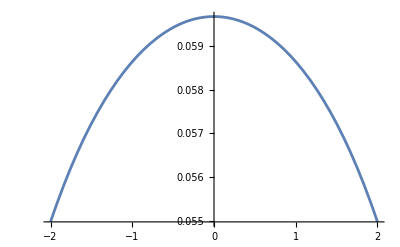

```mathematica
Plot[Gnxnxnynyny[1,0,Cos[t],Sin[t],0,1,-Sin[t],Cos[t],1,0,Cos[t],Sin[t]]+3/(4 Pi t^2),{t,-2,2}]
```

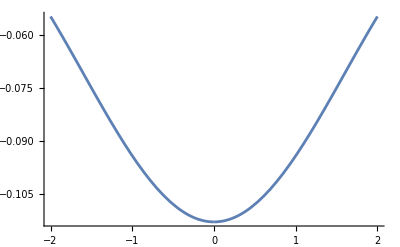

```mathematica
Plot[Gnxtxtxny[1,0,Cos[t],Sin[t],0,1,-Sin[t],Cos[t],1,0,Cos[t],Sin[t]]-1/(4 Pi t^2),{t,-2,2}]
```

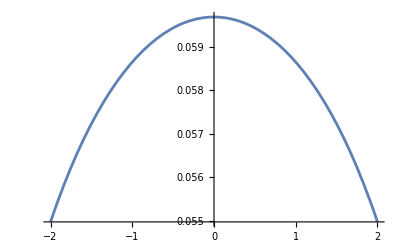

```mathematica
Plot[Gtxtxnynyny[1,0,Cos[t],Sin[t],0,1,-Sin[t],Cos[t],1,0,Cos[t],Sin[t]]+3/(4 Pi t^2),{t,-2,2}]
```

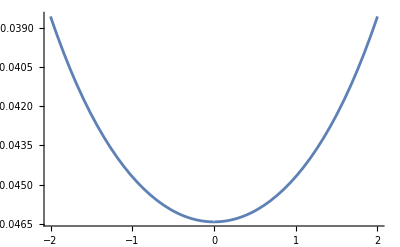

```mathematica
Plot[Gnxnxnytyty[1,0,Cos[t],Sin[t],0,1,-Sin[t],Cos[t],1,0,Cos[t],Sin[t]]-5/(4 Pi t^2),{t,-2,2}]
```

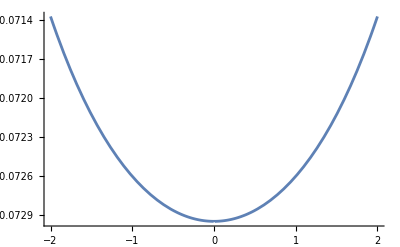

```mathematica
Plot[Gtxtxnytyty[1,0,Cos[t],Sin[t],0,1,-Sin[t],Cos[t],1,0,Cos[t],Sin[t]]-1/(4 Pi t^2),{t,-2,2}]
```

```mathematica
(3k^3-7*kpp)/16+(3k^3+kpp)*nu/16+(-7k^3+19*kpp)/48-nu*(11k^3+kpp)/48-(1-nu)/2*k^3/12 // Simplify
```

1/24 kpp (-1+nu)

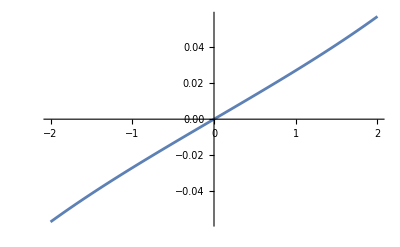

```mathematica
Plot[H[1,0,Cos[t],Sin[t],0,1,-Sin[t],Cos[t],1,0,Cos[t],Sin[t]]+1/(Pi*t),{t,-2,2}]
```

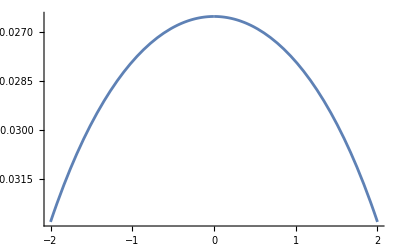

```mathematica
Plot[Hp[1,0,Cos[t],Sin[t],0,1,-Sin[t],Cos[t],1,0,Cos[t],Sin[t]]+1/(Pi*t^2),{t,-2,2}]
```

```mathematica
N4[t_, nu_]=Gnxnxnynyny[1,0,Cos[t],Sin[t],0,1,-Sin[t],Cos[t],1,0,Cos[t],Sin[t]]+nu*Gtxtxnynyny[1,0,Cos[t],Sin[t],0,1,-Sin[t],Cos[t],1,0,Cos[t],Sin[t]]+Gnxnxnytyty[1,0,Cos[t],Sin[t],0,1,-Sin[t],Cos[t],1,0,Cos[t],Sin[t]]+nu*Gtxtxnytyty[1,0,Cos[t],Sin[t],0,1,-Sin[t],Cos[t],1,0,Cos[t],Sin[t]]+(1-nu)/2*Hp[1,0,Cos[t],Sin[t],0,1,-Sin[t],Cos[t],1,0,Cos[t],Sin[t]];
```

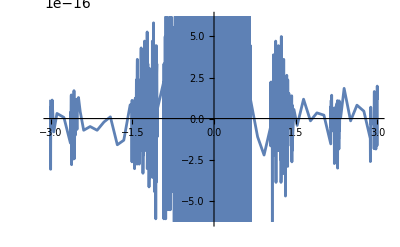

```mathematica
Plot[N4[t, 0.3],{t,-3,3}]
```

```mathematica
x1 = 2;
x2 = 0;
nx1 = 1;
nx2 = 0;
taux1 =0;
taux2 = 1;
y1[t_] = 2*Cos[t];
y2[t_] = Sin[t];
den[t_]=Sqrt[4*Sin[t]^2+Cos[t]^2];
tauy1[t_] = -2*Sin[t]/den[t];
tauy2[t_] = Cos[t]/den[t];
ny1[t_] = Cos[t]/den[t];
ny2[t_] = 2*Sin[t]/den[t];
kappa[t_]= 1/4(y1[t]^2/16+y2[t]^2)^(-3/2)
```

1/(4 (Cos[t]^2/4+Sin[t]^2)^(3/2))

```mathematica
N4[t_, nu_]=Gnxnxnynyny[nx1,nx2,ny1[t],ny2[t],taux1,taux2,tauy1[t],tauy2[t],x1,x2,y1[t],y2[t]] +nu*Gtxtxnynyny[nx1,nx2,ny1[t],ny2[t],taux1,taux2,tauy1[t],tauy2[t],x1,x2,y1[t],y2[t]]  +Gnxnxnytyty[nx1,nx2,ny1[t],ny2[t],taux1,taux2,tauy1[t],tauy2[t],x1,x2,y1[t],y2[t]]  +nu*Gtxtxnytyty[nx1,nx2,ny1[t],ny2[t],taux1,taux2,tauy1[t],tauy2[t],x1,x2,y1[t],y2[t]]  +kappa[t]*(1-nu)/2*Hp[nx1,nx2,ny1[t],ny2[t],taux1,taux2,tauy1[t],tauy2[t],x1,x2,y1[t],y2[t]] ;
```

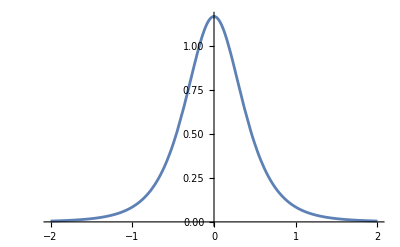

```mathematica
Plot[N4[t,0.3] ,{t,-2,2}]
```

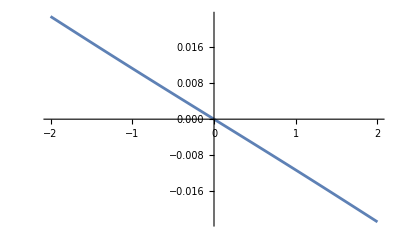

```mathematica
Plot[Gnxnxnynyty[1,0,Cos[t],Sin[t],0,1,-Sin[t],Cos[t],1,0,Cos[t],Sin[t]]+3/(2 Pi t^3)-1/(2 Pi t),{t,-2,2}]
```

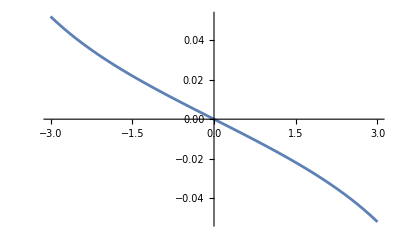

```mathematica
Plot[Gtxtxnynyty[1,0,Cos[t],Sin[t],0,1,-Sin[t],Cos[t],1,0,Cos[t],Sin[t]]-1/(2 Pi t^3)-1/(2 Pi t),{t,-3,3}]
```

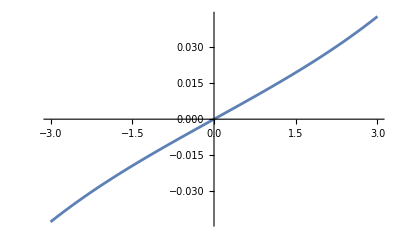

```mathematica
Plot[Gnxnxtytyty[1,0,Cos[t],Sin[t],0,1,-Sin[t],Cos[t],1,0,Cos[t],Sin[t]]-1/(2 Pi t^3)+1/(2 Pi t),{t,-3,3}]
```

```mathematica
Plot[Gtxtxtytyty[1,0,Cos[t],Sin[t],0,1,-Sin[t],Cos[t],1,0,Cos[t],Sin[t]]-1/(2 Pi t^3)+1/(2 Pi t),{t,-3,3}]
```

-Graphics-

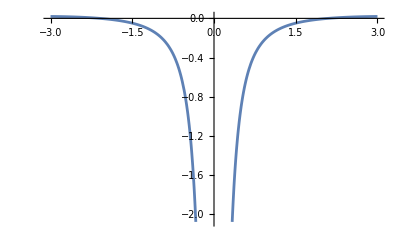

```mathematica
Plot[Gnxnxnynyny[1,0,Cos[t],Sin[t],0,1,-Sin[t],Cos[t],1,0,Cos[t],Sin[t]],{t,-3,3}]
```

```mathematica
Gnxnxnynyny[nx1,nx2,ny1[t],ny2[t],taux1,taux2,tauy1[t],tauy2[t],x1,x2,y1[t],y2[t]]
```

```mathematica
NIntegrate[Exp[-t^2]*Gnxnxnynyny[1,0,Cos[t],Sin[t],0,1,-Sin[t],Cos[t],1+10^-3,0,Cos[t],Sin[t]],{t,-3,3},MaxRecursion->50,WorkingPrecision->50]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

-1.5421600568705522401831745533429718099275214597706

```mathematica
NIntegrate[Exp[-10000*t^2]*Gnxnxny[1,0,Cos[t],Sin[t],0,1,-Sin[t],Cos[t],1.0000001,0,Cos[t],Sin[t]],{t,-3,3},MaxRecursion->100]
```

-0.500697

```mathematica
NIntegrate[Exp[-t^2]*(Gnxnxnynyny[1,0,Cos[t],Sin[t],0,1,-Sin[t],Cos[t],1+10^-2,0,Cos[t],Sin[t]]),{t,-1,1},MaxRecursion->100, WorkingPrecision->100]
```

-1.459331120218226948043864567769825274267924379903044824301768799845828058243287832551599911982672288

```mathematica
NIntegrate[Exp[-t^2]*(Gtxtxnynyny[1,0,Cos[t],Sin[t],0,1,-Sin[t],Cos[t],1+10^-4,0,Cos[t],Sin[t]]),{t,-1,1},MaxRecursion->100, WorkingPrecision->100]
```

1.47695398881174727533168982525061317233260129278360291206359918653636615500162410700745594773536486

```mathematica
NIntegrate[Exp[-t^2]*(Gnxnxnytyty[1,0,Cos[t],Sin[t],0,1,-Sin[t],Cos[t],1+10^-4,0,Cos[t],Sin[t]]),{t,-1,1},MaxRecursion->100, WorkingPrecision->100]
```

-0.05007106646727488884266727000802706675987390197857299546936790710638109860343947022585293284401894804

```mathematica
NIntegrate[Exp[-t^2]*(Gtxtxtytyty[1,0,Cos[t],Sin[t],0,1,-Sin[t],Cos[t],1+10^-2,0,Cos[t],Sin[t]]),{t,-1,1},MaxRecursion->100, WorkingPrecision->100]
```

```mathematica
NIntegrate[Exp[-t^2]*(Gnxnxnynyny[0,1,0,1,0,-1,0,-1,0,10^-4,t,0]),{t,-2,2},MaxRecursion->100, WorkingPrecision->100]
```

-1.99943598888886480993331055212581448412509947230526556600794188608763683389987877568564549978646364

```mathematica
NIntegrate[Exp[-t^2]*(Gnxnxny[0,1,0,1,0,-1,0,-1,0,10^-4,t,0]),{t,-2,2},MaxRecursion->100, WorkingPrecision->100]
```

-0.4999153401772606243959309445640376082486834869311578719597683560469716377900629009925939287672469364

```mathematica
R=5;
R*NIntegrate[Exp[-10*t^2]*(Gnxnxny[0,1,Sin[t],Cos[t],0,-1,-Cos[t],Sin[t],0,R+10^-8,R*Sin[t],R*Cos[t]]),{t,-4,4},MaxRecursion->100, WorkingPrecision->100]
```

-0.5217509177219346214911961377491111251462143396272819004686596549220257272702144262962322009599059763

```mathematica
R=4;
R*NIntegrate[t^2*Exp[-1000*t^2]*(Gnxnxnynyny[0,1,Sin[t],Cos[t],0,-1,-Cos[t],Sin[t],0,R+10^-10,R*Sin[t],R*Cos[t]]),{t,-1,1},MaxRecursion->100, WorkingPrecision->100]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

0.1241637959382801300365212841978283380604224071718246761451347462410465509719521883141299192605904133

```mathematica
R=1;
R*NIntegrate[Exp[-1*t^2]*(Gtxtxtytyty[0,1,Sin[t],Cos[t],0,-1,-Cos[t],Sin[t],0,R+10^-10,R*Sin[t],R*Cos[t]]),{t,-5,5},MaxRecursion->100, WorkingPrecision->100]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::errprec: Catastrophic loss of precision in the global error estimate due to insufficient WorkingPrecision or divergent integral.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::errprec: Catastrophic loss of precision in the global error estimate due to insufficient WorkingPrecision or divergent integral.

NIntegrate[t^2 Exp[-t^2] Gtxtxtytyty[0,1,Sin[t],Cos[t],0,-1,-Cos[t],Sin[t],0,R+1/10^10,R Sin[t],R Cos[t]],{t,-5,5},MaxRecursion→100,WorkingPrecision→100]

```mathematica
nu =3/10;
R=1; 
R^3*NIntegrate[Exp[-t^2]*(Gnxnxnynyny[1,0,Cos[t],Sin[t],0,1,-Sin[t],Cos[t],R+10^-4,0,R*Cos[t],R*Sin[t]]+nu*Gtxtxnynyny[1,0,Cos[t],Sin[t],0,1,-Sin[t],Cos[t],R+10^-4,0,R*Cos[t],R*Sin[t]]  +Gnxnxnytyty[1,0,Cos[t],Sin[t],0,1,-Sin[t],Cos[t],R+10^-4,0,R*Cos[t],R*Sin[t]]+nu*Gtxtxnytyty[1,0,Cos[t],Sin[t],0,1,-Sin[t],Cos[t],R+10^-4,0,R*Cos[t],R*Sin[t]]  +(1-nu)/(2R)*Hp[1,0,Cos[t],Sin[t],0,1,-Sin[t],Cos[t],R+10^-4,0,R*Cos[t],R*Sin[t]] ),{t, -4, 4},WorkingPrecision->100,MaxRecursion->20]
```

-0.6996641319169544828224703806325756518527598260802995280434541540450507201328360140171555481148300769

```mathematica
nu =3/10;
R=1; 
R^3*NIntegrate[t^2*Exp[-1000*t^2]*(Gtxtxnynyny[1,0,Cos[t],Sin[t],0,1,-Sin[t],Cos[t],R+10^-4,0,R*Cos[t],R*Sin[t]] ),{t, -4, 4},WorkingPrecision->100,MaxRecursion->100]
```

-0.9971453001308525099543521796764876508223185216704881417362322368181489653409117005992034404927493677

```mathematica
R^3*NIntegrate[t^2*Exp[-1000*t^2]*(Gnxnxnytyty[1,0,Cos[t],Sin[t],0,1,-Sin[t],Cos[t],R+10^-4,0,R*Cos[t],R*Sin[t]]),{t, -4, 4},WorkingPrecision->100,MaxRecursion->100]
```

-0.9620614698064444663081714300639412975886227067492355870215322774791537042996830055004837396950269496

```mathematica
NIntegrate[t^2*Exp[-t^2]/2*(Gnxnxnynyny[0,1,0,1,0,-1,0,-1,0,10^-4,t,0]),{t,-2,2},MaxRecursion->100, WorkingPrecision->100]
```

0.9995767408778427303547516237147344085430920215849248475325168931900508766336441205026458372843117948

```mathematica
NIntegrate[t^2*Exp[-t^2]/2*(Gtxtxnynyny[0,1,0,1,0,-1,0,-1,0,10^-4,t,0]),{t,-2,2},MaxRecursion->100, WorkingPrecision->100]
```

0.9995767408778427303547516237147344085430920215849248475325168931900508766336441205026458372843117948

```mathematica
NIntegrate[t^2*Exp[-t^2]/2*(Gnxnxnytyty[0,1,0,1,0,-1,0,-1,0,10^-4,t,0]),{t,-2,2},MaxRecursion->100, WorkingPrecision->100]
```

0.9995767408778427303547516237147344085430920215849248475325168931900508766336441205026458372843117948

```mathematica
NIntegrate[Exp[-t^2]/2*(Gtxtxnytyty[0,1,0,1,0,-1,0,-1,0,10^-4,t,0]),{t,-2,2},MaxRecursion->100, WorkingPrecision->100]
```

-0.9997179944444324049666552760629072420625497361526327830039709430438184169499393878428227498932318201

```mathematica
Gnxnxny
```

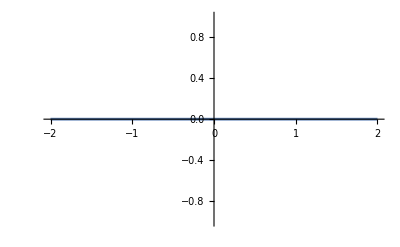

```mathematica
Plot[Gtxtxnytyty[0,1,0,1,0,-1,0,-1,0,0,t,0],{t, -2, 2}]
```

### REAL LINE DEFINITIONS

```mathematica
r[t_] = {-t,10^-4};
r2[t_]=r[t].r[t];
nx[t_]={0,1};
ny[t_]= {0,1};
tx[t_] = {-1,0};
ty[t_] = {-1,0};
```

```mathematica
Gnxnxnynyny[t_]= 3/(2*Pi)(r[t].ny[t])/r2[t]^2 - 6/Pi(r[t].ny[t])(r[t].nx[t])^2/r2[t]^3+3/Pi(r[t].ny[t])(nx[t].ny[t])^2/r2[t]^2-12/Pi(r[t].ny[t])^2(r[t].nx[t])(nx[t].ny[t])/r2[t]^3-2/Pi(r[t].ny[t])^3/r2[t]^3+12/Pi(r[t].ny[t])^3(r[t].nx[t])^2/r2[t]^4+3/Pi*(r[t].nx[t])(nx[t].ny[t])/r2[t]^2;
Gtxtxnynyny[t_]= 3/(2*Pi)(r[t].ny[t])/r2[t]^2 - 6/Pi(r[t].ny[t])(r[t].tx[t])^2/r2[t]^3+3/Pi(r[t].ny[t])(tx[t].ny[t])^2/r2[t]^2-12/Pi(r[t].ny[t])^2(r[t].tx[t])(tx[t].ny[t])/r2[t]^3-2/Pi(r[t].ny[t])^3/r2[t]^3+12/Pi(r[t].ny[t])^3(r[t].tx[t])^2/r2[t]^4+3/Pi*(r[t].tx[t])(tx[t].ny[t])/r2[t]^2;
Gnxnxtytyty[t_]= 3/(2*Pi)(r[t].ty[t])/r2[t]^2 - 6/Pi(r[t].ty[t])(r[t].nx[t])^2/r2[t]^3+3/Pi(r[t].ty[t])(nx[t].ty[t])^2/r2[t]^2-12/Pi(r[t].ty[t])^2(r[t].nx[t])(nx[t].ty[t])/r2[t]^3-2/Pi(r[t].ty[t])^3/r2[t]^3+12/Pi(r[t].ty[t])^3(r[t].nx[t])^2/r2[t]^4+3/Pi*(r[t].nx[t])(nx[t].ty[t])/r2[t]^2;
Gtxtxtytyty[t_]= 3/(2*Pi)(r[t].ty[t])/r2[t]^2 - 6/Pi(r[t].ty[t])(r[t].tx[t])^2/r2[t]^3+3/Pi(r[t].ty[t])(tx[t].ty[t])^2/r2[t]^2-12/Pi(r[t].ty[t])^2(r[t].tx[t])(tx[t].ty[t])/r2[t]^3-2/Pi(r[t].ty[t])^3/r2[t]^3+12/Pi(r[t].ty[t])^3(r[t].tx[t])^2/r2[t]^4+3/Pi*(r[t].tx[t])(tx[t].ty[t])/r2[t]^2;
Gnxnxnytyty[t_]=2/Pi*(nx[t].ny[t])(nx[t].tauy[t])(r[t].tauy[t])/r2[t]^2-4/Pi(nx[t].ny[t])(r[t].tauy[t])^2(r[t].nx[t])/r2[t]^3+1/Pi(r[t].ny[t])(nx[t].tauy[t])^2/r2[t]^2-8/Pi(r[t].ny[t])(r[t].tauy[t])(r[t].nx[t])(nx[t].tauy[t])/r2[t]^3-2/Pi(r[t].ny[t])(r[t].tauy[t])^2/r2[t]^3+12/Pi(r[t].ny[t])(r[t].tauy[t])^2(r[t].nx[t])^2/r2[t]^4+1/Pi(nx[t].ny[t])(r[t].nx[t])/r2[t]^2+1/(2Pi)(r[t].ny[t])/r2[t]^2-2/Pi(r[t].ny[t])(r[t].nx[t])^2/r2[t]^3;
Gtxtxnytyty[t_]=2/Pi*(tx[t].ny[t])(tx[t].tauy[t])(r[t].tauy[t])/r2[t]^2-4/Pi(tx[t].ny[t])(r[t].tauy[t])^2(r[t].tx[t])/r2[t]^3+1/Pi(r[t].ny[t])(tx[t].tauy[t])^2/r2[t]^2-8/Pi(r[t].ny[t])(r[t].tauy[t])(r[t].tx[t])(tx[t].tauy[t])/r2[t]^3-2/Pi(r[t].ny[t])(r[t].tauy[t])^2/r2[t]^3+12/Pi(r[t].ny[t])(r[t].tauy[t])^2(r[t].tx[t])^2/r2[t]^4+1/Pi(tx[t].ny[t])(r[t].tx[t])/r2[t]^2+1/(2Pi)(r[t].ny[t])/r2[t]^2-2/Pi(r[t].ny[t])(r[t].tx[t])^2/r2[t]^3;
Gnxnxnynyty[t_] = 2/Pi(nx[t].tauy[t])(nx[t].ny[t])(r[t].ny[t])/r2[t]^2-4/Pi(nx[t].tauy[t])(r[t].ny[t])^2(r[t].nx[t])/r2[t]^3+1/Pi(r[t].tauy[t])(nx[t].ny[t])^2/r2[t]^2-8/Pi(r[t].tauy[t])(r[t].ny[t])(r[t].nx[t])(nx[t].ny[t])/r2[t]^3-2/Pi(r[t].tauy[t])(r[t].ny[t])^2/r2[t]^3+12/Pi(r[t].tauy[t])(r[t].ny[t])^2(r[t].nx[t])^2/r2[t]^4+1/Pi(nx[t].tauy[t])(r[t].nx[t])/r2[t]^2+1/(2Pi)(r[t].tauy[t])/r2[t]^2-2/Pi(r[t].tauy[t])(r[t].nx[t])^2/r2[t]^3;
Gtxtxnynyty[t_] = 2/Pi(taux[t].tauy[t])(taux[t].ny[t])(r[t].ny[t])/r2[t]^2-4/Pi(taux[t].tauy[t])(r[t].ny[t])^2(r[t].taux[t])/r2[t]^3+1/Pi(r[t].tauy[t])(taux[t].ny[t])^2/r2[t]^2-8/Pi(r[t].tauy[t])(r[t].ny[t])(r[t].taux[t])(taux[t].ny[t])/r2[t]^3-2/Pi(r[t].tauy[t])(r[t].ny[t])^2/r2[t]^3+12/Pi(r[t].tauy[t])(r[t].ny[t])^2(r[t].taux[t])^2/r2[t]^4+1/Pi(taux[t].tauy[t])(r[t].taux[t])/r2[t]^2+1/(2Pi)(r[t].tauy[t])/r2[t]^2-2/Pi(r[t].tauy[t])(r[t].taux[t])^2/r2[t]^3;
```

Set::write: Tag SeriesData in … is Protected.

```mathematica
NIntegrate[t^2/2*Exp[-t^2]*Gnxnxnynyny[t],{t,-2,2},WorkingPrecision->100,MaxRecursion->50]
```

0.9957754957626626738896583214010162314394928142266019145261018517939392842819327184885368964221913428

```mathematica
NIntegrate[t^2/2*Exp[-t^2]*Gtxtxnynyny[t],{t,-2,2},WorkingPrecision->100,MaxRecursion->50]
```

-0.4974658959555754772701812541525496862369200430461360940155459470351233451530021068373610343992966079

```mathematica
NIntegrate[t^2/2*Exp[-t^2]*Gnxnxnytyty[t],{t,-2,2},WorkingPrecision->100,MaxRecursion->50]
```

-0.4974658959555754772701812541525496862369200430461360940155459470351233451530021068373610343992966079

```mathematica
NIntegrate[t^2/2*Exp[-t^2]*Gtxtxnytyty[t],{t,-2,2},WorkingPrecision->100,MaxRecursion->50]
```

-0.0008437038515117193492958130959168589656527281343297264950099577236925939759285048138148276235981271165

```mathematica
NIntegrate[Exp[-10*t^2]*(Gtxtxtytyty[t]),{t,-6,6},WorkingPrecision->100,MaxRecursion->100]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -2.603556337174201462251539464211172407191994519201990182357654982206176797067177937108246117501672771×10^-106 and 9.425759328789021241176918074860248075608228940775159034101977898649670747805228818127955033064205416×10^-105 for the integral and error estimates.

-2.603556337174201462251539464211172407191994519201990182357654982206176797067177937108246117501672771×10^-106

### CIRCLE DEFINITIONS

```mathematica
R = 1;
r[t_] = {R+10^-10,0}-{R*Cos[t],R*Sin[t]};
r2[t_]=r[t].r[t];
nx[t_]={1,0};
ny[t_]= {Cos[t],Sin[t]};
tx[t_] = {0,1};
ty[t_] = {-Sin[t],Cos[t]};
```

```mathematica
Gnxnxnynyny[t_]= 3/(2*Pi)(r[t].ny[t])/r2[t]^2 - 6/Pi(r[t].ny[t])(r[t].nx[t])^2/r2[t]^3+3/Pi(r[t].ny[t])(nx[t].ny[t])^2/r2[t]^2-12/Pi(r[t].ny[t])^2(r[t].nx[t])(nx[t].ny[t])/r2[t]^3-2/Pi(r[t].ny[t])^3/r2[t]^3+12/Pi(r[t].ny[t])^3(r[t].nx[t])^2/r2[t]^4+3/Pi*(r[t].nx[t])(nx[t].ny[t])/r2[t]^2;
Gtxtxnynyny[t_]= 3/(2*Pi)(r[t].ny[t])/r2[t]^2 - 6/Pi(r[t].ny[t])(r[t].tx[t])^2/r2[t]^3+3/Pi(r[t].ny[t])(tx[t].ny[t])^2/r2[t]^2-12/Pi(r[t].ny[t])^2(r[t].tx[t])(tx[t].ny[t])/r2[t]^3-2/Pi(r[t].ny[t])^3/r2[t]^3+12/Pi(r[t].ny[t])^3(r[t].tx[t])^2/r2[t]^4+3/Pi*(r[t].tx[t])(tx[t].ny[t])/r2[t]^2;
Gnxnxtytyty[t_]= 3/(2*Pi)(r[t].ty[t])/r2[t]^2 - 6/Pi(r[t].ty[t])(r[t].nx[t])^2/r2[t]^3+3/Pi(r[t].ty[t])(nx[t].ty[t])^2/r2[t]^2-12/Pi(r[t].ty[t])^2(r[t].nx[t])(nx[t].ty[t])/r2[t]^3-2/Pi(r[t].ty[t])^3/r2[t]^3+12/Pi(r[t].ty[t])^3(r[t].nx[t])^2/r2[t]^4+3/Pi*(r[t].nx[t])(nx[t].ty[t])/r2[t]^2;
Gtxtxtytyty[t_]= 3/(2*Pi)(r[t].ty[t])/r2[t]^2 - 6/Pi(r[t].ty[t])(r[t].tx[t])^2/r2[t]^3+3/Pi(r[t].ty[t])(tx[t].ty[t])^2/r2[t]^2-12/Pi(r[t].ty[t])^2(r[t].tx[t])(tx[t].ty[t])/r2[t]^3-2/Pi(r[t].ty[t])^3/r2[t]^3+12/Pi(r[t].ty[t])^3(r[t].tx[t])^2/r2[t]^4+3/Pi*(r[t].tx[t])(tx[t].ty[t])/r2[t]^2;
Gnxnxnytyty[t_]=2/Pi*(nx[t].ny[t])(nx[t].tauy[t])(r[t].tauy[t])/r2[t]^2-4/Pi(nx[t].ny[t])(r[t].tauy[t])^2(r[t].nx[t])/r2[t]^3+1/Pi(r[t].ny[t])(nx[t].tauy[t])^2/r2[t]^2-8/Pi(r[t].ny[t])(r[t].tauy[t])(r[t].nx[t])(nx[t].tauy[t])/r2[t]^3-2/Pi(r[t].ny[t])(r[t].tauy[t])^2/r2[t]^3+12/Pi(r[t].ny[t])(r[t].tauy[t])^2(r[t].nx[t])^2/r2[t]^4+1/Pi(nx[t].ny[t])(r[t].nx[t])/r2[t]^2+1/(2Pi)(r[t].ny[t])/r2[t]^2-2/Pi(r[t].ny[t])(r[t].nx[t])^2/r2[t]^3;
Gtxtxnytyty[t_]=2/Pi*(tx[t].ny[t])(tx[t].tauy[t])(r[t].tauy[t])/r2[t]^2-4/Pi(tx[t].ny[t])(r[t].tauy[t])^2(r[t].tx[t])/r2[t]^3+1/Pi(r[t].ny[t])(tx[t].tauy[t])^2/r2[t]^2-8/Pi(r[t].ny[t])(r[t].tauy[t])(r[t].tx[t])(tx[t].tauy[t])/r2[t]^3-2/Pi(r[t].ny[t])(r[t].tauy[t])^2/r2[t]^3+12/Pi(r[t].ny[t])(r[t].tauy[t])^2(r[t].tx[t])^2/r2[t]^4+1/Pi(tx[t].ny[t])(r[t].tx[t])/r2[t]^2+1/(2Pi)(r[t].ny[t])/r2[t]^2-2/Pi(r[t].ny[t])(r[t].tx[t])^2/r2[t]^3;
Gnxnxnynyty[t_] = 2/Pi(nx[t].tauy[t])(nx[t].ny[t])(r[t].ny[t])/r2[t]^2-4/Pi(nx[t].tauy[t])(r[t].ny[t])^2(r[t].nx[t])/r2[t]^3+1/Pi(r[t].tauy[t])(nx[t].ny[t])^2/r2[t]^2-8/Pi(r[t].tauy[t])(r[t].ny[t])(r[t].nx[t])(nx[t].ny[t])/r2[t]^3-2/Pi(r[t].tauy[t])(r[t].ny[t])^2/r2[t]^3+12/Pi(r[t].tauy[t])(r[t].ny[t])^2(r[t].nx[t])^2/r2[t]^4+1/Pi(nx[t].tauy[t])(r[t].nx[t])/r2[t]^2+1/(2Pi)(r[t].tauy[t])/r2[t]^2-2/Pi(r[t].tauy[t])(r[t].nx[t])^2/r2[t]^3;
Gtxtxnynyty[t_] = 2/Pi(taux[t].tauy[t])(taux[t].ny[t])(r[t].ny[t])/r2[t]^2-4/Pi(taux[t].tauy[t])(r[t].ny[t])^2(r[t].taux[t])/r2[t]^3+1/Pi(r[t].tauy[t])(taux[t].ny[t])^2/r2[t]^2-8/Pi(r[t].tauy[t])(r[t].ny[t])(r[t].taux[t])(taux[t].ny[t])/r2[t]^3-2/Pi(r[t].tauy[t])(r[t].ny[t])^2/r2[t]^3+12/Pi(r[t].tauy[t])(r[t].ny[t])^2(r[t].taux[t])^2/r2[t]^4+1/Pi(taux[t].tauy[t])(r[t].taux[t])/r2[t]^2+1/(2Pi)(r[t].tauy[t])/r2[t]^2-2/Pi(r[t].tauy[t])(r[t].taux[t])^2/r2[t]^3;
```

```mathematica
NIntegrate[t^2/2*Exp[-t^2]*Gnxnxnynyny[t],{t,-4,4},WorkingPrecision->100,MaxRecursion->100]
```

0.814139082174364143316177154655248039595804329302030106513819503811702136449887014485959176610700172

```mathematica
NIntegrate[t^2/2*Exp[-t^2]*Gtxtxnynyny[t],{t,-4,4},WorkingPrecision->100,MaxRecursion->100]
```

-0.6858609169694677762441318922520707107660124145912922207599963637161168453215864248856388596173240478

```mathematica
NIntegrate[t^2/2*Exp[-t^2]*Gnxnxnytyty[t],{t,-2,2},WorkingPrecision->100,MaxRecursion->50]
```

0.7343139547673475086549412762848953629964798718893852915234576032883526409437594423702904163178920917

```mathematica
NIntegrate[t^2/2*Exp[-t^2]*Gtxtxnytyty[t],{t,-2,2},WorkingPrecision->100,MaxRecursion->50]
```

-0.0008437038515117193492958130959168589656527281343297264950099577236925939759285048138148276235981271165

```mathematica
NIntegrate[Exp[-10*t^2]*(Gtxtxtytyty[t]),{t,-6,6},WorkingPrecision->100,MaxRecursion->100]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -2.603556337174201462251539464211172407191994519201990182357654982206176797067177937108246117501672771×10^-106 and 9.425759328789021241176918074860248075608228940775159034101977898649670747805228818127955033064205416×10^-105 for the integral and error estimates.

-2.603556337174201462251539464211172407191994519201990182357654982206176797067177937108246117501672771×10^-106

```mathematica
D[h/(s^2+h^2),s]
```

-(2 h s)/((h^2+s^2)^2)

```mathematica
D[h/(s^2+h^2),{s,2}]
```

h ((8 s^2)/((h^2+s^2)^3)-2/((h^2+s^2)^2))

```mathematica
D[h^3/(s^2+h^2)^2,{s,2}]
```

h^3 ((24 s^2)/((h^2+s^2)^4)-4/((h^2+s^2)^3))

```mathematica
Integrate[1/(s^2+h^2),s]
```

ArcTan[s/h]/h

```mathematica
Integrate[h^3/(s^2+h^2)^2,s]
```

1/2 ((h s)/(h^2+s^2)+ArcTan[s/h])

```mathematica
(3/(4Pi))Integrate[h/(s^2+h^2)^2,{s,-d,d}]-(1/(2Pi))Integrate[h^3/(s^2+h^2)^2,{s,-d,d}] // Simplify
```

ConditionalExpression[-((-3+2 h^2) (d h+(d^2+h^2) ArcTan[d/h]))/(4 h^2 (d^2+h^2) π), Im[h/d]>1||Im[h/d]<-1||Re[h/d]≠0]

```mathematica
Integrate[h^3/(s^2+h^2)^2,s]
```

1/2 ((h s)/(h^2+s^2)+ArcTan[s/h])

```mathematica
D[ArcTan[s/h],s]
```

1/(h (1+s^2/h^2))

```mathematica
D[h s/(h^2+s^2),s]
```

-(2 h s^2)/((h^2+s^2)^2)+h/(h^2+s^2)

ConditionalExpression[(d h)/(d^2+h^2)+ArcTan[d/h], Im[h/d]>1||Im[h/d]<-1||Re[h/d]≠0]

```mathematica
Integrate[s^3/(s^2+h^2)^2,{s,-d,d}]
```

0

```mathematica
taux = {1, 0};
nx = {0, 1};
x={0,h};
y = s*taux ;
r = x-y;
r2 =s^2+h^2;
tauy = taux ;
ny = n ;
Gnxnxnxnyny = 3/(2*Pi)(r.ny)/r2^2 - 6/Pi(r.ny)(r.nx)^2/r2^3+3/Pi(r.ny)(nx.ny)^2/r2^2-12/Pi(r.ny)^2(r.nx)(nx.ny)/r2^3-2/Pi(r.ny)^3/r2^3+12/Pi(r.ny)^3(r.nx)^2/r2^4+3/Pi*(r.nx)(nx.ny)/r2^2 ;
Integrate[Integrate[Integrate[Gnxnxnxnyny,s],s],s]
```

(h (-s/(h^2+s^2)+(4 ArcTan[s/h])/h))/(4 π)

```mathematica
taux = {1, 0};
nx = {0, 1};
x={0,h};
y = s*taux - s^2/2*k*nx;
r = x-y;
r2 =s^2+h^2;
tauy = taux - s*k*nx;
ny = n +s*k*taux;
Gnxnxnxnyny = 3/(2*Pi)(r.ny)/r2^2 - 6/Pi(r.ny)(r.nx)^2/r2^3+3/Pi(r.ny)(nx.ny)^2/r2^2-12/Pi(r.ny)^2(r.nx)(nx.ny)/r2^3-2/Pi(r.ny)^3/r2^3+12/Pi(r.ny)^3(r.nx)^2/r2^4+3/Pi*(r.nx)(nx.ny)/r2^2 ;Integrate[Integrate[Integrate[Gnxnxnxnyny,s],s],s]
```

-1/(128 π)(-3/2 k^2 (-32-80 h k+70 h^2 k^2+105 h^3 k^3) (h^2+s^2) ArcTan[h/s]-4 (32+48 h k-132 h^2 k^2-170 h^3 k^3+105 h^4 k^4+126 h^5 k^5) ArcTan[s/h]+1/(30 (h^2+s^2))s (8430 h^5 k^4+9705 h^6 k^5+30 h^3 k^2 (-352+263 k^2 s^2)+15 h^4 k^3 (-928+581 k^2 s^2)-480 h (-2+21 k^2 s^2+k^4 s^4)+8 k s^2 (360+40 k^2 s^2+3 k^4 s^4)-8 h^2 k (-420+1670 k^2 s^2+117 k^4 s^4)-1440 k (1+h k)^2 (1-6 h k+5 h^2 k^2) (h^2+s^2) Log[h^2+s^2]))

```mathematica
Simplify[%349]
```

```mathematica
1/(1152 h^2 π)(-108 h^3 (-8-12 h k+5 h^2 k^2) kp ArcTan[h/s]-6 (-144+72 h k+72 h^2 k^2+18 h^3 (k^3-3 kpp)+5 h^5 k (k^4+3 kp^2-k kpp)) s ArcTan[s/h]+h^2 (s (-36 kp (-16-24 h k+12 h^2 k^2+k^2 s^2)+kp^2 (36 h^2 k s-3 k s^3)+s (36 k^3-108 kpp+k^5 (12 h^2-s^2)+k^2 kpp (-12 h^2+s^2)))+18 (4 h^2 k^3+h^4 k^5-4 (3 h^2 kpp+4 kp s)+3 k (8+h^4 kp^2-8 h kp s)+h k^2 (24-h^3 kpp+12 h kp s)) Log[h^2+s^2])
```

```mathematica
Gnxnxnxnyny = 3/(2*Pi)(r.ny)/r2^2 - 6/Pi(r.ny)(r.nx)^2/r2^3+3/Pi(r.ny)(nx.ny)^2/r2^2-12/Pi(r.ny)^2(r.nx)(nx.ny)/r2^3-2/Pi(r.ny)^3/r2^3+12/Pi(r.ny)^3(r.nx)^2/r2^4+3/Pi*(r.nx)(nx.ny)/r2^2 ;
```

```mathematica
Integrate[1/(1152 h^2 π)(-108 h^3 (-8-12 h k+5 h^2 k^2) kp ArcTan[h/s]-6 (-144+72 h k+72 h^2 k^2+18 h^3 (k^3-3 kpp)+5 h^5 k (k^4+3 kp^2-k kpp)) s ArcTan[s/h]+h^2 (s (-36 kp (-16-24 h k+12 h^2 k^2+k^2 s^2)+kp^2 (36 h^2 k s-3 k s^3)+s (36 k^3-108 kpp+k^5 (12 h^2-s^2)+k^2 kpp (-12 h^2+s^2)))+18 (4 h^2 k^3+h^4 k^5-4 (3 h^2 kpp+4 kp s)+3 k (8+h^4 kp^2-8 h kp s)+h k^2 (24-h^3 kpp+12 h kp s)) Log[h^2+s^2])),{s,-d,d}]
```

$Aborted

1/(72 π)h (3 (18 k^4-54 h k^5+5 h^2 k^6-24 h k kp^2+18 h k^2 (4 h kp^2-kpp)+14 h^2 k^3 kpp+5 h^2 kpp^2) s+kp (36 k^3-63 h k^4+27 h^2 k^5+20 h kp^2) s^2+1/(6 (h^2+s^2)^3)h^2 (-54 h^8 k^5 kp+2 h^7 (63 k^4 kp-20 kp^3)+864 s+432 h k s-432 h^2 k^2 s-18 h^5 k (30 k kp+9 k^4 s+4 kp^2 s+3 k kpp s)+36 h^3 (20 kp+(k^3+5 kpp) s)-6 h^4 (3 k^4 s+40 kp^2 s-12 k (4 kp+kpp s))+3 h^6 (5 k^6 s+72 k^2 kp^2 s+5 kpp (8 kp+kpp s)+2 k^3 (16 kp+7 kpp s)))-1/(16 h^2 (h^2+s^2))3 (864 h^8 k^5 kp-32 h^7 (63 k^4 kp-20 kp^3)-1440 s+144 h k s+144 h^2 k^2 s+12 h^3 (59 k^3-5 kpp) s+6 h^5 k (432 k kp+261 k^4 s+116 kp^2 s+87 k kpp s)-2 h^4 (384 k kp+129 k^4 s-440 kp^2 s+132 k kpp s)-h^6 (145 k^6 s+2088 k^2 kp^2 s+5 kpp (192 kp+29 kpp s)+2 k^3 (96 kp+203 kpp s)))-1/(8 (h^2+s^2)^2)(-432 h^8 k^5 kp+16 h^7 (63 k^4 kp-20 kp^3)-1440 s+144 h k s-1008 h^2 k^2 s+12 h^3 (120 kp-29 k^3 s+35 kpp s)-6 h^5 k (432 k kp+171 k^4 s+76 kp^2 s+57 k kpp s)+2 h^4 (576 k kp+15 k^4 s-520 kp^2 s+156 k kpp s)+h^6 (95 k^6 s+1368 k^2 kp^2 s+5 kpp (144 kp+19 kpp s)+k^3 (432 kp+266 kpp s)))-1/(16 h^3)3 (-1440+144 h k+144 h^2 k^2-12 h^3 (37 k^3+5 kpp)-210 h^5 k (9 k^4+4 kp^2+3 k kpp)+10 h^4 (51 k^4-40 kp^2+12 k kpp)+35 h^6 (5 k^6+72 k^2 kp^2+14 k^3 kpp+5 kpp^2)) ArcTan[s/h]-4 h kp (27 k^2+15 h k^3-63 h^2 k^4+27 h^3 k^5+5 h (4 h kp^2-3 kpp)) Log[h^2+s^2])

```mathematica
r.r // Expand
```

h^2+s^2+h k s^2+1/3 h kp s^3-(k^2 s^4)/12-1/12 h k^3 s^4+1/12 h kpp s^4-1/12 k kp s^5-(k^4 s^6)/72+(kp^2 s^6)/36+1/24 k kpp s^6+1/36 k^3 kp s^7+1/72 kp kpp s^7+(k^6 s^8)/576+1/64 k^2 kp^2 s^8-1/288 k^3 kpp s^8+(kpp^2 s^8)/576

```mathematica
y={s,0};
r =x-y;
r2 =r.r;
tauy = {1,0};
ny = {0,1};
```

```mathematica
Gnxnxnxnyny = 3/(2*Pi)(r.ny)/r2^2 - 6/Pi(r.ny)(r.nx)^2/r2^3+3/Pi(r.ny)(nx.ny)^2/r2^2-12/Pi(r.ny)^2(r.nx)(nx.ny)/r2^3-2/Pi(r.ny)^3/r2^3+12/Pi(r.ny)^3(r.nx)^2/r2^4+3/Pi*(r.nx)(nx.ny)/r2^2
```

(12 h^5)/(π (h^2+s^2)^4)-(20 h^3)/(π (h^2+s^2)^3)+(15 h)/(2 π (h^2+s^2)^2)

```mathematica
Integrate[Integrate[Integrate[Gnxnxnxnyny, s],s],{s,-d,d}]
```

ConditionalExpression[(-(d h)/(d^2+h^2)+4 ArcTan[d/h])/(2 π), Im[h/d]>1||Im[h/d]<-1||Re[h/d]≠0]

```mathematica
Integrate[Integrate[Gnxnxnxnyny, s],{s,-d,d}]
```

0

```mathematica
Integrate[(12 h^5)/(π (h^2+s^2)^4)-(20 h^3)/(π (h^2+s^2)^3)+(15 h)/(2 π (h^2+s^2)^2), s]
```

-(h s (h^2+5 s^2))/(2 π (h^2+s^2)^3)

```mathematica
Integrate[-(h s (h^2+5 s^2))/(2 π (h^2+s^2)^3),s]
```

(h (3 h^2+5 s^2))/(4 π (h^2+s^2)^2)

```mathematica
Integrate[(h (3 h^2+5 s^2))/(4 π (h^2+s^2)^2),{s,-d,d}]
```

ConditionalExpression[(-(d h)/(d^2+h^2)+4 ArcTan[d/h])/(2 π), Im[h/d]>1||Im[h/d]<-1||Re[h/d]≠0]

```mathematica
Integrate[h*s^2/(h^2+s^2)^2,{s,-d,d}]
```

ConditionalExpression[-(d h)/(d^2+h^2)+ArcTan[d/h], Im[h/d]>1||Im[h/d]<-1||Re[h/d]≠0]

```mathematica
r
```

{-s,h}

```mathematica
taux = {-1, 0};
nx = {0, 1};
r={-s,h};
r2 = (s^2+h^2);
tauy = tau ;
ny = {0,1} ;
Gnxnxnxnyny = 3/(2*Pi)(r.ny)/r2^2 - 6/Pi(r.ny)(r.nx)^2/r2^3+3/Pi(r.ny)(nx.ny)^2/r2^2-12/Pi(r.ny)^2(r.nx)(nx.ny)/r2^3-2/Pi(r.ny)^3/r2^3+12/Pi(r.ny)^3(r.nx)^2/r2^4+3/Pi*(r.nx)(nx.ny)/r2^2
```

(12 h^5)/(π (h^2+s^2)^4)-(20 h^3)/(π (h^2+s^2)^3)+(15 h)/(2 π (h^2+s^2)^2)

```mathematica
Integrate[h/((h^2+s^2)^1),s]
```

ArcTan[s/h]

```mathematica
Gnxnxnynyny = 3/(2*Pi)(r.ny)/r2^2 - 6/Pi(r.ny)(r.nx)^2/r2^3+3/Pi(r.ny)(nx.ny)^2/r2^2-12/Pi(r.ny)^2(r.nx)(nx.ny)/r2^3-2/Pi(r.ny)^3/r2^3+12/Pi(r.ny)^3(r.nx)^2/r2^4+3/Pi*(r.nx)(nx.ny)/r2^2
```

(3 nx.ny r.nx)/(π r2^2)+(3 r.ny)/(2 π r2^2)+(3 (nx.ny)^2 r.ny)/(π r2^2)-(6 (r.nx)^2 r.ny)/(π r2^3)-(12 nx.ny r.nx (r.ny)^2)/(π r2^3)-(2 (r.ny)^3)/(π r2^3)+(12 (r.nx)^2 (r.ny)^3)/(π r2^4)

```mathematica
Integrate[h^5/(s^2+h^2)^3,s] // Expand
```

(h^3 s)/(4 (h^2+s^2)^2)+(3 h s)/(8 (h^2+s^2))+3/8 ArcTan[s/h]

```mathematica
D[h/(s^2+h^2),{s,2}] // Simplify
```

-(2 h (h^2-3 s^2))/((h^2+s^2)^3)

```mathematica
D[h^3/(s^2+h^2)^2,{s,2}] // Simplify
```

-(4 h^3 (h^2-5 s^2))/((h^2+s^2)^4)

```mathematica
D[h^5/(s^2+h^2)^3,{s,2}] // Simplify
```

-(6 h^5 (h^2-7 s^2))/((h^2+s^2)^5)

```mathematica
taux = {1, 0};
nx = {0, 1};
x={0,h};
y = s*taux - s^2/2*k*nx-s^3/6*(kp*nx+k^2*taux);
r = x-y;
r2 =s^2+h^2;
tauy = taux - s*k*nx-s^2/2*(kp*nx+k^2*taux);
ny = n +s*k*taux+s^2/2*(kp*taux - k^2*nx);
Gnxnxnynyny = 3/(2*Pi)(r.ny)/r2^2 - 6/Pi(r.ny)(r.nx)^2/r2^3+3/Pi(r.ny)(nx.ny)^2/r2^2-12/Pi(r.ny)^2(r.nx)(nx.ny)/r2^3-2/Pi(r.ny)^3/r2^3+12/Pi(r.ny)^3(r.nx)^2/r2^4+3/Pi*(r.nx)(nx.ny)/r2^2 ;
r.r // Expand
```

h^2+s^2+h k s^2+1/3 h kp s^3-(k^2 s^4)/12+1/6 k kp s^5+(k^4 s^6)/36+(kp^2 s^6)/36

```mathematica
Simplify[(-s+(k^2 s^3)/6)^2+(h+(k s^2)/2+(kp s^3)/6)^2]
```

(s-(k^2 s^3)/6)^2+(h+1/6 s^2 (3 k+kp s))^2

```mathematica
Integrate[%702,s]
```

-1/(5184 π)(-4 kp (1296-2592 h k-1944 h^2 k^2-19440 h^3 k^3+10044 h^4 k^4+3888 h^5 k^5+21384 h^6 k^6-7560 h^7 k^7-2565 h^8 k^8+1050 h^9 k^9-84 h^10 k^10+3600 h^4 kp^2+1440 h^5 k kp^2-7920 h^6 k^2 kp^2-14400 h^7 k^3 kp^2+1620 h^8 k^4 kp^2+1260 h^9 k^5 kp^2-168 h^10 k^6 kp^2+560 h^8 kp^4) s+324 k^3 s^2+3888 h^2 k^5 s^2-8100 h^3 k^6 s^2+162 h^4 k^7 s^2-6480 h^5 k^8 s^2+7230 h^6 k^9 s^2-1980 h^7 k^10 s^2+315/2 h^8 k^11 s^2+432 h kp^2 s^2-13608 h^2 k kp^2 s^2-3240 h^3 k^2 kp^2 s^2+4320 h^4 k^3 kp^2 s^2+35640 h^5 k^4 kp^2 s^2+10080 h^6 k^5 kp^2 s^2-10800 h^7 k^6 kp^2 s^2+495 h^8 k^7 kp^2 s^2+315 h^9 k^8 kp^2 s^2-28 h^10 k^9 kp^2 s^2+960 h^5 kp^4 s^2-6720 h^6 k kp^4 s^2-2880 h^7 k^2 kp^4 s^2+840 h^8 k^3 kp^4 s^2-1/3 kp (-648 k^2-5184 h k^3+6480 h^2 k^4+5184 h^3 k^5+16848 h^4 k^6-8640 h^5 k^7-2340 h^6 k^8+1200 h^7 k^9-105 h^8 k^10+2160 h^2 kp^2+1152 h^3 k kp^2-8496 h^4 k^2 kp^2-14400 h^5 k^3 kp^2+2160 h^6 k^4 kp^2+1440 h^7 k^5 kp^2-210 h^8 k^6 kp^2+640 h^6 kp^4) s^3+1/12 (1944 h k^6+972 h^2 k^7+2268 h^3 k^8-5688 h^4 k^9+1980 h^5 k^10-180 h^6 k^11+3024 k kp^2-5400 h^2 k^3 kp^2-29808 h^3 k^4 kp^2-5832 h^4 k^5 kp^2+11016 h^5 k^6 kp^2-720 h^6 k^7 kp^2-360 h^7 k^8 kp^2+35 h^8 k^9 kp^2-768 h^3 kp^4+6720 h^4 k kp^4+2880 h^5 k^2 kp^4-960 h^6 k^3 kp^4) s^4+2/5 kp (162 k^4+540 h k^5+972 h^2 k^6-1026 h^3 k^7-189 h^4 k^8+150 h^5 k^9-15 h^6 k^10+60 kp^2+72 h k kp^2-936 h^2 k^2 kp^2-1440 h^3 k^3 kp^2+324 h^4 k^4 kp^2+180 h^5 k^5 kp^2-30 h^6 k^6 kp^2+80 h^4 kp^4) s^5-1/15 (-54 k^7-324 h k^8-675 h^2 k^9+396 h^3 k^10-45 h^4 k^11-1080 k^3 kp^2-3996 h k^4 kp^2+108 h^2 k^5 kp^2+2268 h^3 k^6 kp^2-234 h^4 k^7 kp^2-90 h^5 k^8 kp^2+10 h^6 k^9 kp^2-96 h kp^4+1344 h^2 k kp^4+576 h^3 k^2 kp^4-240 h^4 k^3 kp^4) s^6-2/21 kp (-162 k^6-648 h k^7-27 h^2 k^8+120 h^3 k^9-15 h^4 k^10-540 k^2 kp^2-720 h k^3 kp^2+324 h^2 k^4 kp^2+144 h^3 k^5 kp^2-30 h^4 k^6 kp^2+64 h^2 kp^4) s^7-1/28 k (-24 k^8-99 h k^9+18 h^2 k^10-558 k^4 kp^2-594 h k^5 kp^2+126 h^2 k^6 kp^2+36 h^3 k^7 kp^2-5 h^4 k^8 kp^2-336 kp^4-144 h k kp^4+96 h^2 k^2 kp^4) s^8+1/18 kp (45 k^8+30 h k^9-6 h^2 k^10+108 k^4 kp^2+36 h k^5 kp^2-12 h^2 k^6 kp^2+16 kp^4) s^9+1/90 k^3 (9 k^8+90 k^4 kp^2+18 h k^5 kp^2-4 h^2 k^6 kp^2+48 kp^4) s^10+3/55 k^6 kp (k^4+2 kp^2) s^11+1/132 k^9 kp^2 s^12-1/(24 (h^2+s^2)^2)h^3 (-62208-31104 h k-62208 h^2 k^2+31104 h^3 k^3-3888 h^4 k^4+29160 h^5 k^5-11016 h^6 k^6+3564 h^7 k^7-4212 h^8 k^8+1494 h^9 k^9-198 h^10 k^10+9 h^11 k^11+1728 h^4 kp^2-18144 h^5 k kp^2-6480 h^6 k^2 kp^2-1080 h^7 k^3 kp^2+5832 h^8 k^4 kp^2+3132 h^9 k^5 kp^2-972 h^10 k^6 kp^2-18 h^11 k^7 kp^2+18 h^12 k^8 kp^2-h^13 k^9 kp^2+192 h^8 kp^4-672 h^9 k kp^4-288 h^10 k^2 kp^4+48 h^11 k^3 kp^4-41472 h kp s+20736 h^2 k kp s+46656 h^4 k^3 kp s-5184 h^5 k^4 kp s+2592 h^6 k^5 kp s-8424 h^7 k^6 kp s+432 h^8 k^7 kp s+648 h^9 k^8 kp s-120 h^10 k^9 kp s+6 h^11 k^10 kp s-2880 h^5 kp^3 s-576 h^6 k kp^3 s+1008 h^7 k^2 kp^3 s+2880 h^8 k^3 kp^3 s-144 h^10 k^5 kp^3 s+12 h^11 k^6 kp^3 s-64 h^9 kp^5 s)-1/(8 (h^2+s^2))h^2 (-20736 kp+10368 h k kp+23328 h^3 k^3 kp-2592 h^4 k^4 kp+1296 h^5 k^5 kp-4212 h^6 k^6 kp+216 h^7 k^7 kp+324 h^8 k^8 kp-60 h^9 k^9 kp+3 h^10 k^10 kp-1440 h^4 kp^3-288 h^5 k kp^3+504 h^6 k^2 kp^3+1440 h^7 k^3 kp^3-72 h^9 k^5 kp^3+6 h^10 k^6 kp^3-32 h^8 kp^5) s+1/(48 (h^2+s^2))h (-311040-217728 h k-528768 h^2 k^2+326592 h^3 k^3-27216 h^4 k^4+425736 h^5 k^5-217080 h^6 k^6+60588 h^7 k^7-101412 h^8 k^8+46026 h^9 k^9-7326 h^10 k^10+387 h^11 k^11+27648 h^4 kp^2-362880 h^5 k kp^2-123120 h^6 k^2 kp^2-14040 h^7 k^3 kp^2+193752 h^8 k^4 kp^2+90396 h^9 k^5 kp^2-37260 h^10 k^6 kp^2-126 h^11 k^7 kp^2+774 h^12 k^8 kp^2-49 h^13 k^9 kp^2+5952 h^8 kp^4-24864 h^9 k kp^4-10656 h^10 k^2 kp^4+2064 h^11 k^3 kp^4-497664 h kp s+311040 h^2 k kp s+31104 h^3 k^2 kp s+902016 h^4 k^3 kp s-155520 h^5 k^4 kp s+36288 h^6 k^5 kp s-256608 h^7 k^6 kp s+28512 h^8 k^7 kp s+22248 h^9 k^8 kp s-5040 h^10 k^9 kp s+288 h^11 k^10 kp s-72000 h^5 kp^3 s-17280 h^6 k kp^3 s+43200 h^7 k^2 kp^3 s+103680 h^8 k^3 kp^3 s-2592 h^9 k^4 kp^3 s-6048 h^10 k^5 kp^3 s+576 h^11 k^6 kp^3 s-2688 h^9 kp^5 s)-1/2 h (-20736 kp+12960 h k kp+1296 h^2 k^2 kp+37584 h^3 k^3 kp-6480 h^4 k^4 kp+1512 h^5 k^5 kp-10692 h^6 k^6 kp+1188 h^7 k^7 kp+927 h^8 k^8 kp-210 h^9 k^9 kp+12 h^10 k^10 kp-3000 h^4 kp^3-720 h^5 k kp^3+1800 h^6 k^2 kp^3+4320 h^7 k^3 kp^3-108 h^8 k^4 kp^3-252 h^9 k^5 kp^3+24 h^10 k^6 kp^3-112 h^8 kp^5) ArcTan[h/s]+4 h kp (1296-2592 h k-1944 h^2 k^2-19440 h^3 k^3+10044 h^4 k^4+3888 h^5 k^5+21384 h^6 k^6-7560 h^7 k^7-2565 h^8 k^8+1050 h^9 k^9-84 h^10 k^10+3600 h^4 kp^2+1440 h^5 k kp^2-7920 h^6 k^2 kp^2-14400 h^7 k^3 kp^2+1620 h^8 k^4 kp^2+1260 h^9 k^5 kp^2-168 h^10 k^6 kp^2+560 h^8 kp^4) ArcTan[s/h]-1/8 h (-20736 kp+10368 h k kp+23328 h^3 k^3 kp-2592 h^4 k^4 kp+1296 h^5 k^5 kp-4212 h^6 k^6 kp+216 h^7 k^7 kp+324 h^8 k^8 kp-60 h^9 k^9 kp+3 h^10 k^10 kp-1440 h^4 kp^3-288 h^5 k kp^3+504 h^6 k^2 kp^3+1440 h^7 k^3 kp^3-72 h^9 k^5 kp^3+6 h^10 k^6 kp^3-32 h^8 kp^5) ArcTan[s/h]-12 (-1944 h kp+1728 h^2 k kp+486 h^3 k^2 kp+7128 h^4 k^3 kp-1998 h^5 k^4 kp-72 h^6 k^5 kp-3591 h^7 k^6 kp+720 h^8 k^7 kp+360 h^9 k^8 kp-105 h^10 k^9 kp+7 h^11 k^10 kp-800 h^5 kp^3-240 h^6 k kp^3+870 h^7 k^2 kp^3+1800 h^8 k^3 kp^3-108 h^9 k^4 kp^3-126 h^10 k^5 kp^3+14 h^11 k^6 kp^3-56 h^9 kp^5) ArcTan[s/h]+1/16 (62208 k^2-93312 h k^3-3888 h^2 k^4-379080 h^3 k^5+502200 h^4 k^6-47628 h^5 k^7+360612 h^6 k^8-335610 h^7 k^9+84942 h^8 k^10-6435 h^9 k^11-34560 h^2 kp^2+846720 h^3 k kp^2+226800 h^4 k^2 kp^2-158760 h^5 k^3 kp^2-1619352 h^6 k^4 kp^2-502524 h^7 k^5 kp^2+459756 h^8 k^6 kp^2-18018 h^9 k^7 kp^2-12870 h^10 k^8 kp^2+1105 h^11 k^9 kp^2-44352 h^6 kp^4+288288 h^7 k kp^4+123552 h^8 k^2 kp^4-34320 h^9 k^3 kp^4) s ArcTan[s/h]-1/32 h (62208 k^2-93312 h k^3-3888 h^2 k^4-379080 h^3 k^5+502200 h^4 k^6-47628 h^5 k^7+360612 h^6 k^8-335610 h^7 k^9+84942 h^8 k^10-6435 h^9 k^11-34560 h^2 kp^2+846720 h^3 k kp^2+226800 h^4 k^2 kp^2-158760 h^5 k^3 kp^2-1619352 h^6 k^4 kp^2-502524 h^7 k^5 kp^2+459756 h^8 k^6 kp^2-18018 h^9 k^7 kp^2-12870 h^10 k^8 kp^2+1105 h^11 k^9 kp^2-44352 h^6 kp^4+288288 h^7 k kp^4+123552 h^8 k^2 kp^4-34320 h^9 k^3 kp^4) Log[h^2+s^2]+1/32 (-62208 k-248832 h k^2+217728 h^2 k^3-3888 h^3 k^4+460728 h^4 k^5-358344 h^5 k^6+73332 h^6 k^7-209628 h^7 k^8+130950 h^8 k^9-25938 h^9 k^10+1629 h^10 k^11+34560 h^3 kp^2-604800 h^4 k kp^2-187920 h^5 k^2 kp^2+14040 h^6 k^3 kp^2+592488 h^7 k^4 kp^2+231876 h^8 k^5 kp^2-136404 h^9 k^6 kp^2+2142 h^10 k^7 kp^2+3258 h^11 k^8 kp^2-239 h^12 k^9 kp^2+17088 h^7 kp^4-88032 h^8 k kp^4-37728 h^9 k^2 kp^4+8688 h^10 k^3 kp^4) Log[h^2+s^2]+2 kp (1296-2592 h k-1944 h^2 k^2-19440 h^3 k^3+10044 h^4 k^4+3888 h^5 k^5+21384 h^6 k^6-7560 h^7 k^7-2565 h^8 k^8+1050 h^9 k^9-84 h^10 k^10+3600 h^4 kp^2+1440 h^5 k kp^2-7920 h^6 k^2 kp^2-14400 h^7 k^3 kp^2+1620 h^8 k^4 kp^2+1260 h^9 k^5 kp^2-168 h^10 k^6 kp^2+560 h^8 kp^4) s Log[h^2+s^2])

```mathematica
taux = {1, 0};
nx = {0, 1};
x={0,h};
y = s*taux - s^2/2*k*nx-s^3/6*(kp*nx+k^2*taux);
r = x-y;
r2 =s^2+h^2;
tauy = taux - s*k*nx-s^2/2*(kp*nx+k^2*taux);
ny = n +s*k*taux+s^2/2*(kp*taux - k^2*nx);
Gnxnxnynyny = 3/(2*Pi)(r.ny)/r2^2 - 6/Pi(r.ny)(r.nx)^2/r2^3+3/Pi(r.ny)(nx.ny)^2/r2^2-12/Pi(r.ny)^2(r.nx)(nx.ny)/r2^3-2/Pi(r.ny)^3/r2^3+12/Pi(r.ny)^3(r.nx)^2/r2^4+3/Pi*(r.nx)(nx.ny)/r2^2 ;
Integrate[Gnxnxnynyny,s]
```

-1/(5184 π)((-3960 h^7 k^10+315 h^8 k^11+71280 h^5 k^4 kp^2+4 h^6 k^9 (3615-14 h^4 kp^2)-5400 h^3 k^6 (3+4 h^4 kp^2)+90 h^5 k^8 (-144+7 h^4 kp^2)-720 h^3 k^2 kp^2 (9+8 h^4 kp^2)+96 h kp^2 (9+20 h^4 kp^2)-336 h^2 k kp^2 (81+40 h^4 kp^2)+18 h^4 k^7 (18+55 h^4 kp^2)+288 h^2 k^5 (27+70 h^4 kp^2)+24 k^3 (27+360 h^4 kp^2+70 h^8 kp^4)) s-kp (-8640 h^5 k^7-2340 h^6 k^8+1200 h^7 k^9-105 h^8 k^10+1152 h^3 k kp^2+2160 h^2 k^4 (3+h^4 kp^2)+288 h^3 k^5 (18+5 h^4 kp^2)+80 h^2 kp^2 (27+8 h^4 kp^2)-576 h k^3 (9+25 h^4 kp^2)-6 h^4 k^6 (-2808+35 h^4 kp^2)-72 k^2 (9+118 h^4 kp^2)) s^2+1/3 (1944 h k^6+3024 k kp^2-360 h^7 k^8 kp^2+35 h^8 k^9 kp^2+108 h^2 (9 k^7-50 k^3 kp^2)+12 h^3 (189 k^8-2484 k^4 kp^2-64 kp^4)-60 h^6 k^3 (3 k^8+12 k^4 kp^2+16 kp^4)+36 h^5 k^2 (55 k^8+306 k^4 kp^2+80 kp^4)-24 h^4 (237 k^9+243 k^5 kp^2-280 k kp^4)) s^3+2 kp (-1026 h^3 k^7-189 h^4 k^8+150 h^5 k^9-15 h^6 k^10+72 h k kp^2-936 h^2 k^2 kp^2-1440 h^3 k^3 kp^2+180 h k^5 (3+h^4 kp^2)+162 k^4 (1+2 h^4 kp^2)+20 kp^2 (3+4 h^4 kp^2)+k^6 (972 h^2-30 h^6 kp^2)) s^4+2/5 (-396 h^3 k^10+45 h^4 k^11+3996 h k^4 kp^2-108 h^2 k^5 kp^2-2268 h^3 k^6 kp^2+96 h kp^4-1344 h^2 k kp^4-576 h^3 k^2 kp^4+120 k^3 kp^2 (9+2 h^4 kp^2)+18 h k^8 (18+5 h^4 kp^2)+18 k^7 (3+13 h^4 kp^2)+k^9 (675 h^2-10 h^6 kp^2)) s^5-2/3 kp (-648 h k^7-27 h^2 k^8+120 h^3 k^9-15 h^4 k^10-540 k^2 kp^2-720 h k^3 kp^2+324 h^2 k^4 kp^2+144 h^3 k^5 kp^2+64 h^2 kp^4-6 k^6 (27+5 h^4 kp^2)) s^6-2/7 k (-99 h k^9+18 h^2 k^10-558 k^4 kp^2-594 h k^5 kp^2+126 h^2 k^6 kp^2+36 h^3 k^7 kp^2-336 kp^4-144 h k kp^4+96 h^2 k^2 kp^4-k^8 (24+5 h^4 kp^2)) s^7+1/2 kp (45 k^8+30 h k^9-6 h^2 k^10+108 k^4 kp^2+36 h k^5 kp^2-12 h^2 k^6 kp^2+16 kp^4) s^8+1/9 k^3 (9 k^8+90 k^4 kp^2+18 h k^5 kp^2-4 h^2 k^6 kp^2+48 kp^4) s^9+3/5 k^6 kp (k^4+2 kp^2) s^10+1/11 k^9 kp^2 s^11-1/(6 (h^2+s^2)^3)h^3 (62208 s+31104 h k s+62208 h^2 k^2 s-648 h^5 k (45 k^4-28 kp^2) s-10368 h^3 (4 kp+3 k^3 s)+h^13 k^6 kp (6 k^4+12 kp^2+k^3 kp s)-6 h^12 k^5 kp (20 k^4+24 kp^2+3 k^3 kp s)+432 h^4 (48 k kp+9 k^4 s-4 kp^2 s)+648 h^6 k^2 (72 k kp+17 k^4 s+10 kp^2 s)-36 h^7 (144 k^4 kp+80 kp^3+99 k^7 s-30 k^3 kp^2 s)-6 h^9 k (1404 k^5 kp-168 k kp^3+249 k^8 s+522 k^4 kp^2 s-112 kp^4 s)+12 h^8 (216 k^5 kp-48 k kp^3+351 k^8 s-486 k^4 kp^2 s-16 kp^4 s)+18 h^10 k^2 (24 k^5 kp+160 k kp^3+11 k^8 s+54 k^4 kp^2 s+16 kp^4 s)+h^11 (648 k^8 kp-64 kp^5-9 k^11 s+18 k^7 kp^2 s-48 k^3 kp^4 s))+1/(24 (h^2+s^2)^2)h (311040 s+217728 h k s+528768 h^2 k^2 s-15552 h^3 (32 kp+21 k^3 s)-18 h^12 k^5 kp (280 k^4+336 kp^2+43 k^3 kp s)+h^13 k^6 kp (288 k^4+576 kp^2+49 k^3 kp s)-648 h^5 k (-48 k kp+657 k^4 s-560 kp^2 s)+432 h^4 (720 k kp+63 k^4 s-64 kp^2 s)+648 h^6 k^2 (1392 k kp+335 k^4 s+190 kp^2 s)-36 h^7 (4320 k^4 kp+2000 kp^3+1683 k^7 s-390 k^3 kp^2 s)-6 h^9 k (42768 k^5 kp-7200 k kp^3+7671 k^8 s+15066 k^4 kp^2 s-4144 kp^4 s)+12 h^8 (3024 k^5 kp-1440 k kp^3+8451 k^8 s-16146 k^4 kp^2 s-496 kp^4 s)+18 h^10 k^2 (1584 k^5 kp+5760 k kp^3+407 k^8 s+2070 k^4 kp^2 s+592 kp^4 s)-3 h^11 (-7416 k^8 kp+864 k^4 kp^3+896 kp^5+129 k^11 s-42 k^7 kp^2 s+688 k^3 kp^4 s))+1/(16 (h^2+s^2))(-62208 k s-248832 h k^2 s+31104 h^2 (12 kp+7 k^3 s)+18 h^11 k^5 kp (1120 k^4+1344 kp^2+181 k^3 kp s)-h^12 k^6 kp (1344 k^4+2688 kp^2+239 k^3 kp s)+216 h^4 k (-432 k kp+2133 k^4 s-2800 kp^2 s)-432 h^3 (768 k kp+9 k^4 s-80 kp^2 s)-648 h^5 k^2 (2112 k kp+553 k^4 s+290 kp^2 s)+12 h^6 (31968 k^4 kp+12800 kp^3+6111 k^7 s+1170 k^3 kp^2 s)+6 h^8 k (114912 k^5 kp-27840 k kp^3+21825 k^8 s+38646 k^4 kp^2 s-14672 kp^4 s)+12 h^7 (1152 k^5 kp+3840 k kp^3-17469 k^8 s+49374 k^4 kp^2 s+1424 kp^4 s)-18 h^9 k^2 (7680 k^5 kp+19200 k kp^3+1441 k^8 s+7578 k^4 kp^2 s+2096 kp^4 s)+3 h^10 (-23040 k^8 kp+6912 k^4 kp^3+3584 kp^5+543 k^11 s+714 k^7 kp^2 s+2896 k^3 kp^4 s))-1/16 (-84942 h^8 k^10+6435 h^9 k^11+576 h^2 kp^2 (60+77 h^4 kp^2)+126 h^5 k^7 (378+143 h^4 kp^2)-2016 h^3 k kp^2 (420+143 h^4 kp^2)-5 h^7 k^9 (-67122+221 h^4 kp^2)+972 h^3 k^5 (390+517 h^4 kp^2)+18 h^6 k^8 (-20034+715 h^4 kp^2)+1944 h^2 k^4 (2+833 h^4 kp^2)-324 h^4 k^6 (1550+1419 h^4 kp^2)-432 k^2 (144+525 h^4 kp^2+286 h^8 kp^4)+24 h k^3 (3888+6615 h^4 kp^2+1430 h^8 kp^4)) ArcTan[s/h]+2 kp (1296-2592 h k-1944 h^2 k^2-19440 h^3 k^3-84 h^10 k^6 (k^4+2 kp^2)+36 h^4 (279 k^4+100 kp^2)+144 h^5 (27 k^5+10 k kp^2)+792 h^6 (27 k^6-10 k^2 kp^2)-360 h^7 (21 k^7+40 k^3 kp^2)+210 h^9 (5 k^9+6 k^5 kp^2)+h^8 (-2565 k^8+1620 k^4 kp^2+560 kp^4)) Log[h^2+s^2])

```mathematica
taux = {1, 0};
nx = {0, 1};
x={0,h};
s = u/(√(1+h k));
y = s*taux - s^2/2*k*nx;
r = x-y;
r2 =u^2+h^2;
tauy = taux - s*k*nx;
ny = nx +s*k*taux;
Gnxnxnynyny =3/(2*Pi)(r.ny)/r2^2 - 6/Pi(r.ny)(r.nx)^2/r2^3+3/Pi(r.ny)(nx.ny)^2/r2^2-12/Pi(r.ny)^2(r.nx)(nx.ny)/r2^3-2/Pi(r.ny)^3/r2^3+12/Pi(r.ny)^3(r.nx)^2/r2^4+3/Pi*(r.nx)(nx.ny)/r2^2 ;
integrand = Gnxnxnynyny*1/Sqrt[1+h*k];
Integrate[Integrate[Integrate[integrand,u],u],{u,-d,d}]
```

$Aborted

1/(128 (1+h k)^5 π)k (-1/((h^2+u^2)^3)u (558 h^7 k^3-189 h^8 k^4+32 h k u^4 (-3+k^2 u^2)-8 h^6 k^2 (-66+59 k^2 u^2)-5 h^4 k^2 u^2 (-320+87 k^2 u^2)+16 h^5 k (6+101 k^2 u^2)+6 h^3 k u^2 (64+179 k^2 u^2)+16 h^2 u^2 (2+51 k^2 u^2-11 k^4 u^4)+16 u^4 (-6+4 k^2 u^2+k^4 u^4))+3 k (-32-176 h k-186 h^2 k^2+63 h^3 k^3) ArcTan[h/u])

```mathematica
s = A1*u+A2*u^2+A3*u^3+A4*u^4+A5*u^5;
s^2+h k s^2+1/3 h kp s^3-(k^2 s^4)/12-1/12 h k^3 s^4+1/12 h kpp s^4-1/12 k kp s^5 // Expand
```

A1^2 u^2+A1^2 h k u^2+2 A1 A2 u^3+2 A1 A2 h k u^3+1/3 A1^3 h kp u^3+A2^2 u^4+2 A1 A3 u^4+A2^2 h k u^4+2 A1 A3 h k u^4-1/12 A1^4 k^2 u^4-1/12 A1^4 h k^3 u^4+A1^2 A2 h kp u^4+1/12 A1^4 h kpp u^4+2 A2 A3 u^5+2 A1 A4 u^5+2 A2 A3 h k u^5+2 A1 A4 h k u^5-1/3 A1^3 A2 k^2 u^5-1/3 A1^3 A2 h k^3 u^5+A1 A2^2 h kp u^5+A1^2 A3 h kp u^5-1/12 A1^5 k kp u^5+1/3 A1^3 A2 h kpp u^5+A3^2 u^6+2 A2 A4 u^6+2 A1 A5 u^6+A3^2 h k u^6+2 A2 A4 h k u^6+2 A1 A5 h k u^6-1/2 A1^2 A2^2 k^2 u^6-1/3 A1^3 A3 k^2 u^6-1/2 A1^2 A2^2 h k^3 u^6-1/3 A1^3 A3 h k^3 u^6+1/3 A2^3 h kp u^6+2 A1 A2 A3 h kp u^6+A1^2 A4 h kp u^6-5/12 A1^4 A2 k kp u^6+1/2 A1^2 A2^2 h kpp u^6+1/3 A1^3 A3 h kpp u^6+2 A3 A4 u^7+2 A2 A5 u^7+2 A3 A4 h k u^7+2 A2 A5 h k u^7-1/3 A1 A2^3 k^2 u^7-A1^2 A2 A3 k^2 u^7-1/3 A1^3 A4 k^2 u^7-1/3 A1 A2^3 h k^3 u^7-A1^2 A2 A3 h k^3 u^7-1/3 A1^3 A4 h k^3 u^7+A2^2 A3 h kp u^7+A1 A3^2 h kp u^7+2 A1 A2 A4 h kp u^7+A1^2 A5 h kp u^7-5/6 A1^3 A2^2 k kp u^7-5/12 A1^4 A3 k kp u^7+1/3 A1 A2^3 h kpp u^7+A1^2 A2 A3 h kpp u^7+1/3 A1^3 A4 h kpp u^7+A4^2 u^8+2 A3 A5 u^8+A4^2 h k u^8+2 A3 A5 h k u^8-1/12 A2^4 k^2 u^8-A1 A2^2 A3 k^2 u^8-1/2 A1^2 A3^2 k^2 u^8-A1^2 A2 A4 k^2 u^8-1/3 A1^3 A5 k^2 u^8-1/12 A2^4 h k^3 u^8-A1 A2^2 A3 h k^3 u^8-1/2 A1^2 A3^2 h k^3 u^8-A1^2 A2 A4 h k^3 u^8-1/3 A1^3 A5 h k^3 u^8+A2 A3^2 h kp u^8+A2^2 A4 h kp u^8+2 A1 A3 A4 h kp u^8+2 A1 A2 A5 h kp u^8-5/6 A1^2 A2^3 k kp u^8-5/3 A1^3 A2 A3 k kp u^8-5/12 A1^4 A4 k kp u^8+1/12 A2^4 h kpp u^8+A1 A2^2 A3 h kpp u^8+1/2 A1^2 A3^2 h kpp u^8+A1^2 A2 A4 h kpp u^8+1/3 A1^3 A5 h kpp u^8+2 A4 A5 u^9+2 A4 A5 h k u^9-1/3 A2^3 A3 k^2 u^9-A1 A2 A3^2 k^2 u^9-A1 A2^2 A4 k^2 u^9-A1^2 A3 A4 k^2 u^9-A1^2 A2 A5 k^2 u^9-1/3 A2^3 A3 h k^3 u^9-A1 A2 A3^2 h k^3 u^9-A1 A2^2 A4 h k^3 u^9-A1^2 A3 A4 h k^3 u^9-A1^2 A2 A5 h k^3 u^9+1/3 A3^3 h kp u^9+2 A2 A3 A4 h kp u^9+A1 A4^2 h kp u^9+A2^2 A5 h kp u^9+2 A1 A3 A5 h kp u^9-5/12 A1 A2^4 k kp u^9-5/2 A1^2 A2^2 A3 k kp u^9-5/6 A1^3 A3^2 k kp u^9-5/3 A1^3 A2 A4 k kp u^9-5/12 A1^4 A5 k kp u^9+1/3 A2^3 A3 h kpp u^9+A1 A2 A3^2 h kpp u^9+A1 A2^2 A4 h kpp u^9+A1^2 A3 A4 h kpp u^9+A1^2 A2 A5 h kpp u^9+A5^2 u^10+A5^2 h k u^10-1/2 A2^2 A3^2 k^2 u^10-1/3 A1 A3^3 k^2 u^10-1/3 A2^3 A4 k^2 u^10-2 A1 A2 A3 A4 k^2 u^10-1/2 A1^2 A4^2 k^2 u^10-A1 A2^2 A5 k^2 u^10-A1^2 A3 A5 k^2 u^10-1/2 A2^2 A3^2 h k^3 u^10-1/3 A1 A3^3 h k^3 u^10-1/3 A2^3 A4 h k^3 u^10-2 A1 A2 A3 A4 h k^3 u^10-1/2 A1^2 A4^2 h k^3 u^10-A1 A2^2 A5 h k^3 u^10-A1^2 A3 A5 h k^3 u^10+A3^2 A4 h kp u^10+A2 A4^2 h kp u^10+2 A2 A3 A5 h kp u^10+2 A1 A4 A5 h kp u^10-1/12 A2^5 k kp u^10-5/3 A1 A2^3 A3 k kp u^10-5/2 A1^2 A2 A3^2 k kp u^10-5/2 A1^2 A2^2 A4 k kp u^10-5/3 A1^3 A3 A4 k kp u^10-5/3 A1^3 A2 A5 k kp u^10+1/2 A2^2 A3^2 h kpp u^10+1/3 A1 A3^3 h kpp u^10+1/3 A2^3 A4 h kpp u^10+2 A1 A2 A3 A4 h kpp u^10+1/2 A1^2 A4^2 h kpp u^10+A1 A2^2 A5 h kpp u^10+A1^2 A3 A5 h kpp u^10-1/3 A2 A3^3 k^2 u^11-A2^2 A3 A4 k^2 u^11-A1 A3^2 A4 k^2 u^11-A1 A2 A4^2 k^2 u^11-1/3 A2^3 A5 k^2 u^11-2 A1 A2 A3 A5 k^2 u^11-A1^2 A4 A5 k^2 u^11-1/3 A2 A3^3 h k^3 u^11-A2^2 A3 A4 h k^3 u^11-A1 A3^2 A4 h k^3 u^11-A1 A2 A4^2 h k^3 u^11-1/3 A2^3 A5 h k^3 u^11-2 A1 A2 A3 A5 h k^3 u^11-A1^2 A4 A5 h k^3 u^11+A3 A4^2 h kp u^11+A3^2 A5 h kp u^11+2 A2 A4 A5 h kp u^11+A1 A5^2 h kp u^11-5/12 A2^4 A3 k kp u^11-5/2 A1 A2^2 A3^2 k kp u^11-5/6 A1^2 A3^3 k kp u^11-5/3 A1 A2^3 A4 k kp u^11-5 A1^2 A2 A3 A4 k kp u^11-5/6 A1^3 A4^2 k kp u^11-5/2 A1^2 A2^2 A5 k kp u^11-5/3 A1^3 A3 A5 k kp u^11+1/3 A2 A3^3 h kpp u^11+A2^2 A3 A4 h kpp u^11+A1 A3^2 A4 h kpp u^11+A1 A2 A4^2 h kpp u^11+1/3 A2^3 A5 h kpp u^11+2 A1 A2 A3 A5 h kpp u^11+A1^2 A4 A5 h kpp u^11-1/12 A3^4 k^2 u^12-A2 A3^2 A4 k^2 u^12-1/2 A2^2 A4^2 k^2 u^12-A1 A3 A4^2 k^2 u^12-A2^2 A3 A5 k^2 u^12-A1 A3^2 A5 k^2 u^12-2 A1 A2 A4 A5 k^2 u^12-1/2 A1^2 A5^2 k^2 u^12-1/12 A3^4 h k^3 u^12-A2 A3^2 A4 h k^3 u^12-1/2 A2^2 A4^2 h k^3 u^12-A1 A3 A4^2 h k^3 u^12-A2^2 A3 A5 h k^3 u^12-A1 A3^2 A5 h k^3 u^12-2 A1 A2 A4 A5 h k^3 u^12-1/2 A1^2 A5^2 h k^3 u^12+1/3 A4^3 h kp u^12+2 A3 A4 A5 h kp u^12+A2 A5^2 h kp u^12-5/6 A2^3 A3^2 k kp u^12-5/3 A1 A2 A3^3 k kp u^12-5/12 A2^4 A4 k kp u^12-5 A1 A2^2 A3 A4 k kp u^12-5/2 A1^2 A3^2 A4 k kp u^12-5/2 A1^2 A2 A4^2 k kp u^12-5/3 A1 A2^3 A5 k kp u^12-5 A1^2 A2 A3 A5 k kp u^12-5/3 A1^3 A4 A5 k kp u^12+1/12 A3^4 h kpp u^12+A2 A3^2 A4 h kpp u^12+1/2 A2^2 A4^2 h kpp u^12+A1 A3 A4^2 h kpp u^12+A2^2 A3 A5 h kpp u^12+A1 A3^2 A5 h kpp u^12+2 A1 A2 A4 A5 h kpp u^12+1/2 A1^2 A5^2 h kpp u^12-1/3 A3^3 A4 k^2 u^13-A2 A3 A4^2 k^2 u^13-1/3 A1 A4^3 k^2 u^13-A2 A3^2 A5 k^2 u^13-A2^2 A4 A5 k^2 u^13-2 A1 A3 A4 A5 k^2 u^13-A1 A2 A5^2 k^2 u^13-1/3 A3^3 A4 h k^3 u^13-A2 A3 A4^2 h k^3 u^13-1/3 A1 A4^3 h k^3 u^13-A2 A3^2 A5 h k^3 u^13-A2^2 A4 A5 h k^3 u^13-2 A1 A3 A4 A5 h k^3 u^13-A1 A2 A5^2 h k^3 u^13+A4^2 A5 h kp u^13+A3 A5^2 h kp u^13-5/6 A2^2 A3^3 k kp u^13-5/12 A1 A3^4 k kp u^13-5/3 A2^3 A3 A4 k kp u^13-5 A1 A2 A3^2 A4 k kp u^13-5/2 A1 A2^2 A4^2 k kp u^13-5/2 A1^2 A3 A4^2 k kp u^13-5/12 A2^4 A5 k kp u^13-5 A1 A2^2 A3 A5 k kp u^13-5/2 A1^2 A3^2 A5 k kp u^13-5 A1^2 A2 A4 A5 k kp u^13-5/6 A1^3 A5^2 k kp u^13+1/3 A3^3 A4 h kpp u^13+A2 A3 A4^2 h kpp u^13+1/3 A1 A4^3 h kpp u^13+A2 A3^2 A5 h kpp u^13+A2^2 A4 A5 h kpp u^13+2 A1 A3 A4 A5 h kpp u^13+A1 A2 A5^2 h kpp u^13-1/2 A3^2 A4^2 k^2 u^14-1/3 A2 A4^3 k^2 u^14-1/3 A3^3 A5 k^2 u^14-2 A2 A3 A4 A5 k^2 u^14-A1 A4^2 A5 k^2 u^14-1/2 A2^2 A5^2 k^2 u^14-A1 A3 A5^2 k^2 u^14-1/2 A3^2 A4^2 h k^3 u^14-1/3 A2 A4^3 h k^3 u^14-1/3 A3^3 A5 h k^3 u^14-2 A2 A3 A4 A5 h k^3 u^14-A1 A4^2 A5 h k^3 u^14-1/2 A2^2 A5^2 h k^3 u^14-A1 A3 A5^2 h k^3 u^14+A4 A5^2 h kp u^14-5/12 A2 A3^4 k kp u^14-5/2 A2^2 A3^2 A4 k kp u^14-5/3 A1 A3^3 A4 k kp u^14-5/6 A2^3 A4^2 k kp u^14-5 A1 A2 A3 A4^2 k kp u^14-5/6 A1^2 A4^3 k kp u^14-5/3 A2^3 A3 A5 k kp u^14-5 A1 A2 A3^2 A5 k kp u^14-5 A1 A2^2 A4 A5 k kp u^14-5 A1^2 A3 A4 A5 k kp u^14-5/2 A1^2 A2 A5^2 k kp u^14+1/2 A3^2 A4^2 h kpp u^14+1/3 A2 A4^3 h kpp u^14+1/3 A3^3 A5 h kpp u^14+2 A2 A3 A4 A5 h kpp u^14+A1 A4^2 A5 h kpp u^14+1/2 A2^2 A5^2 h kpp u^14+A1 A3 A5^2 h kpp u^14-1/3 A3 A4^3 k^2 u^15-A3^2 A4 A5 k^2 u^15-A2 A4^2 A5 k^2 u^15-A2 A3 A5^2 k^2 u^15-A1 A4 A5^2 k^2 u^15-1/3 A3 A4^3 h k^3 u^15-A3^2 A4 A5 h k^3 u^15-A2 A4^2 A5 h k^3 u^15-A2 A3 A5^2 h k^3 u^15-A1 A4 A5^2 h k^3 u^15+1/3 A5^3 h kp u^15-1/12 A3^5 k kp u^15-5/3 A2 A3^3 A4 k kp u^15-5/2 A2^2 A3 A4^2 k kp u^15-5/2 A1 A3^2 A4^2 k kp u^15-5/3 A1 A2 A4^3 k kp u^15-5/2 A2^2 A3^2 A5 k kp u^15-5/3 A1 A3^3 A5 k kp u^15-5/3 A2^3 A4 A5 k kp u^15-10 A1 A2 A3 A4 A5 k kp u^15-5/2 A1^2 A4^2 A5 k kp u^15-5/2 A1 A2^2 A5^2 k kp u^15-5/2 A1^2 A3 A5^2 k kp u^15+1/3 A3 A4^3 h kpp u^15+A3^2 A4 A5 h kpp u^15+A2 A4^2 A5 h kpp u^15+A2 A3 A5^2 h kpp u^15+A1 A4 A5^2 h kpp u^15-1/12 A4^4 k^2 u^16-A3 A4^2 A5 k^2 u^16-1/2 A3^2 A5^2 k^2 u^16-A2 A4 A5^2 k^2 u^16-1/3 A1 A5^3 k^2 u^16-1/12 A4^4 h k^3 u^16-A3 A4^2 A5 h k^3 u^16-1/2 A3^2 A5^2 h k^3 u^16-A2 A4 A5^2 h k^3 u^16-1/3 A1 A5^3 h k^3 u^16-5/12 A3^4 A4 k kp u^16-5/2 A2 A3^2 A4^2 k kp u^16-5/6 A2^2 A4^3 k kp u^16-5/3 A1 A3 A4^3 k kp u^16-5/3 A2 A3^3 A5 k kp u^16-5 A2^2 A3 A4 A5 k kp u^16-5 A1 A3^2 A4 A5 k kp u^16-5 A1 A2 A4^2 A5 k kp u^16-5/6 A2^3 A5^2 k kp u^16-5 A1 A2 A3 A5^2 k kp u^16-5/2 A1^2 A4 A5^2 k kp u^16+1/12 A4^4 h kpp u^16+A3 A4^2 A5 h kpp u^16+1/2 A3^2 A5^2 h kpp u^16+A2 A4 A5^2 h kpp u^16+1/3 A1 A5^3 h kpp u^16-1/3 A4^3 A5 k^2 u^17-A3 A4 A5^2 k^2 u^17-1/3 A2 A5^3 k^2 u^17-1/3 A4^3 A5 h k^3 u^17-A3 A4 A5^2 h k^3 u^17-1/3 A2 A5^3 h k^3 u^17-5/6 A3^3 A4^2 k kp u^17-5/3 A2 A3 A4^3 k kp u^17-5/12 A1 A4^4 k kp u^17-5/12 A3^4 A5 k kp u^17-5 A2 A3^2 A4 A5 k kp u^17-5/2 A2^2 A4^2 A5 k kp u^17-5 A1 A3 A4^2 A5 k kp u^17-5/2 A2^2 A3 A5^2 k kp u^17-5/2 A1 A3^2 A5^2 k kp u^17-5 A1 A2 A4 A5^2 k kp u^17-5/6 A1^2 A5^3 k kp u^17+1/3 A4^3 A5 h kpp u^17+A3 A4 A5^2 h kpp u^17+1/3 A2 A5^3 h kpp u^17-1/2 A4^2 A5^2 k^2 u^18-1/3 A3 A5^3 k^2 u^18-1/2 A4^2 A5^2 h k^3 u^18-1/3 A3 A5^3 h k^3 u^18-5/6 A3^2 A4^3 k kp u^18-5/12 A2 A4^4 k kp u^18-5/3 A3^3 A4 A5 k kp u^18-5 A2 A3 A4^2 A5 k kp u^18-5/3 A1 A4^3 A5 k kp u^18-5/2 A2 A3^2 A5^2 k kp u^18-5/2 A2^2 A4 A5^2 k kp u^18-5 A1 A3 A4 A5^2 k kp u^18-5/3 A1 A2 A5^3 k kp u^18+1/2 A4^2 A5^2 h kpp u^18+1/3 A3 A5^3 h kpp u^18-1/3 A4 A5^3 k^2 u^19-1/3 A4 A5^3 h k^3 u^19-5/12 A3 A4^4 k kp u^19-5/2 A3^2 A4^2 A5 k kp u^19-5/3 A2 A4^3 A5 k kp u^19-5/6 A3^3 A5^2 k kp u^19-5 A2 A3 A4 A5^2 k kp u^19-5/2 A1 A4^2 A5^2 k kp u^19-5/6 A2^2 A5^3 k kp u^19-5/3 A1 A3 A5^3 k kp u^19+1/3 A4 A5^3 h kpp u^19-1/12 A5^4 k^2 u^20-1/12 A5^4 h k^3 u^20-1/12 A4^5 k kp u^20-5/3 A3 A4^3 A5 k kp u^20-5/2 A3^2 A4 A5^2 k kp u^20-5/2 A2 A4^2 A5^2 k kp u^20-5/3 A2 A3 A5^3 k kp u^20-5/3 A1 A4 A5^3 k kp u^20+1/12 A5^4 h kpp u^20-5/12 A4^4 A5 k kp u^21-5/2 A3 A4^2 A5^2 k kp u^21-5/6 A3^2 A5^3 k kp u^21-5/3 A2 A4 A5^3 k kp u^21-5/12 A1 A5^4 k kp u^21-5/6 A4^3 A5^2 k kp u^22-5/3 A3 A4 A5^3 k kp u^22-5/12 A2 A5^4 k kp u^22-5/6 A4^2 A5^3 k kp u^23-5/12 A3 A5^4 k kp u^23-5/12 A4 A5^4 k kp u^24-1/12 A5^5 k kp u^25

```mathematica
InverseSeries[s^2+h k s^2+1/3 h kp s^3-(k^2 s^4)/12-1/12 h k^3 s^4+1/12 h kpp s^4- 1/12*k*kp*s^5 +O[s]^6,f]
```

SeriesData::sdatv: First argument u+(k^2 u^3)/24+1/24 k kp u^4 is not a valid variable.

InverseSeries[(u+(k^2 u^3)/24+1/24 k kp u^4)^2+h k (u+(k^2 u^3)/24+1/24 k kp u^4)^2+1/3 h kp (u+(k^2 u^3)/24+1/24 k kp u^4)^3-1/12 k^2 (u+(k^2 u^3)/24+1/24 k kp u^4)^4-1/12 h k^3 (u+(k^2 u^3)/24+1/24 k kp u^4)^4+1/12 h kpp (u+(k^2 u^3)/24+1/24 k kp u^4)^4-1/12 k kp (u+(k^2 u^3)/24+1/24 k kp u^4)^5+(O[u+(k^2 u^3)/24+1/24 k kp u^4]^1)^6,f]

```mathematica
tau = {1, 0};
n = {0, 1};
x = {0,h};
y = s*tau - s^2/2*k*n-s^3/6*(kp*n+k^2*tau)+ s^4/24((-kpp+k^3)*n - 3*k*kp*tau)+O[s]^5;
r = x-y;
r2 = r.r
tauy = tau - s*k*n-s^2/2*(kp*n+k^2*tau)+s^3/6*((-kpp+k^3)*n-3*k*kp*tau)+O[s]^4;
ny = n + s*k*tau+s^2/2*(kp*tau - k^2*n)+s^3/6*((kpp-k^3)tau-3*k*kp*n) + O[s]^4;
```

h^2+(1+h k) s^2+1/3 h kp s^3+(-k^2/12+1/12 h (-k^3+kpp)) s^4+O[s]^5

h^2+(1+h k) s^2+1/3 h kp s^3+(-k^2/12+1/12 h (-k^3+kpp)) s^4+O[s]^5

```mathematica
InverseSeries[ s^2-k^2/12 s^4- 1/12(k*kp)s^5 +O[s]^6,f] /. f-> u^2
```

SeriesData::sdatv: First argument u^2 is not a valid variable.

√(u^2)+1/24 k^2 (u^2)^(3/2)+1/24 k kp (u^2)^2+O[u^2]^(5/2)

```mathematica
tau = {1, 0};
n = {0, 1};
taux = {1, 0};
nx = {0, 1};
x = {0,h};
s = u + 1/24*k^2*u^3+ 1/24*k*kp*u^4;
y = s*tau - s^2/2*k*n-s^3/6*(kp*n+k^2*tau)+ s^4/24((-kpp+k^3)*n - 3*k*kp*tau);
r = x-y;
r2 = u^2+h^2;
tauy = tau - s*k*n-s^2/2*(kp*n+k^2*tau)+s^3/6*((-kpp+k^3)*n-3*k*kp*tau);
ny = n + s*k*tau+s^2/2*(kp*tau - k^2*n)+s^3/6*((kpp-k^3)tau-3*k*kp*n) ;
```

```mathematica
Gnxnxnynyny =3/(2*Pi)(r.ny)/r2^2 - 6/Pi(r.ny)(r.nx)^2/r2^3+3/Pi(r.ny)(nx.ny)^2/r2^2-12/Pi(r.ny)^2(r.nx)(nx.ny)/r2^3-2/Pi(r.ny)^3/r2^3+12/Pi(r.ny)^3(r.nx)^2/r2^4+3/Pi*(r.nx)(nx.ny)/r2^2 
Integrate[Gnxnxnynyny*D[s,u],u]
```

1/(π (h^2+u^2)^2)3 (1-1/2 k^2 (u+(k^2 u^3)/24+1/24 k kp u^4)^2-1/2 k kp (u+(k^2 u^3)/24+1/24 k kp u^4)^3) (h+1/2 k (u+(k^2 u^3)/24+1/24 k kp u^4)^2+1/6 kp (u+(k^2 u^3)/24+1/24 k kp u^4)^3-1/24 (k^3-kpp) (u+(k^2 u^3)/24+1/24 k kp u^4)^4)+1/(2 π (h^2+u^2)^2)3 ((k (u+(k^2 u^3)/24+1/24 k kp u^4)+1/2 kp (u+(k^2 u^3)/24+1/24 k kp u^4)^2+1/6 (-k^3+kpp) (u+(k^2 u^3)/24+1/24 k kp u^4)^3) (-u-(k^2 u^3)/24-1/24 k kp u^4+1/6 k^2 (u+(k^2 u^3)/24+1/24 k kp u^4)^3+1/8 k kp (u+(k^2 u^3)/24+1/24 k kp u^4)^4)+(1-1/2 k^2 (u+(k^2 u^3)/24+1/24 k kp u^4)^2-1/2 k kp (u+(k^2 u^3)/24+1/24 k kp u^4)^3) (h+1/2 k (u+(k^2 u^3)/24+1/24 k kp u^4)^2+1/6 kp (u+(k^2 u^3)/24+1/24 k kp u^4)^3-1/24 (k^3-kpp) (u+(k^2 u^3)/24+1/24 k kp u^4)^4))+1/(π (h^2+u^2)^2)3 (1-1/2 k^2 (u+(k^2 u^3)/24+1/24 k kp u^4)^2-1/2 k kp (u+(k^2 u^3)/24+1/24 k kp u^4)^3)^2 ((k (u+(k^2 u^3)/24+1/24 k kp u^4)+1/2 kp (u+(k^2 u^3)/24+1/24 k kp u^4)^2+1/6 (-k^3+kpp) (u+(k^2 u^3)/24+1/24 k kp u^4)^3) (-u-(k^2 u^3)/24-1/24 k kp u^4+1/6 k^2 (u+(k^2 u^3)/24+1/24 k kp u^4)^3+1/8 k kp (u+(k^2 u^3)/24+1/24 k kp u^4)^4)+(1-1/2 k^2 (u+(k^2 u^3)/24+1/24 k kp u^4)^2-1/2 k kp (u+(k^2 u^3)/24+1/24 k kp u^4)^3) (h+1/2 k (u+(k^2 u^3)/24+1/24 k kp u^4)^2+1/6 kp (u+(k^2 u^3)/24+1/24 k kp u^4)^3-1/24 (k^3-kpp) (u+(k^2 u^3)/24+1/24 k kp u^4)^4))-1/(π (h^2+u^2)^3)6 (h+1/2 k (u+(k^2 u^3)/24+1/24 k kp u^4)^2+1/6 kp (u+(k^2 u^3)/24+1/24 k kp u^4)^3-1/24 (k^3-kpp) (u+(k^2 u^3)/24+1/24 k kp u^4)^4)^2 ((k (u+(k^2 u^3)/24+1/24 k kp u^4)+1/2 kp (u+(k^2 u^3)/24+1/24 k kp u^4)^2+1/6 (-k^3+kpp) (u+(k^2 u^3)/24+1/24 k kp u^4)^3) (-u-(k^2 u^3)/24-1/24 k kp u^4+1/6 k^2 (u+(k^2 u^3)/24+1/24 k kp u^4)^3+1/8 k kp (u+(k^2 u^3)/24+1/24 k kp u^4)^4)+(1-1/2 k^2 (u+(k^2 u^3)/24+1/24 k kp u^4)^2-1/2 k kp (u+(k^2 u^3)/24+1/24 k kp u^4)^3) (h+1/2 k (u+(k^2 u^3)/24+1/24 k kp u^4)^2+1/6 kp (u+(k^2 u^3)/24+1/24 k kp u^4)^3-1/24 (k^3-kpp) (u+(k^2 u^3)/24+1/24 k kp u^4)^4))-1/(π (h^2+u^2)^3)12 (1-1/2 k^2 (u+(k^2 u^3)/24+1/24 k kp u^4)^2-1/2 k kp (u+(k^2 u^3)/24+1/24 k kp u^4)^3) (h+1/2 k (u+(k^2 u^3)/24+1/24 k kp u^4)^2+1/6 kp (u+(k^2 u^3)/24+1/24 k kp u^4)^3-1/24 (k^3-kpp) (u+(k^2 u^3)/24+1/24 k kp u^4)^4) ((k (u+(k^2 u^3)/24+1/24 k kp u^4)+1/2 kp (u+(k^2 u^3)/24+1/24 k kp u^4)^2+1/6 (-k^3+kpp) (u+(k^2 u^3)/24+1/24 k kp u^4)^3) (-u-(k^2 u^3)/24-1/24 k kp u^4+1/6 k^2 (u+(k^2 u^3)/24+1/24 k kp u^4)^3+1/8 k kp (u+(k^2 u^3)/24+1/24 k kp u^4)^4)+(1-1/2 k^2 (u+(k^2 u^3)/24+1/24 k kp u^4)^2-1/2 k kp (u+(k^2 u^3)/24+1/24 k kp u^4)^3) (h+1/2 k (u+(k^2 u^3)/24+1/24 k kp u^4)^2+1/6 kp (u+(k^2 u^3)/24+1/24 k kp u^4)^3-1/24 (k^3-kpp) (u+(k^2 u^3)/24+1/24 k kp u^4)^4))^2-1/(π (h^2+u^2)^3)2 ((k (u+(k^2 u^3)/24+1/24 k kp u^4)+1/2 kp (u+(k^2 u^3)/24+1/24 k kp u^4)^2+1/6 (-k^3+kpp) (u+(k^2 u^3)/24+1/24 k kp u^4)^3) (-u-(k^2 u^3)/24-1/24 k kp u^4+1/6 k^2 (u+(k^2 u^3)/24+1/24 k kp u^4)^3+1/8 k kp (u+(k^2 u^3)/24+1/24 k kp u^4)^4)+(1-1/2 k^2 (u+(k^2 u^3)/24+1/24 k kp u^4)^2-1/2 k kp (u+(k^2 u^3)/24+1/24 k kp u^4)^3) (h+1/2 k (u+(k^2 u^3)/24+1/24 k kp u^4)^2+1/6 kp (u+(k^2 u^3)/24+1/24 k kp u^4)^3-1/24 (k^3-kpp) (u+(k^2 u^3)/24+1/24 k kp u^4)^4))^3+1/(π (h^2+u^2)^4)12 (h+1/2 k (u+(k^2 u^3)/24+1/24 k kp u^4)^2+1/6 kp (u+(k^2 u^3)/24+1/24 k kp u^4)^3-1/24 (k^3-kpp) (u+(k^2 u^3)/24+1/24 k kp u^4)^4)^2 ((k (u+(k^2 u^3)/24+1/24 k kp u^4)+1/2 kp (u+(k^2 u^3)/24+1/24 k kp u^4)^2+1/6 (-k^3+kpp) (u+(k^2 u^3)/24+1/24 k kp u^4)^3) (-u-(k^2 u^3)/24-1/24 k kp u^4+1/6 k^2 (u+(k^2 u^3)/24+1/24 k kp u^4)^3+1/8 k kp (u+(k^2 u^3)/24+1/24 k kp u^4)^4)+(1-1/2 k^2 (u+(k^2 u^3)/24+1/24 k kp u^4)^2-1/2 k kp (u+(k^2 u^3)/24+1/24 k kp u^4)^3) (h+1/2 k (u+(k^2 u^3)/24+1/24 k kp u^4)^2+1/6 kp (u+(k^2 u^3)/24+1/24 k kp u^4)^3-1/24 (k^3-kpp) (u+(k^2 u^3)/24+1/24 k kp u^4)^4))^3

$Aborted

```mathematica
tau = {1, 0};
n = {0, 1};
taux = {1, 0};
nx = {0, 1};
x = {0,h};
s = u + 1/24*k^2*u^3;
y = s*tau - s^2/2*k*n;
r = x-y;
r2 = u^2+h^2;
tauy = tau - s*k*n-s^2/2*(kp*n+k^2*tau);
ny = n + s*k*tau+s^2/2*(kp*tau - k^2*n);
Gnxnxnynyny =3/(2*Pi)(r.ny)/r2^2 - 6/Pi(r.ny)(r.nx)^2/r2^3+3/Pi(r.ny)(nx.ny)^2/r2^2-12/Pi(r.ny)^2(r.nx)(nx.ny)/r2^3-2/Pi(r.ny)^3/r2^3+12/Pi(r.ny)^3(r.nx)^2/r2^4+3/Pi*(r.nx)(nx.ny)/r2^2 
Integrate[Gnxnxnynyny*D[s,u],u]
```

(3 (h+1/2 k (u+(k^2 u^3)/24)^2) (1-1/2 k^2 (u+(k^2 u^3)/24)^2))/(π (h^2+u^2)^2)+(3 ((h+1/2 k (u+(k^2 u^3)/24)^2) (1-1/2 k^2 (u+(k^2 u^3)/24)^2)+(-u-(k^2 u^3)/24) (k (u+(k^2 u^3)/24)+1/2 kp (u+(k^2 u^3)/24)^2)))/(2 π (h^2+u^2)^2)-(6 (h+1/2 k (u+(k^2 u^3)/24)^2)^2 ((h+1/2 k (u+(k^2 u^3)/24)^2) (1-1/2 k^2 (u+(k^2 u^3)/24)^2)+(-u-(k^2 u^3)/24) (k (u+(k^2 u^3)/24)+1/2 kp (u+(k^2 u^3)/24)^2)))/(π (h^2+u^2)^3)+(3 (1-1/2 k^2 (u+(k^2 u^3)/24)^2)^2 ((h+1/2 k (u+(k^2 u^3)/24)^2) (1-1/2 k^2 (u+(k^2 u^3)/24)^2)+(-u-(k^2 u^3)/24) (k (u+(k^2 u^3)/24)+1/2 kp (u+(k^2 u^3)/24)^2)))/(π (h^2+u^2)^2)-(12 (h+1/2 k (u+(k^2 u^3)/24)^2) (1-1/2 k^2 (u+(k^2 u^3)/24)^2) ((h+1/2 k (u+(k^2 u^3)/24)^2) (1-1/2 k^2 (u+(k^2 u^3)/24)^2)+(-u-(k^2 u^3)/24) (k (u+(k^2 u^3)/24)+1/2 kp (u+(k^2 u^3)/24)^2))^2)/(π (h^2+u^2)^3)-(2 ((h+1/2 k (u+(k^2 u^3)/24)^2) (1-1/2 k^2 (u+(k^2 u^3)/24)^2)+(-u-(k^2 u^3)/24) (k (u+(k^2 u^3)/24)+1/2 kp (u+(k^2 u^3)/24)^2))^3)/(π (h^2+u^2)^3)+(12 (h+1/2 k (u+(k^2 u^3)/24)^2)^2 ((h+1/2 k (u+(k^2 u^3)/24)^2) (1-1/2 k^2 (u+(k^2 u^3)/24)^2)+(-u-(k^2 u^3)/24) (k (u+(k^2 u^3)/24)+1/2 kp (u+(k^2 u^3)/24)^2))^3)/(π (h^2+u^2)^4)

$Aborted

```mathematica
taux = {1, 0};
nx = {0, 1};
x={0,h};
s = u;
y = s*taux - s^2/2*k*nx;
r = x-y;
r2 =u^2+h^2;
tauy = taux - s*k*nx;
ny = nx +s*k*taux;
Gnxnxnynyny =3/(2*Pi)(r.ny)/r2^2 - 6/Pi(r.ny)(r.nx)^2/r2^3+3/Pi(r.ny)(nx.ny)^2/r2^2-12/Pi(r.ny)^2(r.nx)(nx.ny)/r2^3-2/Pi(r.ny)^3/r2^3+12/Pi(r.ny)^3(r.nx)^2/r2^4+3/Pi*(r.nx)(nx.ny)/r2^2 ;
integrand = Gnxnxnynyny*D[s,u] // Expand
```

(12 h^5)/(π (h^2+u^2)^4)-(6 h^4 k u^2)/(π (h^2+u^2)^4)-(6 h^3 k^2 u^4)/(π (h^2+u^2)^4)+(3 h^2 k^3 u^6)/(π (h^2+u^2)^4)+(3 h k^4 u^8)/(4 π (h^2+u^2)^4)-(3 k^5 u^10)/(8 π (h^2+u^2)^4)-(20 h^3)/(π (h^2+u^2)^3)+(6 h^2 k u^2)/(π (h^2+u^2)^3)+(3 h k^2 u^4)/(π (h^2+u^2)^3)-(k^3 u^6)/(2 π (h^2+u^2)^3)+(15 h)/(2 π (h^2+u^2)^2)-(3 k u^2)/(4 π (h^2+u^2)^2)

```mathematica
Integrate[Integrate[Integrate[integrand,u],u],u]
```

1/(128 (1+h k)^(11/2) π)(3/2 k^2 (-32-176 h k-186 h^2 k^2+63 h^3 k^3) (h^2+u^2) ArcTan[h/u]+4 (32+208 h k+380 h^2 k^2+42 h^3 k^3-279 h^4 k^4+9 h^5 k^5) ArcTan[u/h]-1/(30 (h^2+u^2))u (-32850 h^5 k^4-2025 h^6 k^5-5 h^4 k^3 (3168+791 k^2 u^2)+h^3 (12480 k^2-37550 k^4 u^2)+160 h (6+9 k^2 u^2+k^4 u^4)+8 k u^2 (360+40 k^2 u^2+3 k^4 u^4)-8 h^2 k (-1020+3290 k^2 u^2+137 k^4 u^4)+1440 k (1+2 h k)^2 (-1+4 h k) (h^2+u^2) Log[h^2+u^2]))

```mathematica
Integrate[uh/(q^2+uh^2),q]
```

ArcTan[q/uh]

```mathematica
Integrate[uh^3/(q^2+uh^2)^2,q]
```

1/2 ((q uh)/(q^2+uh^2)+ArcTan[q/uh])

```mathematica
Integrate[Integrate[uh/(q^2+uh^2),q],q]
```

q ArcTan[q/uh]-1/2 uh Log[q^2+uh^2]

```mathematica
Integrate[Integrate[uh^4/(q^2+uh^2),q],q]
```

uh^3 (q ArcTan[q/uh]-1/2 uh Log[q^2+uh^2])

```mathematica
Integrate[Integrate[Integrate[uh/(q^2+uh^2)^2,q],q],q]
```

(-(q uh)/2+1/2 q^2 ArcTan[q/uh]+1/2 uh^2 ArcTan[q/uh])/(2 uh^2)

```mathematica
Integrate[Integrate[Integrate[uh^3/(q^2+uh^2)^3,q],q],q]
```

-(3 q)/(16 uh)+1/16 ArcTan[q/uh]+(3 q^2 ArcTan[q/uh])/(16 uh^2)

```mathematica
Integrate[Integrate[Integrate[uh^5/(q^2+uh^2)^4,q],q],q]
```

(-(15 q uh)/2-(q uh^3)/(q^2+uh^2)+15/2 q^2 ArcTan[q/uh]+15/2 uh^2 ArcTan[q/uh]+6 uh^2 ArcTan[uh/q])/(48 uh^2)

```mathematica
Integrate[h^5s^2/(h^2+s^2)^4,s]
```

(-3 h^5 u+8 h^3 u^3+3 h u^5+3 (h^2+u^2)^3 ArcTan[u/h])/(48 (h^2+u^2)^3)

```mathematica
Integrate[h/(s^2+h^2),s]
```

ArcTan[u/h]

```mathematica
Integrate[2*h^3/(s^2+h^2)^2,s]
```

(h u)/(h^2+u^2)+ArcTan[u/h]

```mathematica
Integrate[8/3*h^5/(s^2+h^2)^3,s] // Expand
```

(2 h^3 u)/(3 (h^2+u^2)^2)+(h u)/(h^2+u^2)+ArcTan[u/h]

```mathematica
Integrate[16/5 h^7/(s^2+h^2)^4,s] // Simplify
```

(33 h^5 u+40 h^3 u^3+15 h u^5+15 (h^2+u^2)^3 ArcTan[u/h])/(15 (h^2+u^2)^3)

```mathematica
Integrate[128/35 h^9/(s^2+h^2)^5,s] // Simplify
```

(279 h^7 u+511 h^5 u^3+385 h^3 u^5+105 h u^7+105 (h^2+u^2)^4 ArcTan[u/h])/(105 (h^2+u^2)^4)

```mathematica
Integrate[256/63 h^11/(s^2+h^2)^6,s] // Simplify
```

(965 h^9 u+2370 h^7 u^3+2688 h^5 u^5+1470 h^3 u^7+315 h u^9+315 (h^2+u^2)^5 ArcTan[u/h])/(315 (h^2+u^2)^5)

```mathematica
n=1;
4^n/Binomial[2n,n]
```

2

```mathematica
n=4;
Integrate[(1/Pi)*4^n/Binomial[2n,n]* h^(2n+1)/(s^2+h^2)^(n+1),s] // Simplify
```

(279 h^7 s+511 h^5 s^3+385 h^3 s^5+105 h s^7+105 (h^2+s^2)^4 ArcTan[s/h])/(105 π (h^2+s^2)^4)

```mathematica
Integrate[2h s^2/(s^2+h^2)^2,s]
```

2 h (-s/(2 (h^2+s^2))+ArcTan[s/h]/(2 h))

```mathematica
Integrate[2h^3 /(s^2+h^2)^2,s]
```

(h s)/(h^2+s^2)+ArcTan[s/h]

```mathematica
Integrate[8h^3 s^2 /(s^2+h^2)^3,s]//Simplify
```

(-h^3 s+h s^3+(h^2+s^2)^2 ArcTan[s/h])/((h^2+s^2)^2)

```mathematica
Integrate[8/3h^5  /(s^2+h^2)^3,s]//Simplify
```

(5 h^3 s+3 h s^3+3 (h^2+s^2)^2 ArcTan[s/h])/(3 (h^2+s^2)^2)

```mathematica
Integrate[8/3h s^4  /(s^2+h^2)^3,s]//Simplify
```

-(3 h^3 s+5 h s^3)/(3 (h^2+s^2)^2)+ArcTan[s/h]

```mathematica
Integrate[16/5 h ^7  /(s^2+h^2)^4,s]//Simplify
```

(33 h^5 s+40 h^3 s^3+15 h s^5+15 (h^2+s^2)^3 ArcTan[s/h])/(15 (h^2+s^2)^3)

```mathematica
Integrate[48/3 h ^5 s^2  /(s^2+h^2)^4,s]//Simplify
```

(-3 h^5 s+8 h^3 s^3+3 h s^5+3 (h^2+s^2)^3 ArcTan[s/h])/(3 (h^2+s^2)^3)

```mathematica
Integrate[48/3 h ^3 s^4  /(s^2+h^2)^4,s]//Simplify
```

(-3 h^5 s-8 h^3 s^3+3 h s^5+3 (h^2+s^2)^3 ArcTan[s/h])/(3 (h^2+s^2)^3)

```mathematica
Integrate[48/15 h ^1 s^6  /(s^2+h^2)^4,s]//Simplify
```

-(h s (15 h^4+40 h^2 s^2+33 s^4))/(15 (h^2+s^2)^3)+ArcTan[s/h]

```mathematica
Integrate[h ^9 /(s^2+h^2)^5,s]//Simplify
```

(279 h^7 s+511 h^5 s^3+385 h^3 s^5+105 h s^7+105 (h^2+s^2)^4 ArcTan[s/h])/(384 (h^2+s^2)^4)

```mathematica
Integrate[h ^7 s^2/(s^2+h^2)^5,s]//Simplify
```

(-15 h^7 s+73 h^5 s^3+55 h^3 s^5+15 h s^7+15 (h^2+s^2)^4 ArcTan[s/h])/(384 (h^2+s^2)^4)

```mathematica
Integrate[h ^5 s^4/(s^2+h^2)^5,s]//Simplify
```

(-3 h^7 s-11 h^5 s^3+11 h^3 s^5+3 h s^7+3 (h^2+s^2)^4 ArcTan[s/h])/(128 (h^2+s^2)^4)

```mathematica
Integrate[h ^3s^6/(s^2+h^2)^5,s]//Simplify
```

(-15 h^7 s-55 h^5 s^3-73 h^3 s^5+15 h s^7+15 (h^2+s^2)^4 ArcTan[s/h])/(384 (h^2+s^2)^4)

```mathematica
Integrate[h ^1s^8/(s^2+h^2)^5,s]//Simplify
```

1/384 (-(h s (105 h^6+385 h^4 s^2+511 h^2 s^4+279 s^6))/((h^2+s^2)^4)+105 ArcTan[s/h])

```mathematica
4^3 /Binomial[1 , 1]
```

64

```mathematica
105/5
```

21

```mathematica
128*3
```

384

```mathematica
Integrate[h ^11/(s^2+h^2)^6,s]//Simplify
```

(965 h^9 s+2370 h^7 s^3+2688 h^5 s^5+1470 h^3 s^7+315 h s^9+315 (h^2+s^2)^5 ArcTan[s/h])/(1280 (h^2+s^2)^5)

```mathematica
Integrate[h ^9 s^2/(s^2+h^2)^6,s]//Simplify
```

(-105 h^9 s+790 h^7 s^3+896 h^5 s^5+490 h^3 s^7+105 h s^9+105 (h^2+s^2)^5 ArcTan[s/h])/(3840 (h^2+s^2)^5)

```mathematica
Integrate[h ^7s^4/(s^2+h^2)^6,s]//Simplify
```

(-15 h^9 s-70 h^7 s^3+128 h^5 s^5+70 h^3 s^7+15 h s^9+15 (h^2+s^2)^5 ArcTan[s/h])/(1280 (h^2+s^2)^5)

```mathematica
Integrate[h ^5s^6/(s^2+h^2)^6,s]//Simplify
```

(-15 h^9 s-70 h^7 s^3-128 h^5 s^5+70 h^3 s^7+15 h s^9+15 (h^2+s^2)^5 ArcTan[s/h])/(1280 (h^2+s^2)^5)

```mathematica
Integrate[h ^3s^8/(s^2+h^2)^6,s]//Simplify
```

(-(h s (105 h^8+490 h^6 s^2+896 h^4 s^4+790 h^2 s^6-105 s^8))/((h^2+s^2)^5)+105 ArcTan[s/h])/3840

```mathematica
315/1280
```

63/256

```mathematica
105/3840
```

7/256

```mathematica
15/1280
```

3/256

```mathematica
Integrate[h ^15/(s^2+h^2)^8,s]//Simplify
```

(169995 h^13 s+631540 h^11 s^3+1200199 h^9 s^5+1317888 h^7 s^7+849849 h^5 s^9+300300 h^3 s^11+45045 h s^13+45045 (h^2+s^2)^7 ArcTan[s/h])/(215040 (h^2+s^2)^7)

```mathematica
Integrate[h ^13s^2/(s^2+h^2)^8,s]//Simplify
```

(-3465 h^13 s+48580 h^11 s^3+92323 h^9 s^5+101376 h^7 s^7+65373 h^5 s^9+23100 h^3 s^11+3465 h s^13+3465 (h^2+s^2)^7 ArcTan[s/h])/(215040 (h^2+s^2)^7)

```mathematica
Integrate[h ^11s^4/(s^2+h^2)^8,s]//Simplify
```

(-315 h^13 s-2100 h^11 s^3+8393 h^9 s^5+9216 h^7 s^7+5943 h^5 s^9+2100 h^3 s^11+315 h s^13+315 (h^2+s^2)^7 ArcTan[s/h])/(71680 (h^2+s^2)^7)

```mathematica
Integrate[h ^9s^6/(s^2+h^2)^8,s]//Simplify
```

(-105 h^13 s-700 h^11 s^3-1981 h^9 s^5+3072 h^7 s^7+1981 h^5 s^9+700 h^3 s^11+105 h s^13+105 (h^2+s^2)^7 ArcTan[s/h])/(43008 (h^2+s^2)^7)

```mathematica
{45045/215040,3465/215040,315/71680,105/43008}
```

{429/2048,33/2048,9/2048,5/2048}

```mathematica
Integrate[h(s^2+h^2)/(s^2+h^2)^2,s]
```

ArcTan[s/h]

```mathematica
Integrate[h^3/(s^2+h^2)^2,s]
```

1/2 ((h s)/(h^2+s^2)+ArcTan[s/h])

```mathematica
Integrate[h s^2/(s^2+h^2)^2,s]
```

h (-s/(2 (h^2+s^2))+ArcTan[s/h]/(2 h))

```mathematica
Integrate[h(s^4+2s^2h^2+h^4)/(s^2+h^2)^3,s]
```

ArcTan[s/h]

```mathematica
Integrate[h(s^4)/(s^2+h^2)^3,s]
```

1/8 h ((-3 h^2 s-5 s^3)/((h^2+s^2)^2)+(3 ArcTan[s/h])/h)

```mathematica
Integrate[h^5/(s^2+h^2)^3,s]
```

h^5 (s/(4 h^2 (h^2+s^2)^2)+(3 s)/(8 h^4 (h^2+s^2))+(3 ArcTan[s/h])/(8 h^5))

```mathematica
Integrate[2s^2h^3/(s^2+h^2)^3,s]
```

2 h^3 (-s/(4 (h^2+s^2)^2)+s/(8 h^2 (h^2+s^2))+ArcTan[s/h]/(8 h^3))

```mathematica
Integrate[h(s^2+h^2)^3/(s^2+h^2)^4,s]
```

ArcTan[s/h]

```mathematica
Expand[(s^2+h^2)^3]
```

h^6+3 h^4 s^2+3 h^2 s^4+s^6

```mathematica
Integrate[h^6/(s^2+h^2)^4,s]
```

(33 h^5 s+40 h^3 s^3+15 h s^5+15 (h^2+s^2)^3 ArcTan[s/h])/(48 h (h^2+s^2)^3)

```mathematica
Integrate[3h^4s^2/(s^2+h^2)^4,s]
```

(-3 h^5 s+8 h^3 s^3+3 h s^5+3 (h^2+s^2)^3 ArcTan[s/h])/(16 h (h^2+s^2)^3)

```mathematica
Integrate[3h^2s^4/(s^2+h^2)^4,s]
```

(-3 h^5 s-8 h^3 s^3+3 h s^5+3 (h^2+s^2)^3 ArcTan[s/h])/(16 h (h^2+s^2)^3)

```mathematica
Integrate[h(s^2+h^2)^4/(s^2+h^2)^5,s]
```

ArcTan[s/h]

```mathematica
Expand[h(s^2+h^2)^4]
```

h^9+4 h^7 s^2+6 h^5 s^4+4 h^3 s^6+h s^8

```mathematica
Integrate[h^9/(s^2+h^2)^5,s]
```

(279 h^7 s+511 h^5 s^3+385 h^3 s^5+105 h s^7+105 (h^2+s^2)^4 ArcTan[s/h])/(384 (h^2+s^2)^4)

```mathematica
Integrate[4 h^7 s^2/(s^2+h^2)^5,s]
```

(-15 h^7 s+73 h^5 s^3+55 h^3 s^5+15 h s^7+15 (h^2+s^2)^4 ArcTan[s/h])/(96 (h^2+s^2)^4)

```mathematica
15*4
```

60

```mathematica
Integrate[6 h^5 s^4/(s^2+h^2)^5,s]
```

(3 (-3 h^7 s-11 h^5 s^3+11 h^3 s^5+3 h s^7+3 (h^2+s^2)^4 ArcTan[s/h]))/(64 (h^2+s^2)^4)

```mathematica
{105/384,15/96,9/64}
```

{35/128,5/32,9/64}

```mathematica
128/32
```

4

```mathematica
Expand[h(s^2+h^2)^5]
```

h^11+5 h^9 s^2+10 h^7 s^4+10 h^5 s^6+5 h^3 s^8+h s^10

```mathematica
Integrate[h^11/(s^2+h^2)^6,s]
```

(965 h^9 s+2370 h^7 s^3+2688 h^5 s^5+1470 h^3 s^7+315 h s^9+315 (h^2+s^2)^5 ArcTan[s/h])/(1280 (h^2+s^2)^5)

```mathematica
Integrate[5h^9s^2/(s^2+h^2)^6,s]
```

(-105 h^9 s+790 h^7 s^3+896 h^5 s^5+490 h^3 s^7+105 h s^9+105 (h^2+s^2)^5 ArcTan[s/h])/(768 (h^2+s^2)^5)

```mathematica
Integrate[h/(s^2+h^2),s]
```

ArcTan[s/h]

```mathematica
Integrate[h h^2/(s^2+h^2)^2,s]
```

1/2 ((h s)/(h^2+s^2)+ArcTan[s/h])

```mathematica
Expand[h(h^2+s^2)^2]
```

h^5+2 h^3 s^2+h s^4

```mathematica
Integrate[2 h^3 s^2/(s^2+h^2)^3,s]
```

2 h^3 (-s/(4 (h^2+s^2)^2)+s/(8 h^2 (h^2+s^2))+ArcTan[s/h]/(8 h^3))

```mathematica
Expand[h(h^2+s^2)^3]
```

h^7+3 h^5 s^2+3 h^3 s^4+h s^6

```mathematica
Integrate[h s^6/(s^2+h^2)^4,s]
```

h (-(s (15 h^4+40 h^2 s^2+33 s^4))/(48 (h^2+s^2)^3)+(5 ArcTan[s/h])/(16 h))

```mathematica
Expand[h(h^2+s^2)^4]
```

h^9+4 h^7 s^2+6 h^5 s^4+4 h^3 s^6+h s^8

```mathematica
Integrate[6 h^5 s^4/(s^2+h^2)^5,s]
```

(3 (-3 h^7 s-11 h^5 s^3+11 h^3 s^5+3 h s^7+3 (h^2+s^2)^4 ArcTan[s/h]))/(64 (h^2+s^2)^4)

```mathematica
9/64
```

9/64

```mathematica
Integrate[s^8 h/(s^2+h^2)^5,s]
```

1/384 h (-(s (105 h^6+385 h^4 s^2+511 h^2 s^4+279 s^6))/((h^2+s^2)^4)+(105 ArcTan[s/h])/h)

```mathematica
{105/384,15/384,3/128,15/384,105/384}
```

{35/128,5/128,3/128,5/128,35/128}

```mathematica
Binomial[2n, n]/4^n
```

35/128

```mathematica
Binomial[2n,n]/4^(n)
```

35/128

```mathematica
Integrate[h(s^2+h^2)^4/(s^2+h^2)^5,s]
```

ArcTan[s/h]

```mathematica
Integrate[s^2/(s^2+h^2)^2,s]
```

-s/(2 (h^2+s^2))+ArcTan[s/h]/(2 h)

```mathematica
Integrate[s^4/(s^2+h^2)^6,s]
```

(-15 h^9 s-70 h^7 s^3+128 h^5 s^5+70 h^3 s^7+15 h s^9+15 (h^2+s^2)^5 ArcTan[s/h])/(1280 h^7 (h^2+s^2)^5)

```mathematica
{315/1280,105/3840,15/1280}
```

{63/256,7/256,3/256}

```mathematica
n=3
Binomial[2n, n]/4^n
```

3

5/16

```mathematica
n=5
CatalanNumber[n]/2^(2n+1)
```

5

21/1024

```mathematica
Integrate[s^4/(s^2+h^2)^8,s]
```

(-315 h^13 s-2100 h^11 s^3+8393 h^9 s^5+9216 h^7 s^7+5943 h^5 s^9+2100 h^3 s^11+315 h s^13+315 (h^2+s^2)^7 ArcTan[s/h])/(71680 h^11 (h^2+s^2)^7)

```mathematica
315/71680
```

9/2048

```mathematica
{3465/15360,315/15360,105/15360}
```

{231/1024,21/1024,7/1024}

```mathematica
n=4;
Binomial[2n-2,n-1]/2^(2n-1)/(n)
```

5/128

```mathematica
Binomial[2n,n]/2^(2n)
```

35/128

```mathematica
Binomial[2n-4,n-2]/2^(2n-2)/n
```

3/128

```mathematica
n=5;
Binomial[2n,n]/2^(2n)
```

63/256

```mathematica
n=5;
Binomial[2n-2,n-1]/2^(2n-1)/n
```

7/256

```mathematica
n=5;
Binomial[2n-4,n-2]/2^(2n-2)
```

5/64

```mathematica
n=4
Binomial[2n,n]/2^(2n+1)/(n+1)
```

4

```mathematica
n=4
Binomial[2n,n]/2^(2n)/(n+1)^2
```

4

7/640

```mathematica
1/(n-1)*Binomial[2*n,n]/(4^n)
```

35/384

6

1/33

```mathematica
Asymptotic[(1+x)^(1/2),x->0,SeriesTermGoal->8]
```

1+x/2-x^2/8+x^3/16-(5 x^4)/128+(7 x^5)/256-(21 x^6)/1024+(33 x^7)/2048-(429 x^8)/32768

```mathematica
-3!
```

-6

```mathematica
15/16/4!
```

5/128

```mathematica
n=1;
m=-1;
1/n!1/2^n*Product[1-2j,{j,-m,-m+n-1}]
```

-1/2

```mathematica
n=5;
m=5;
1/n!1/2^n*Product[Abs[1-2j],{j,-m+1,-m+n}]
```

63/256

```mathematica
Integrate[h^7/(s^2+h^2)^4,s]
```

(33 h^5 s+40 h^3 s^3+15 h s^5+15 (h^2+s^2)^3 ArcTan[s/h])/(48 (h^2+s^2)^3)

```mathematica
105/384
```

35/128

```mathematica
n=3;
m=0;
1/n!1/2^n*Product[Abs[1-2j],{j,-m+1,-m+n}]
```

5/16

```mathematica
n=11;
m=8;
Integrate[n!*2^(n)/Pi/Product[Abs[1-2j],{j,-m+1,-m+n}]*h^(2(n-m)+1)s^(2m)/(s^2+h^2)^(n+1),s]
```

(-(45045 h^21 s+480480 h^19 s^3+2321319 h^17 s^5+6699264 h^15 s^7+12817090 h^13 s^9+17039360 h^11 s^11+16018750 h^9 s^13+10602240 h^7 s^15-2321319 h^5 s^17-480480 h^3 s^19-45045 h s^21)/((h^2+s^2)^11)+45045 ArcTan[s/h])/(45045 π)

```mathematica
Integrate[Integrate[s*h/(s^2+h^2)^2,s],s]
```

-1/2 ArcTan[s/h]

```mathematica
Integrate[Integrate[s*h^3/(s^2+h^2)^3,s],s]
```

1/8 (-(h s)/(h^2+s^2)-ArcTan[s/h])

```mathematica
Integrate[Integrate[s^3*h/(s^2+h^2)^3,s],s]
```

-1/4 h (-s/(2 (h^2+s^2))+(3 ArcTan[s/h])/(2 h))

```mathematica
Integrate[Integrate[s*h^3/(s^2+h^2)^3,s],s]
```

1/8 (-(h s)/(h^2+s^2)-ArcTan[s/h])

```mathematica
Integrate[Integrate[s*h^5/(s^2+h^2)^4,s],s] // Expand
```

-(h^3 s)/(24 (h^2+s^2)^2)-(h s)/(16 (h^2+s^2))-1/16 ArcTan[s/h]

```mathematica
Integrate[Integrate[s^3*h^3/(s^2+h^2)^4,s],s] // Expand
```

-(h^3 s)/(48 (h^2+s^2)^2)-(h s^3)/(16 (h^2+s^2)^2)-1/16 ArcTan[s/h]

```mathematica
Integrate[Integrate[h^5s/(s^2+h^2)^4,s],s] // Expand
```

-(h^3 s)/(24 (h^2+s^2)^2)-(h s)/(16 (h^2+s^2))-1/16 ArcTan[s/h]

```mathematica
Integrate[Integrate[h^3s^3/(s^2+h^2)^4,s],s] // Expand
```

-(h^3 s)/(48 (h^2+s^2)^2)-(h s^3)/(16 (h^2+s^2)^2)-1/16 ArcTan[s/h]

```mathematica
Integrate[Integrate[h s^5/(s^2+h^2)^4,s],s] // Expand
```

(7 h^3 s)/(48 (h^2+s^2)^2)+(3 h s^3)/(16 (h^2+s^2)^2)-5/16 ArcTan[s/h]

```mathematica
Integrate[Integrate[h ^3s^5/(s^2+h^2)^5,s],s] // Expand
```

-(h^5 s)/(384 (h^2+s^2)^3)-(h^3 s^3)/(48 (h^2+s^2)^3)-(5 h s^5)/(128 (h^2+s^2)^3)-5/128 ArcTan[s/h]

```mathematica
Integrate[Integrate[h s^7/(s^2+h^2)^5,s],s] // Expand
```

(19 h^5 s)/(128 (h^2+s^2)^3)+(17 h^3 s^3)/(48 (h^2+s^2)^3)+(29 h s^5)/(128 (h^2+s^2)^3)-35/128 ArcTan[s/h]

```mathematica
Integrate[Integrate[h^3s^5/(s^2+h^2)^5,s],s] // Expand
```

-(h^5 s)/(384 (h^2+s^2)^3)-(h^3 s^3)/(48 (h^2+s^2)^3)-(5 h s^5)/(128 (h^2+s^2)^3)-5/128 ArcTan[s/h]

```mathematica
Integrate[Integrate[h ^5s^3/(s^2+h^2)^5,s],s]
```

-(7 h^5 s+24 h^3 s^3+9 h s^5+9 (h^2+s^2)^3 ArcTan[s/h])/(384 (h^2+s^2)^3)

```mathematica
Integrate[Integrate[h^9s^-1/(s^2+h^2)^5,s],s]
```

(-105 h ArcTan[s/h]+s ((8 h^6)/((h^2+s^2)^3)+(26 h^4)/((h^2+s^2)^2)+(87 h^2)/(h^2+s^2)+384 Log[s]-192 Log[h^2+s^2]))/(384 h)

```mathematica
Integrate[Integrate[h^9s^(-1)/(s^2+h^2)^5,s],s]
```

(-105 h ArcTan[s/h]+s ((8 h^6)/((h^2+s^2)^3)+(26 h^4)/((h^2+s^2)^2)+(87 h^2)/(h^2+s^2)+384 Log[s]-192 Log[h^2+s^2]))/(384 h)

```mathematica
n=17;
m=4;
Integrate[Integrate[n!*2^(n)/Pi/Product[Abs[1-2j],{j,-m+1,-m+n}]*h^(2(n-m)+1)s^(2m-1)/(s^2+h^2)^(n+1),s],s]
```

-1/(58561878375 π (h^2+s^2)^16)(114176337561 h^31 s+1846342027101 h^29 s^3+14001778149645 h^27 s^5+66102192140985 h^25 s^7+171774687209125 h^23 s^9+335910865551625 h^21 s^11+506551127273625 h^19 s^13+596968235305925 h^17 s^15+552633448559675 h^15 s^17+401029149462375 h^13 s^19+225924543856375 h^11 s^21+96929204246875 h^9 s^23+30631208783175 h^7 s^25+6726807762675 h^5 s^27+917469427875 h^3 s^29+58561878375 h s^31+58561878375 (h^2+s^2)^16 ArcTan[s/h])

```mathematica
n=4;
m=1;
Integrate[Integrate[Integrate[n!*2^(n)/Pi/Product[Abs[1-2j],{j,-m+1,-m+n}]*h^(2(n-m)+1)s^(2m-2)/(s^2+h^2)^(n+1),s],s],s]
```

(-(h s (129 h^4+230 h^2 s^2+105 s^4))/((h^2+s^2)^2)+15 (h^2+7 s^2) ArcTan[s/h])/(30 h^2 π)

```mathematica
Integrate[Integrate[Integrate[(12 h^5)/(π (h^2+s^2)^4)-(20 h^3)/(π (h^2+s^2)^3)+(15 h)/(2 π (h^2+s^2)^2),s],s],s]
```

(h (-s/(h^2+s^2)+(4 ArcTan[s/h])/h))/(4 π)

```mathematica
Integrate[Integrate[Integrate[(12 h^5)/(π (h^2+s^2)^4),s],s],s]
```

(-(15 h s)/2-(h^3 s)/(h^2+s^2)+6 h^2 ArcTan[h/s]+15/2 h^2 ArcTan[s/h]+15/2 s^2 ArcTan[s/h])/(4 h^2 π)

```mathematica
Integrate[Integrate[Integrate[-(20 h^3)/(π (h^2+s^2)^3),s],s],s]
```

-(5 (-(3 h s)/2+1/2 h^2 ArcTan[s/h]+3/2 s^2 ArcTan[s/h]))/(2 h^2 π)

```mathematica
Integrate[Integrate[Integrate[(15 h)/(2 π (h^2+s^2)^2),s],s],s]
```

(15 (-(h s)/2+1/2 h^2 ArcTan[s/h]+1/2 s^2 ArcTan[s/h]))/(4 h^2 π)

```mathematica
Assuming[m>=0 & n >= m & Element[m,Integers],D[n!*2^(n)/Pi/Product[Abs[1-2j],{j,-m+1,-m+n}]*h^(2(n-m)+1)s^(2m-2)/(s^2+h^2)^(n+1),s]]
```

(2^(1+n) h^(1+2 (-m+n)) (-1-n) s^(-1+2 m) (h^2+s^2)^(-2-n) n!)/(π (Piecewise[{{1, (m==1/2&&m-n≥-1/2)||(m<1/2&&n<1)||(n<1&&m-n>-1/2)}, {(2^(-1+n) Gamma[-1/2+n])/(√π), m==1/2&&m-n<-1/2}, {(-2)^Floor[m] Pochhammer[1/2-Floor[m],Floor[m]], m>1/2&&m-n==-1/2}, {((-1)^Floor[m] 2^(Floor[m]+Floor[-m+n]) Gamma[1/2+n-Ceiling[m]] Pochhammer[1/2-Floor[m],Floor[m]])/(√π), m>1/2&&m-n<-1/2}, {(-2)^(1-Ceiling[m]+Floor[m]) Pochhammer[1/2-Floor[m],1-Ceiling[m]+Floor[m]], n==1&&m>1/2&&m-n≥-1/2}, {2^(1-Ceiling[m]+Floor[m]) Pochhammer[1/2-Floor[m],1-Ceiling[m]+Floor[m]], n==1&&m<1/2}, {(-2)^(Floor[m]+Floor[-m+n]) Pochhammer[1/2-Floor[m],Floor[m]+Floor[-m+n]], m>1/2&&n>1&&m-n>-1/2}, {2^(Floor[m]+Floor[-m+n]) Pochhammer[1/2-Floor[m],Floor[m]+Floor[-m+n]], m<1/2&&n>1}, {0, True}}]))+(2^n h^(1+2 (-m+n)) (-2+2 m) s^(-3+2 m) (h^2+s^2)^(-1-n) n!)/(π (Piecewise[{{1, (m==1/2&&m-n≥-1/2)||(m<1/2&&n<1)||(n<1&&m-n>-1/2)}, {(2^(-1+n) Gamma[-1/2+n])/(√π), m==1/2&&m-n<-1/2}, {(-2)^Floor[m] Pochhammer[1/2-Floor[m],Floor[m]], m>1/2&&m-n==-1/2}, {((-1)^Floor[m] 2^(Floor[m]+Floor[-m+n]) Gamma[1/2+n-Ceiling[m]] Pochhammer[1/2-Floor[m],Floor[m]])/(√π), m>1/2&&m-n<-1/2}, {(-2)^(1-Ceiling[m]+Floor[m]) Pochhammer[1/2-Floor[m],1-Ceiling[m]+Floor[m]], n==1&&m>1/2&&m-n≥-1/2}, {2^(1-Ceiling[m]+Floor[m]) Pochhammer[1/2-Floor[m],1-Ceiling[m]+Floor[m]], n==1&&m<1/2}, {(-2)^(Floor[m]+Floor[-m+n]) Pochhammer[1/2-Floor[m],Floor[m]+Floor[-m+n]], m>1/2&&n>1&&m-n>-1/2}, {2^(Floor[m]+Floor[-m+n]) Pochhammer[1/2-Floor[m],Floor[m]+Floor[-m+n]], m<1/2&&n>1}, {0, True}}]))

```mathematica
tau = {1, 0};
n = {0, 1};
taux = {1, 0};
nx = {0, 1};
x = {0,h};
s = u + 1/24*k^2*u^3+ 1/24*k*kp*u^4;
y = s*tau - s^2/2*k*n-s^3/6*(kp*n+k^2*tau)+ s^4/24((-kpp+k^3)*n - 3*k*kp*tau);
r = x-y;
r2 = uh^2+h^2;
tauy = tau - s*k*n-s^2/2*(kp*n+k^2*tau)+s^3/6*((-kpp+k^3)*n-3*k*kp*tau);
ny = n + s*k*tau+s^2/2*(kp*tau - k^2*n)+s^3/6*((kpp-k^3)tau-3*k*kp*n) ;
Gnxnxnynyny =3/(2*Pi)(r.ny)/r2^2 - 6/Pi(r.ny)(r.nx)^2/r2^3+3/Pi(r.ny)(nx.ny)^2/r2^2-12/Pi(r.ny)^2(r.nx)(nx.ny)/r2^3-2/Pi(r.ny)^3/r2^3+12/Pi(r.ny)^3(r.nx)^2/r2^4+3/Pi*(r.nx)(nx.ny)/r2^2 ;
Gnxnxnynyny*D[s,u] // Simplify
```

1/(2 π (h^2+uh^2)^4)(1+(k^2 u^2)/8+1/6 k kp u^3) (24 (h+(k (24 u+k^2 u^3+k kp u^4)^2)/1152+(kp (24 u+k^2 u^3+k kp u^4)^3)/82944-((k^3-kpp) (24 u+k^2 u^3+k kp u^4)^4)/7962624)^2 (1/3456 u (24+k^2 u^2+k kp u^3) (6 k+1/8 kp u (24+k^2 u^2+k kp u^3)+(-k^3+kpp) (u+(k^2 u^3)/24+1/24 k kp u^4)^2) (-24 u-k^2 u^3-k kp u^4+3 k kp (u+(k^2 u^3)/24+1/24 k kp u^4)^4+(k^2 (24 u+k^2 u^3+k kp u^4)^3)/3456)+(1-(k^2 (24 u+k^2 u^3+k kp u^4)^2)/1152-(k kp (24 u+k^2 u^3+k kp u^4)^3)/27648) (h+(k (24 u+k^2 u^3+k kp u^4)^2)/1152+(kp (24 u+k^2 u^3+k kp u^4)^3)/82944-((k^3-kpp) (24 u+k^2 u^3+k kp u^4)^4)/7962624))^3-12 (h+(k (24 u+k^2 u^3+k kp u^4)^2)/1152+(kp (24 u+k^2 u^3+k kp u^4)^3)/82944-((k^3-kpp) (24 u+k^2 u^3+k kp u^4)^4)/7962624)^2 (1/3456 u (24+k^2 u^2+k kp u^3) (6 k+1/8 kp u (24+k^2 u^2+k kp u^3)+(-k^3+kpp) (u+(k^2 u^3)/24+1/24 k kp u^4)^2) (-24 u-k^2 u^3-k kp u^4+3 k kp (u+(k^2 u^3)/24+1/24 k kp u^4)^4+(k^2 (24 u+k^2 u^3+k kp u^4)^3)/3456)+(1-(k^2 (24 u+k^2 u^3+k kp u^4)^2)/1152-(k kp (24 u+k^2 u^3+k kp u^4)^3)/27648) (h+(k (24 u+k^2 u^3+k kp u^4)^2)/1152+(kp (24 u+k^2 u^3+k kp u^4)^3)/82944-((k^3-kpp) (24 u+k^2 u^3+k kp u^4)^4)/7962624)) (h^2+uh^2)-24 (1-(k^2 (24 u+k^2 u^3+k kp u^4)^2)/1152-(k kp (24 u+k^2 u^3+k kp u^4)^3)/27648) (h+(k (24 u+k^2 u^3+k kp u^4)^2)/1152+(kp (24 u+k^2 u^3+k kp u^4)^3)/82944-((k^3-kpp) (24 u+k^2 u^3+k kp u^4)^4)/7962624) (1/3456 u (24+k^2 u^2+k kp u^3) (6 k+1/8 kp u (24+k^2 u^2+k kp u^3)+(-k^3+kpp) (u+(k^2 u^3)/24+1/24 k kp u^4)^2) (-24 u-k^2 u^3-k kp u^4+3 k kp (u+(k^2 u^3)/24+1/24 k kp u^4)^4+(k^2 (24 u+k^2 u^3+k kp u^4)^3)/3456)+(1-(k^2 (24 u+k^2 u^3+k kp u^4)^2)/1152-(k kp (24 u+k^2 u^3+k kp u^4)^3)/27648) (h+(k (24 u+k^2 u^3+k kp u^4)^2)/1152+(kp (24 u+k^2 u^3+k kp u^4)^3)/82944-((k^3-kpp) (24 u+k^2 u^3+k kp u^4)^4)/7962624))^2 (h^2+uh^2)-4 (1/3456 u (24+k^2 u^2+k kp u^3) (6 k+1/8 kp u (24+k^2 u^2+k kp u^3)+(-k^3+kpp) (u+(k^2 u^3)/24+1/24 k kp u^4)^2) (-24 u-k^2 u^3-k kp u^4+3 k kp (u+(k^2 u^3)/24+1/24 k kp u^4)^4+(k^2 (24 u+k^2 u^3+k kp u^4)^3)/3456)+(1-(k^2 (24 u+k^2 u^3+k kp u^4)^2)/1152-(k kp (24 u+k^2 u^3+k kp u^4)^3)/27648) (h+(k (24 u+k^2 u^3+k kp u^4)^2)/1152+(kp (24 u+k^2 u^3+k kp u^4)^3)/82944-((k^3-kpp) (24 u+k^2 u^3+k kp u^4)^4)/7962624))^3 (h^2+uh^2)+6 (1-(k^2 (24 u+k^2 u^3+k kp u^4)^2)/1152-(k kp (24 u+k^2 u^3+k kp u^4)^3)/27648) (h+(k (24 u+k^2 u^3+k kp u^4)^2)/1152+(kp (24 u+k^2 u^3+k kp u^4)^3)/82944-((k^3-kpp) (24 u+k^2 u^3+k kp u^4)^4)/7962624) (h^2+uh^2)^2+3 (1/3456 u (24+k^2 u^2+k kp u^3) (6 k+1/8 kp u (24+k^2 u^2+k kp u^3)+(-k^3+kpp) (u+(k^2 u^3)/24+1/24 k kp u^4)^2) (-24 u-k^2 u^3-k kp u^4+3 k kp (u+(k^2 u^3)/24+1/24 k kp u^4)^4+(k^2 (24 u+k^2 u^3+k kp u^4)^3)/3456)+(1-(k^2 (24 u+k^2 u^3+k kp u^4)^2)/1152-(k kp (24 u+k^2 u^3+k kp u^4)^3)/27648) (h+(k (24 u+k^2 u^3+k kp u^4)^2)/1152+(kp (24 u+k^2 u^3+k kp u^4)^3)/82944-((k^3-kpp) (24 u+k^2 u^3+k kp u^4)^4)/7962624)) (h^2+uh^2)^2+6 (-1+(k^2 (24 u+k^2 u^3+k kp u^4)^2)/1152+(k kp (24 u+k^2 u^3+k kp u^4)^3)/27648)^2 (1/3456 u (24+k^2 u^2+k kp u^3) (6 k+1/8 kp u (24+k^2 u^2+k kp u^3)+(-k^3+kpp) (u+(k^2 u^3)/24+1/24 k kp u^4)^2) (-24 u-k^2 u^3-k kp u^4+3 k kp (u+(k^2 u^3)/24+1/24 k kp u^4)^4+(k^2 (24 u+k^2 u^3+k kp u^4)^3)/3456)+(1-(k^2 (24 u+k^2 u^3+k kp u^4)^2)/1152-(k kp (24 u+k^2 u^3+k kp u^4)^3)/27648) (h+(k (24 u+k^2 u^3+k kp u^4)^2)/1152+(kp (24 u+k^2 u^3+k kp u^4)^3)/82944-((k^3-kpp) (24 u+k^2 u^3+k kp u^4)^4)/7962624)) (h^2+uh^2)^2)

```mathematica
InverseSeries[s^2+h k s^2+1/3 h kp s^3-(k^2 s^4)/12-1/12 h k^3 s^4+1/12 h kpp s^4- 1/12*k*kp*s^5 +O[s]^6,f] /. f-> u^2
```

SeriesData::sdatv: First argument u^2 is not a valid variable.

(√(u^2))/(√(1+h k))-((h kp) u^2)/(6 (1+h k)^2)+(((h^2 kp^2)/(18 (1+h k)^2)-(-3 k^2-6 h k^3-3 h^2 k^4-h^2 kp^2+3 h kpp+3 h^2 k kpp)/(72 (1+h k)^2)) (u^2)^(3/2))/(1+h k)^(3/2)+1/(1+h k)^2((h kp (-3 k^2-6 h k^3-3 h^2 k^4-h^2 kp^2+3 h kpp+3 h^2 k kpp))/(144 (1+h k)^3)-(kp (-18 k-33 h k^2-12 h^2 k^3+3 h^3 k^4+h^3 kp^2-3 h^2 kpp-3 h^3 k kpp))/(432 (1+h k)^3)-(h kp ((5 h^2 kp^2)/(36 (1+h k)^2)-(-3 k^2-6 h k^3-3 h^2 k^4-h^2 kp^2+3 h kpp+3 h^2 k kpp)/(36 (1+h k)^2)))/(6 (1+h k))) (u^2)^2+O[u^2]^(5/2)

```mathematica
tau = {1, 0};
n = {0, 1};
taux = {1, 0};
nx = {0, 1};
x = {0,h};
y = s*tau - s^2/2*k*n-s^3/6*(kp*n+k^2*tau)+ s^4/24((-kpp+k^3)*n - 3*k*kp*tau);
r = x-y;
r2 = s^2+h^2;
tauy = tau - s*k*n-s^2/2*(kp*n+k^2*tau)+s^3/6*((-kpp+k^3)*n-3*k*kp*tau);
ny = n + s*k*tau+s^2/2*(kp*tau - k^2*n)+s^3/6*((kpp-k^3)tau-3*k*kp*n) ;
Gnxnxnynyny =3/(2*Pi)(r.ny)/r2^2 - 6/Pi(r.ny)(r.nx)^2/r2^3+3/Pi(r.ny)(nx.ny)^2/r2^2-12/Pi(r.ny)^2(r.nx)(nx.ny)/r2^3-2/Pi(r.ny)^3/r2^3+12/Pi(r.ny)^3(r.nx)^2/r2^4+3/Pi*(r.nx)(nx.ny)/r2^2;
Integrate[Gnxnxnynyny,s]
```

$Aborted

```mathematica
tau = {1, 0};
n = {0, 1};
taux = {1, 0};
nx = {0, 1};
x = {0,h};
y = s*tau - s^2/2*k*n-s^3/6*(kp*n+k^2*tau);
r = x-y;
r2 = s^2+h^2;
tauy = tau - s*k*n-s^2/2*(kp*n+k^2*tau);
ny = n + s*k*tau+s^2/2*(kp*tau - k^2*n) ;
Gnxnxnynyny =3/(2*Pi)(r.ny)/r2^2 - 6/Pi(r.ny)(r.nx)^2/r2^3+3/Pi(r.ny)(nx.ny)^2/r2^2-12/Pi(r.ny)^2(r.nx)(nx.ny)/r2^3-2/Pi(r.ny)^3/r2^3+12/Pi(r.ny)^3(r.nx)^2/r2^4+3/Pi*(r.nx)(nx.ny)/r2^2;
Integrate[Integrate[Gnxnxnynyny,s] ,s]
```

-1/(5184 π)(-4 kp (1296-2592 h k-1944 h^2 k^2-19440 h^3 k^3+10044 h^4 k^4+3888 h^5 k^5+21384 h^6 k^6-7560 h^7 k^7-2565 h^8 k^8+1050 h^9 k^9-84 h^10 k^10+3600 h^4 kp^2+1440 h^5 k kp^2-7920 h^6 k^2 kp^2-14400 h^7 k^3 kp^2+1620 h^8 k^4 kp^2+1260 h^9 k^5 kp^2-168 h^10 k^6 kp^2+560 h^8 kp^4) s+324 k^3 s^2+3888 h^2 k^5 s^2-8100 h^3 k^6 s^2+162 h^4 k^7 s^2-6480 h^5 k^8 s^2+7230 h^6 k^9 s^2-1980 h^7 k^10 s^2+315/2 h^8 k^11 s^2+432 h kp^2 s^2-13608 h^2 k kp^2 s^2-3240 h^3 k^2 kp^2 s^2+4320 h^4 k^3 kp^2 s^2+35640 h^5 k^4 kp^2 s^2+10080 h^6 k^5 kp^2 s^2-10800 h^7 k^6 kp^2 s^2+495 h^8 k^7 kp^2 s^2+315 h^9 k^8 kp^2 s^2-28 h^10 k^9 kp^2 s^2+960 h^5 kp^4 s^2-6720 h^6 k kp^4 s^2-2880 h^7 k^2 kp^4 s^2+840 h^8 k^3 kp^4 s^2-1/3 kp (-648 k^2-5184 h k^3+6480 h^2 k^4+5184 h^3 k^5+16848 h^4 k^6-8640 h^5 k^7-2340 h^6 k^8+1200 h^7 k^9-105 h^8 k^10+2160 h^2 kp^2+1152 h^3 k kp^2-8496 h^4 k^2 kp^2-14400 h^5 k^3 kp^2+2160 h^6 k^4 kp^2+1440 h^7 k^5 kp^2-210 h^8 k^6 kp^2+640 h^6 kp^4) s^3+1/12 (1944 h k^6+972 h^2 k^7+2268 h^3 k^8-5688 h^4 k^9+1980 h^5 k^10-180 h^6 k^11+3024 k kp^2-5400 h^2 k^3 kp^2-29808 h^3 k^4 kp^2-5832 h^4 k^5 kp^2+11016 h^5 k^6 kp^2-720 h^6 k^7 kp^2-360 h^7 k^8 kp^2+35 h^8 k^9 kp^2-768 h^3 kp^4+6720 h^4 k kp^4+2880 h^5 k^2 kp^4-960 h^6 k^3 kp^4) s^4+2/5 kp (162 k^4+540 h k^5+972 h^2 k^6-1026 h^3 k^7-189 h^4 k^8+150 h^5 k^9-15 h^6 k^10+60 kp^2+72 h k kp^2-936 h^2 k^2 kp^2-1440 h^3 k^3 kp^2+324 h^4 k^4 kp^2+180 h^5 k^5 kp^2-30 h^6 k^6 kp^2+80 h^4 kp^4) s^5-1/15 (-54 k^7-324 h k^8-675 h^2 k^9+396 h^3 k^10-45 h^4 k^11-1080 k^3 kp^2-3996 h k^4 kp^2+108 h^2 k^5 kp^2+2268 h^3 k^6 kp^2-234 h^4 k^7 kp^2-90 h^5 k^8 kp^2+10 h^6 k^9 kp^2-96 h kp^4+1344 h^2 k kp^4+576 h^3 k^2 kp^4-240 h^4 k^3 kp^4) s^6-2/21 kp (-162 k^6-648 h k^7-27 h^2 k^8+120 h^3 k^9-15 h^4 k^10-540 k^2 kp^2-720 h k^3 kp^2+324 h^2 k^4 kp^2+144 h^3 k^5 kp^2-30 h^4 k^6 kp^2+64 h^2 kp^4) s^7-1/28 k (-24 k^8-99 h k^9+18 h^2 k^10-558 k^4 kp^2-594 h k^5 kp^2+126 h^2 k^6 kp^2+36 h^3 k^7 kp^2-5 h^4 k^8 kp^2-336 kp^4-144 h k kp^4+96 h^2 k^2 kp^4) s^8+1/18 kp (45 k^8+30 h k^9-6 h^2 k^10+108 k^4 kp^2+36 h k^5 kp^2-12 h^2 k^6 kp^2+16 kp^4) s^9+1/90 k^3 (9 k^8+90 k^4 kp^2+18 h k^5 kp^2-4 h^2 k^6 kp^2+48 kp^4) s^10+3/55 k^6 kp (k^4+2 kp^2) s^11+1/132 k^9 kp^2 s^12-1/(24 (h^2+s^2)^2)h^3 (-62208-31104 h k-62208 h^2 k^2+31104 h^3 k^3-3888 h^4 k^4+29160 h^5 k^5-11016 h^6 k^6+3564 h^7 k^7-4212 h^8 k^8+1494 h^9 k^9-198 h^10 k^10+9 h^11 k^11+1728 h^4 kp^2-18144 h^5 k kp^2-6480 h^6 k^2 kp^2-1080 h^7 k^3 kp^2+5832 h^8 k^4 kp^2+3132 h^9 k^5 kp^2-972 h^10 k^6 kp^2-18 h^11 k^7 kp^2+18 h^12 k^8 kp^2-h^13 k^9 kp^2+192 h^8 kp^4-672 h^9 k kp^4-288 h^10 k^2 kp^4+48 h^11 k^3 kp^4-41472 h kp s+20736 h^2 k kp s+46656 h^4 k^3 kp s-5184 h^5 k^4 kp s+2592 h^6 k^5 kp s-8424 h^7 k^6 kp s+432 h^8 k^7 kp s+648 h^9 k^8 kp s-120 h^10 k^9 kp s+6 h^11 k^10 kp s-2880 h^5 kp^3 s-576 h^6 k kp^3 s+1008 h^7 k^2 kp^3 s+2880 h^8 k^3 kp^3 s-144 h^10 k^5 kp^3 s+12 h^11 k^6 kp^3 s-64 h^9 kp^5 s)-1/(8 (h^2+s^2))h^2 (-20736 kp+10368 h k kp+23328 h^3 k^3 kp-2592 h^4 k^4 kp+1296 h^5 k^5 kp-4212 h^6 k^6 kp+216 h^7 k^7 kp+324 h^8 k^8 kp-60 h^9 k^9 kp+3 h^10 k^10 kp-1440 h^4 kp^3-288 h^5 k kp^3+504 h^6 k^2 kp^3+1440 h^7 k^3 kp^3-72 h^9 k^5 kp^3+6 h^10 k^6 kp^3-32 h^8 kp^5) s+1/(48 (h^2+s^2))h (-311040-217728 h k-528768 h^2 k^2+326592 h^3 k^3-27216 h^4 k^4+425736 h^5 k^5-217080 h^6 k^6+60588 h^7 k^7-101412 h^8 k^8+46026 h^9 k^9-7326 h^10 k^10+387 h^11 k^11+27648 h^4 kp^2-362880 h^5 k kp^2-123120 h^6 k^2 kp^2-14040 h^7 k^3 kp^2+193752 h^8 k^4 kp^2+90396 h^9 k^5 kp^2-37260 h^10 k^6 kp^2-126 h^11 k^7 kp^2+774 h^12 k^8 kp^2-49 h^13 k^9 kp^2+5952 h^8 kp^4-24864 h^9 k kp^4-10656 h^10 k^2 kp^4+2064 h^11 k^3 kp^4-497664 h kp s+311040 h^2 k kp s+31104 h^3 k^2 kp s+902016 h^4 k^3 kp s-155520 h^5 k^4 kp s+36288 h^6 k^5 kp s-256608 h^7 k^6 kp s+28512 h^8 k^7 kp s+22248 h^9 k^8 kp s-5040 h^10 k^9 kp s+288 h^11 k^10 kp s-72000 h^5 kp^3 s-17280 h^6 k kp^3 s+43200 h^7 k^2 kp^3 s+103680 h^8 k^3 kp^3 s-2592 h^9 k^4 kp^3 s-6048 h^10 k^5 kp^3 s+576 h^11 k^6 kp^3 s-2688 h^9 kp^5 s)-1/2 h (-20736 kp+12960 h k kp+1296 h^2 k^2 kp+37584 h^3 k^3 kp-6480 h^4 k^4 kp+1512 h^5 k^5 kp-10692 h^6 k^6 kp+1188 h^7 k^7 kp+927 h^8 k^8 kp-210 h^9 k^9 kp+12 h^10 k^10 kp-3000 h^4 kp^3-720 h^5 k kp^3+1800 h^6 k^2 kp^3+4320 h^7 k^3 kp^3-108 h^8 k^4 kp^3-252 h^9 k^5 kp^3+24 h^10 k^6 kp^3-112 h^8 kp^5) ArcTan[h/s]+4 h kp (1296-2592 h k-1944 h^2 k^2-19440 h^3 k^3+10044 h^4 k^4+3888 h^5 k^5+21384 h^6 k^6-7560 h^7 k^7-2565 h^8 k^8+1050 h^9 k^9-84 h^10 k^10+3600 h^4 kp^2+1440 h^5 k kp^2-7920 h^6 k^2 kp^2-14400 h^7 k^3 kp^2+1620 h^8 k^4 kp^2+1260 h^9 k^5 kp^2-168 h^10 k^6 kp^2+560 h^8 kp^4) ArcTan[s/h]-1/8 h (-20736 kp+10368 h k kp+23328 h^3 k^3 kp-2592 h^4 k^4 kp+1296 h^5 k^5 kp-4212 h^6 k^6 kp+216 h^7 k^7 kp+324 h^8 k^8 kp-60 h^9 k^9 kp+3 h^10 k^10 kp-1440 h^4 kp^3-288 h^5 k kp^3+504 h^6 k^2 kp^3+1440 h^7 k^3 kp^3-72 h^9 k^5 kp^3+6 h^10 k^6 kp^3-32 h^8 kp^5) ArcTan[s/h]-12 (-1944 h kp+1728 h^2 k kp+486 h^3 k^2 kp+7128 h^4 k^3 kp-1998 h^5 k^4 kp-72 h^6 k^5 kp-3591 h^7 k^6 kp+720 h^8 k^7 kp+360 h^9 k^8 kp-105 h^10 k^9 kp+7 h^11 k^10 kp-800 h^5 kp^3-240 h^6 k kp^3+870 h^7 k^2 kp^3+1800 h^8 k^3 kp^3-108 h^9 k^4 kp^3-126 h^10 k^5 kp^3+14 h^11 k^6 kp^3-56 h^9 kp^5) ArcTan[s/h]+1/16 (62208 k^2-93312 h k^3-3888 h^2 k^4-379080 h^3 k^5+502200 h^4 k^6-47628 h^5 k^7+360612 h^6 k^8-335610 h^7 k^9+84942 h^8 k^10-6435 h^9 k^11-34560 h^2 kp^2+846720 h^3 k kp^2+226800 h^4 k^2 kp^2-158760 h^5 k^3 kp^2-1619352 h^6 k^4 kp^2-502524 h^7 k^5 kp^2+459756 h^8 k^6 kp^2-18018 h^9 k^7 kp^2-12870 h^10 k^8 kp^2+1105 h^11 k^9 kp^2-44352 h^6 kp^4+288288 h^7 k kp^4+123552 h^8 k^2 kp^4-34320 h^9 k^3 kp^4) s ArcTan[s/h]-1/32 h (62208 k^2-93312 h k^3-3888 h^2 k^4-379080 h^3 k^5+502200 h^4 k^6-47628 h^5 k^7+360612 h^6 k^8-335610 h^7 k^9+84942 h^8 k^10-6435 h^9 k^11-34560 h^2 kp^2+846720 h^3 k kp^2+226800 h^4 k^2 kp^2-158760 h^5 k^3 kp^2-1619352 h^6 k^4 kp^2-502524 h^7 k^5 kp^2+459756 h^8 k^6 kp^2-18018 h^9 k^7 kp^2-12870 h^10 k^8 kp^2+1105 h^11 k^9 kp^2-44352 h^6 kp^4+288288 h^7 k kp^4+123552 h^8 k^2 kp^4-34320 h^9 k^3 kp^4) Log[h^2+s^2]+1/32 (-62208 k-248832 h k^2+217728 h^2 k^3-3888 h^3 k^4+460728 h^4 k^5-358344 h^5 k^6+73332 h^6 k^7-209628 h^7 k^8+130950 h^8 k^9-25938 h^9 k^10+1629 h^10 k^11+34560 h^3 kp^2-604800 h^4 k kp^2-187920 h^5 k^2 kp^2+14040 h^6 k^3 kp^2+592488 h^7 k^4 kp^2+231876 h^8 k^5 kp^2-136404 h^9 k^6 kp^2+2142 h^10 k^7 kp^2+3258 h^11 k^8 kp^2-239 h^12 k^9 kp^2+17088 h^7 kp^4-88032 h^8 k kp^4-37728 h^9 k^2 kp^4+8688 h^10 k^3 kp^4) Log[h^2+s^2]+2 kp (1296-2592 h k-1944 h^2 k^2-19440 h^3 k^3+10044 h^4 k^4+3888 h^5 k^5+21384 h^6 k^6-7560 h^7 k^7-2565 h^8 k^8+1050 h^9 k^9-84 h^10 k^10+3600 h^4 kp^2+1440 h^5 k kp^2-7920 h^6 k^2 kp^2-14400 h^7 k^3 kp^2+1620 h^8 k^4 kp^2+1260 h^9 k^5 kp^2-168 h^10 k^6 kp^2+560 h^8 kp^4) s Log[h^2+s^2])

```mathematica
Integrate[%242,s]
```

$Aborted

```mathematica
Gnxnxnynyny // Expand
```

(12 h^5)/(π (h^2+s^2)^4)-(6 h^4 k s^2)/(π (h^2+s^2)^4)-(18 h^5 k^2 s^2)/(π (h^2+s^2)^4)-(8 h^4 kp s^3)/(π (h^2+s^2)^4)-(6 h^3 k^2 s^4)/(π (h^2+s^2)^4)-(3 h^4 k^3 s^4)/(π (h^2+s^2)^4)+(9 h^5 k^4 s^4)/(π (h^2+s^2)^4)-(4 h^3 k kp s^5)/(π (h^2+s^2)^4)+(6 h^4 k^2 kp s^5)/(π (h^2+s^2)^4)+(3 h^2 k^3 s^6)/(π (h^2+s^2)^4)+(9 h^3 k^4 s^6)/(π (h^2+s^2)^4)+(15 h^4 k^5 s^6)/(2 π (h^2+s^2)^4)-(3 h^5 k^6 s^6)/(2 π (h^2+s^2)^4)+(h^3 kp^2 s^6)/(3 π (h^2+s^2)^4)+(6 h^2 k^2 kp s^7)/(π (h^2+s^2)^4)+(10 h^3 k^3 kp s^7)/(π (h^2+s^2)^4)+(3 h k^4 s^8)/(4 π (h^2+s^2)^4)+(3 h^2 k^5 s^8)/(2 π (h^2+s^2)^4)-(h^3 k^6 s^8)/(2 π (h^2+s^2)^4)-(9 h^4 k^7 s^8)/(4 π (h^2+s^2)^4)+(7 h^2 k kp^2 s^8)/(2 π (h^2+s^2)^4)+(3 h^3 k^2 kp^2 s^8)/(2 π (h^2+s^2)^4)+(h k^3 kp s^9)/(π (h^2+s^2)^4)-(3 h^3 k^5 kp s^9)/(π (h^2+s^2)^4)-(h^4 k^6 kp s^9)/(2 π (h^2+s^2)^4)+(5 h^2 kp^3 s^9)/(9 π (h^2+s^2)^4)-(3 k^5 s^10)/(8 π (h^2+s^2)^4)-(9 h k^6 s^10)/(8 π (h^2+s^2)^4)-(7 h^2 k^7 s^10)/(4 π (h^2+s^2)^4)-(5 h^3 k^8 s^10)/(4 π (h^2+s^2)^4)+(h k^2 kp^2 s^10)/(4 π (h^2+s^2)^4)-(5 h^2 k^3 kp^2 s^10)/(4 π (h^2+s^2)^4)-(3 h^3 k^4 kp^2 s^10)/(4 π (h^2+s^2)^4)-(k^4 kp s^11)/(π (h^2+s^2)^4)-(5 h k^5 kp s^11)/(2 π (h^2+s^2)^4)-(5 h^2 k^6 kp s^11)/(2 π (h^2+s^2)^4)-(h^3 k^7 kp s^11)/(2 π (h^2+s^2)^4)-(h k kp^3 s^11)/(9 π (h^2+s^2)^4)-(h^2 k^2 kp^3 s^11)/(3 π (h^2+s^2)^4)-(3 k^7 s^12)/(16 π (h^2+s^2)^4)-(7 h k^8 s^12)/(16 π (h^2+s^2)^4)-(23 h^2 k^9 s^12)/(72 π (h^2+s^2)^4)-(25 k^3 kp^2 s^12)/(24 π (h^2+s^2)^4)-(15 h k^4 kp^2 s^12)/(8 π (h^2+s^2)^4)-(7 h^2 k^5 kp^2 s^12)/(8 π (h^2+s^2)^4)-(h^3 k^6 kp^2 s^12)/(24 π (h^2+s^2)^4)-(h kp^4 s^12)/(27 π (h^2+s^2)^4)-(3 k^6 kp s^13)/(8 π (h^2+s^2)^4)-(7 h k^7 kp s^13)/(12 π (h^2+s^2)^4)-(h^2 k^8 kp s^13)/(6 π (h^2+s^2)^4)-(19 k^2 kp^3 s^13)/(36 π (h^2+s^2)^4)-(5 h k^3 kp^3 s^13)/(9 π (h^2+s^2)^4)-(h^2 k^4 kp^3 s^13)/(12 π (h^2+s^2)^4)-(k^9 s^14)/(32 π (h^2+s^2)^4)-(11 h k^10 s^14)/(288 π (h^2+s^2)^4)-(13 k^5 kp^2 s^14)/(48 π (h^2+s^2)^4)-(11 h k^6 kp^2 s^14)/(48 π (h^2+s^2)^4)-(h^2 k^7 kp^2 s^14)/(48 π (h^2+s^2)^4)-(7 k kp^4 s^14)/(54 π (h^2+s^2)^4)-(h k^2 kp^4 s^14)/(18 π (h^2+s^2)^4)-(k^8 kp s^15)/(24 π (h^2+s^2)^4)-(5 h k^9 kp s^15)/(216 π (h^2+s^2)^4)-(k^4 kp^3 s^15)/(12 π (h^2+s^2)^4)-(h k^5 kp^3 s^15)/(36 π (h^2+s^2)^4)-(kp^5 s^15)/(81 π (h^2+s^2)^4)-(k^11 s^16)/(576 π (h^2+s^2)^4)-(5 k^7 kp^2 s^16)/(288 π (h^2+s^2)^4)-(h k^8 kp^2 s^16)/(288 π (h^2+s^2)^4)-(k^3 kp^4 s^16)/(108 π (h^2+s^2)^4)-(k^10 kp s^17)/(864 π (h^2+s^2)^4)-(k^6 kp^3 s^17)/(432 π (h^2+s^2)^4)-(k^9 kp^2 s^18)/(5184 π (h^2+s^2)^4)-(20 h^3)/(π (h^2+s^2)^3)+(6 h^2 k s^2)/(π (h^2+s^2)^3)+(24 h^3 k^2 s^2)/(π (h^2+s^2)^3)+(8 h^2 kp s^3)/(π (h^2+s^2)^3)+(3 h k^2 s^4)/(π (h^2+s^2)^3)-(21 h^3 k^4 s^4)/(2 π (h^2+s^2)^3)+(2 h k kp s^5)/(π (h^2+s^2)^3)-(6 h^2 k^2 kp s^5)/(π (h^2+s^2)^3)-(k^3 s^6)/(2 π (h^2+s^2)^3)-(3 h k^4 s^6)/(π (h^2+s^2)^3)-(13 h^2 k^5 s^6)/(4 π (h^2+s^2)^3)+(7 h^3 k^6 s^6)/(4 π (h^2+s^2)^3)-(h kp^2 s^6)/(6 π (h^2+s^2)^3)-(k^2 kp s^7)/(π (h^2+s^2)^3)-(3 h k^3 kp s^7)/(π (h^2+s^2)^3)+(h^2 k^4 kp s^7)/(π (h^2+s^2)^3)+(k^5 s^8)/(2 π (h^2+s^2)^3)+(9 h k^6 s^8)/(8 π (h^2+s^2)^3)+(11 h^2 k^7 s^8)/(8 π (h^2+s^2)^3)-(7 k kp^2 s^8)/(12 π (h^2+s^2)^3)-(h k^2 kp^2 s^8)/(4 π (h^2+s^2)^3)+(k^4 kp s^9)/(π (h^2+s^2)^3)+(5 h k^5 kp s^9)/(3 π (h^2+s^2)^3)+(h^2 k^6 kp s^9)/(4 π (h^2+s^2)^3)-(5 kp^3 s^9)/(54 π (h^2+s^2)^3)+(11 k^7 s^10)/(48 π (h^2+s^2)^3)+(5 h k^8 s^10)/(16 π (h^2+s^2)^3)+(5 k^3 kp^2 s^10)/(8 π (h^2+s^2)^3)+(h k^4 kp^2 s^10)/(3 π (h^2+s^2)^3)+(k^6 kp s^11)/(4 π (h^2+s^2)^3)+(h k^7 kp s^11)/(12 π (h^2+s^2)^3)+(k^2 kp^3 s^11)/(9 π (h^2+s^2)^3)+(19 k^9 s^12)/(864 π (h^2+s^2)^3)+(k^5 kp^2 s^12)/(18 π (h^2+s^2)^3)+(k^8 kp s^13)/(144 π (h^2+s^2)^3)+(15 h)/(2 π (h^2+s^2)^2)-(3 k s^2)/(4 π (h^2+s^2)^2)-(27 h k^2 s^2)/(4 π (h^2+s^2)^2)-(kp s^3)/(π (h^2+s^2)^2)+(3 k^3 s^4)/(8 π (h^2+s^2)^2)+(9 h k^4 s^4)/(4 π (h^2+s^2)^2)+(3 k^2 kp s^5)/(4 π (h^2+s^2)^2)-(k^5 s^6)/(8 π (h^2+s^2)^2)-(3 h k^6 s^6)/(8 π (h^2+s^2)^2)-(k^4 kp s^7)/(4 π (h^2+s^2)^2)-(k^7 s^8)/(16 π (h^2+s^2)^2)

```mathematica
Integrate[-(18 h^5 k^2 s^2)/(π (h^2+s^2)^4)-(8 h^4 kp s^3)/(π (h^2+s^2)^4)-(6 h^3 k^2 s^4)/(π (h^2+s^2)^4)+(24 h^3 k^2 s^2)/(π (h^2+s^2)^3)+(8 h^2 kp s^3)/(π (h^2+s^2)^3)+(3 h k^2 s^4)/(π (h^2+s^2)^3)-(27 h k^2 s^2)/(4 π (h^2+s^2)^2)-(kp s^3)/(π (h^2+s^2)^2),s]
```

-1/(4 π)((h (22 h^5 kp-9 h^4 k^2 s+60 h^3 kp s^2-21 h^2 k^2 s^3+54 h kp s^4-36 k^2 s^5))/(3 (h^2+s^2)^3)-3 k^2 ArcTan[h/s]+2 kp Log[h^2+s^2])

```mathematica
NIntegrate[Exp[-t^2]*Gnxnxnynyny[1,0,1,0,0,1,0,1,1+10^-3,0,1,t],{t,-3,3},MaxRecursion->50,WorkingPrecision->50]
```

-1.9943670946079372842183388127705721095029467895496

```mathematica
R = 1;
NIntegrate[R* t^2*Exp[-t^2]*Gnxnxnynyny[1,0,Cos[t],Sin[t],0,1,-Sin[t],Cos[t],R+10^-2,0,R*Cos[t],R*Sin[t]],{t,-2,2},MaxRecursion->100,WorkingPrecision->100]
```

1.54052670599917101567046992558714591829094854605491645565221943250273792295017412746311430213824083

```mathematica
Plot[Gnxnxnynyny[1,0,Cos[t],Sin[t],0,1,-Sin[t],Cos[t],R,0,R*Cos[t],R*Sin[t]]-3/4Hp[1,0,Cos[t],Sin[t],0,1,-Sin[t],Cos[t],R,0,R*Cos[t],R*Sin[t]],{t,-2,2}]
```

-Graphics-

```mathematica
Plot[Hp[1,0,Cos[t],Sin[t],0,1,-Sin[t],Cos[t],R,0,R*Cos[t],R*Sin[t]]+1/Pi/(t^2),{t,-2,2}]
```

-Graphics-

```mathematica
NIntegrate[Hp[1,0,Cos[t],Sin[t],0,1,-Sin[t],Cos[t],R,0,R*Cos[t],R*Sin[t]]+1/Pi/(t^2),{t,-2,2},WorkingPrecision->100,MaxRecursion->100]
```

-0.1139254586862814489054816336903842165904968102790033336129586312191132452508506423060782618432745624

```mathematica
Plot[Gnxnxnynyny[1,0,Cos[t],Sin[t],0,1,-Sin[t],Cos[t],R,0,R*Cos[t],R*Sin[t]]+3/(4 Pi R*t^2),{t,-2,2}]
```

-Graphics-

```mathematica
NIntegrate[ Exp[-t^2]*(Gnxnxnynyny[1,0,Cos[t],Sin[t],0,1,-Sin[t],Cos[t],R+10^-4,0,R*Cos[t],R*Sin[t]]),{t,-3,3},WorkingPrecision->200,MaxRecursion->200]
```

NIntegrate::inumr: The integrand … has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3,3}}.

NIntegrate[Exp[-t^2] Gnxnxnynyny[1,0,Cos[t],Sin[t],0,1,-Sin[t],Cos[t],R+1/10^4,0,R Cos[t],R Sin[t]],{t,-3,3},WorkingPrecision→200,MaxRecursion→200]

```mathematica
R=1;
NIntegrate[ R*t^2*Exp[-10^3 t^2]*(Gnxnxnynyny[1,0,Cos[t],Sin[t],0,1,-Sin[t],Cos[t],R+10^-4,0,R*Cos[t],R*Sin[t]]),{t,-1,1},WorkingPrecision->200,MaxRecursion->200]
```

1.9600389422321919988540042398192912317446288676626279895736331197293420834550564506425676974742765901363755130325626612767181640230810900442620266289413683029672789607922760167378757964756790456224043

```mathematica
R=4;
NIntegrate[ R*t^2*Exp[-10^3 t^2]*(Gnxnxnynyny[1,0,Cos[t],Sin[t],0,1,-Sin[t],Cos[t],R+10^-4,0,R*Cos[t],R*Sin[t]]),{t,-3,3},WorkingPrecision->200,MaxRecursion->200]
```

0.12374632724344027197396029011675178295290259900826872241222615928977694552849861261635569939179214989054833897243861722059327386365087926223913981382808561316020932928194354994903545067157937033651517

```mathematica
R=4;
NIntegrate[ R*Exp[-1 t^2]*(Gnxnxnynyny[1,0,Cos[t],Sin[t],0,1,-Sin[t],Cos[t],R+10^-4,0,R*Cos[t],R*Sin[t]]),{t,-3,3},WorkingPrecision->200,MaxRecursion->200]
```

-0.096793866128639631410747853973309191776406314280091644311872348272829954566931574153351175436089691615695603248725177840516076758342884441241694199231986989553420691498504170188400574441472086305380241

```mathematica
N[-2/R^2+3/4/R^2]
```

-0.078125

```mathematica
R=1;
a =5;
NIntegrate[ R*t^2*Exp[-a t^2]*(Gnxnxnynyny[1,0,Cos[t],Sin[t],0,1,-Sin[t],Cos[t],R+10^-6,0,R*Cos[t],R*Sin[t]]),{t,-2,2},WorkingPrecision->200,MaxRecursion->200]
N[2/R^2]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

1.81545262123519703190778014001283477632819124206842459476081530018837455733912371558663539605853159502759260861341713174065796566897270746368401989430900466841387526000323447707089671706663325323726

2.

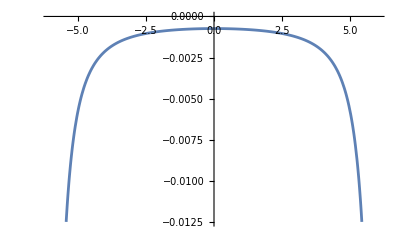

```mathematica
Plot[Hp[1,0,Cos[t],Sin[t],0,1,-Sin[t],Cos[t],R,0,R*Cos[t],R*Sin[t]]+1/(R^2 Pi t^2),{t,-6,6}]
```

```mathematica
NIntegrate[Exp[-t^2]*Gnxnxnynyny[1,0,Cos[t],Sin[t],0,1,-Sin[t],Cos[t],R+10^-3,0,R*Cos[t],R*Sin[t]]-3/4/R Hp[1,0,Cos[t],Sin[t],0,1,-Sin[t],Cos[t],R+10^-3,0,R*Cos[t],R*Sin[t]],{t,-3,3},WorkingPrecision->100,MaxRecursion->100]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

-0.007243870303620447653730960936098884250896262585641516558181503473387220464312948869918895853744525208

```mathematica
tau = {1, 0};
n = {0, 1};
taux = {1, 0};
nx = {0, 1};
x = {0,h};
s = u + 1/24*k^2*u^3+ 1/24*k*kp*u^4+O[u]^5;
y = s*tau - s^2/2*k*n-s^3/6*(kp*n+k^2*tau)+ s^4/24((-kpp+k^3)*n - 3*k*kp*tau)+O[s]^5;
r = x-y;
r2 = uh^2+h^2;
tauy = tau - s*k*n-s^2/2*(kp*n+k^2*tau)+s^3/6*((-kpp+k^3)*n-3*k*kp*tau)+O[u]^4;
ny = n + s*k*tau+s^2/2*(kp*tau - k^2*n)+s^3/6*((kpp-k^3)tau-3*k*kp*n) +O[u]^4;
Gnxnxnynyny =3/(2*Pi)(r.ny)/r2^2 - 6/Pi(r.ny)(r.nx)^2/r2^3+3/Pi(r.ny)(nx.ny)^2/r2^2-12/Pi(r.ny)^2(r.nx)(nx.ny)/r2^3-2/Pi(r.ny)^3/r2^3+12/Pi(r.ny)^3(r.nx)^2/r2^4+3/Pi*(r.nx)(nx.ny)/r2^2 ;
Gnxnxnynyny*D[s,u]// Simplify
```

-(h (h^4+10 h^2 uh^2-15 uh^4))/(2 (π (h^2+uh^2)^4))-((k (12 h^4+13 h^5 k-72 h^2 uh^2-158 h^3 k uh^2+12 uh^4+93 h k uh^4)) u^2)/(16 (π (h^2+uh^2)^4))-((kp (6 h^4+5 h^5 k-36 h^2 uh^2-58 h^3 k uh^2+6 uh^4+33 h k uh^4)) u^3)/(6 (π (h^2+uh^2)^4))+O[u]^4

```mathematica
tau = {1, 0};
n = {0, 1};
taux = {1, 0};
nx = {0, 1};
x = {0,h};
y = s*tau - s^2/2*k*n-s^3/6*(kp*n+k^2*tau)+ s^4/24((-kpp+k^3)*n - 3*k*kp*tau)+O[s]^5;
r = x-y;
r
```

{-s+(k^2 s^3)/6+1/8 k kp s^4+O[s]^5,h+(k s^2)/2+(kp s^3)/6+1/24 (-k^3+kpp) s^4+O[s]^5}

```mathematica
InverseSeries[(1+h k)s^2+1/3 h*kp*s^3+(-k^2+1/12h(-k^3 + kpp))s^4+O[s]^5,u2] // Simplify
```

(√u2)/(√(1+h k))-((h kp) u2)/(6 (1+h k)^2)+1/(72 (1+h k)^(7/2))(36 k^2+39 h k^3+3 h^2 k^4+h (5 h kp^2-3 kpp)-3 h^2 k kpp) u2^(3/2)+O[u2]^2

```mathematica
((h^2 kp^2)/(18 (1+h k)^2)-1/(72 (1+h k)^2)(-36 k^2-39 h k^3-3 h^2 k^4-h^2 kp^2+3 h kpp+3 h^2 k kpp))// Simplify
```

(36 k^2+39 h k^3+3 h^2 k^4+h (5 h kp^2-3 kpp)-3 h^2 k kpp)/(72 (1+h k)^2)

```mathematica
Asymptotic[1/Sqrt[1+h*k],h->0, SeriesTermGoal->4]
```

1-(h k)/2+(3 h^2 k^2)/8-(5 h^3 k^3)/16+(35 h^4 k^4)/128

```mathematica
Asymptotic[-h*kp/6/(1+h*k^2),h->0, SeriesTermGoal->4]
```

-(h kp)/6+1/6 h^2 k^2 kp-1/6 h^3 k^4 kp+1/6 h^4 k^6 kp

```mathematica
Asymptotic[(36 k^2+39 h k^3+3 h^2 k^4+h (5 h kp^2-3 kpp)-3 h^2 k kpp)/(72 (1+h k)^(7/2)),h->0, SeriesTermGoal->4]
```

k^2/2+1/72 h (-87 k^3-3 kpp)+5/144 h^2 (60 k^4+2 kp^2+3 k kpp)-35/576 h^3 (51 k^5+4 k kp^2+3 k^2 kpp)+35/256 h^4 (31 k^6+4 k^2 kp^2+2 k^3 kpp)

```mathematica
tau = {1, 0};
n = {0, 1};
taux = {1, 0};
nx = {0, 1};
x = {0,h};
s = (1 - h*k/2+3*h^2*k^2/8)*u-h*kp/6*u^2+k^2/2*u^3+O[u]^4;
y = s*tau - s^2/2*k*n-s^3/6*(kp*n+k^2*tau)+ s^4/24((-kpp+k^3)*n - 3*k*kp*tau)+O[s]^5;
r = x-y;
r2 = uh^2+h^2;
tauy = tau - s*k*n-s^2/2*(kp*n+k^2*tau)+s^3/6*((-kpp+k^3)*n-3*k*kp*tau)+O[s]^4;
ny = n + s*k*tau+s^2/2*(kp*tau - k^2*n)+s^3/6*((kpp-k^3)tau-3*k*kp*n) +O[s]^4;
Gnxnxnynyny =3/(2*Pi)(r.ny)/r2^2 - 6/Pi(r.ny)(r.nx)^2/r2^3+3/Pi(r.ny)(nx.ny)^2/r2^2-12/Pi(r.ny)^2(r.nx)(nx.ny)/r2^3-2/Pi(r.ny)^3/r2^3+12/Pi(r.ny)^3(r.nx)^2/r2^4+3/Pi*(r.nx)(nx.ny)/r2^2 ;
Gnxnxnynyny*D[s,u]// Simplify
```

-((8-4 h k+3 h^2 k^2) (h^5+10 h^3 uh^2-15 h uh^4))/(16 (π (h^2+uh^2)^4))+(h^2 kp (h^4+10 h^2 uh^2-15 uh^4) u)/(6 π (h^2+uh^2)^4)-1/(2048 (π (h^2+uh^2)^4))3 (k (-81 h^10 k^6+27 h^11 k^7+512 uh^4-3840 h k uh^4-126 h^9 k^5 (-2+3 k^2 uh^2)+320 h^3 k uh^2 (8+25 k^2 uh^2)-192 h^2 uh^2 (16+31 k^2 uh^2)+10 h^8 k^4 (-28+135 k^2 uh^2)+h^7 k^3 (320-4392 k^2 uh^2+243 k^4 uh^4)-8 h^4 (-64-624 k^2 uh^2+675 k^4 uh^4)+4 h^5 k (64-2400 k^2 uh^2+783 k^4 uh^4)+h^6 (192 k^2+6800 k^4 uh^2-945 k^6 uh^4))) u^2+O[u]^3

```mathematica
-((8-4 h k+3 h^2 k^2) (h^5+10 h^3 uh^2-15 h uh^4))/(16 (π (h^2+uh^2)^4))+(h^2 kp (h^4+10 h^2 uh^2-15 uh^4) u)/(6 π (h^2+uh^2)^4)-1/(2048 (π (h^2+uh^2)^4))3 (k (-81 h^10 k^6+27 h^11 k^7+512 uh^4-3840 h k uh^4-126 h^9 k^5 (-2+3 k^2 uh^2)+320 h^3 k uh^2 (8+25 k^2 uh^2)-192 h^2 uh^2 (16+31 k^2 uh^2)+10 h^8 k^4 (-28+135 k^2 uh^2)+h^7 k^3 (320-4392 k^2 uh^2+243 k^4 uh^4)-8 h^4 (-64-624 k^2 uh^2+675 k^4 uh^4)+4 h^5 k (64-2400 k^2 uh^2+783 k^4 uh^4)+h^6 (192 k^2+6800 k^4 uh^2-945 k^6 uh^4))) u^2 /. uh->u
```

(h^2 kp u (h^4+10 h^2 u^2-15 u^4))/(6 π (h^2+u^2)^4)-((8-4 h k+3 h^2 k^2) (h^5+10 h^3 u^2-15 h u^4))/(16 π (h^2+u^2)^4)-1/(2048 π (h^2+u^2)^4)3 k u^2 (-81 h^10 k^6+27 h^11 k^7+512 u^4-3840 h k u^4-126 h^9 k^5 (-2+3 k^2 u^2)+320 h^3 k u^2 (8+25 k^2 u^2)-192 h^2 u^2 (16+31 k^2 u^2)+10 h^8 k^4 (-28+135 k^2 u^2)+h^7 k^3 (320-4392 k^2 u^2+243 k^4 u^4)-8 h^4 (-64-624 k^2 u^2+675 k^4 u^4)+4 h^5 k (64-2400 k^2 u^2+783 k^4 u^4)+h^6 (192 k^2+6800 k^4 u^2-945 k^6 u^4))

```mathematica
tau = {1, 0};
n = {0, 1};
taux = {1, 0};
nx = {0, 1};
x = {0,h};
s = (1 - h*k/2+3*h^2*k^2/8)*u-h*kp/6*u^2+k^2/2*u^3+O[u]^4;
y = s*tau - s^2/2*k*n-s^3/6*(kp*n+k^2*tau)+ s^4/24((-kpp+k^3)*n - 3*k*kp*tau)+O[s]^5;
r = x-y;
r2 = uh^2+h^2;
tauy = tau - s*k*n-s^2/2*(kp*n+k^2*tau)+s^3/6*((-kpp+k^3)*n-3*k*kp*tau)+O[s]^4;
ny = n + s*k*tau+s^2/2*(kp*tau - k^2*n)+s^3/6*((kpp-k^3)tau-3*k*kp*n) +O[s]^4;
Gnxnxnynyny =3/(2*Pi)(r.ny)/r2^2 - 6/Pi(r.ny)(r.nx)^2/r2^3+3/Pi(r.ny)(nx.ny)^2/r2^2-12/Pi(r.ny)^2(r.nx)(nx.ny)/r2^3-2/Pi(r.ny)^3/r2^3+12/Pi(r.ny)^3(r.nx)^2/r2^4+3/Pi*(r.nx)(nx.ny)/r2^2 ;
Gnxnxnynyny*D[s,u]// Simplify
```

-((8-4 h k+3 h^2 k^2) (h^5+10 h^3 uh^2-15 h uh^4))/(16 (π (h^2+uh^2)^4))+(h^2 kp (h^4+10 h^2 uh^2-15 uh^4) u)/(6 π (h^2+uh^2)^4)-1/(2048 (π (h^2+uh^2)^4))3 (k (-81 h^10 k^6+27 h^11 k^7+512 uh^4-3840 h k uh^4-126 h^9 k^5 (-2+3 k^2 uh^2)+320 h^3 k uh^2 (8+25 k^2 uh^2)-192 h^2 uh^2 (16+31 k^2 uh^2)+10 h^8 k^4 (-28+135 k^2 uh^2)+h^7 k^3 (320-4392 k^2 uh^2+243 k^4 uh^4)-8 h^4 (-64-624 k^2 uh^2+675 k^4 uh^4)+4 h^5 k (64-2400 k^2 uh^2+783 k^4 uh^4)+h^6 (192 k^2+6800 k^4 uh^2-945 k^6 uh^4))) u^2+O[u]^3

```mathematica
-((8-4 h k+3 h^2 k^2) (h^5+10 h^3 uh^2-15 h uh^4))/(16 (π (h^2+uh^2)^4))+(h^2 kp (h^4+10 h^2 uh^2-15 uh^4) u)/(6 π (h^2+uh^2)^4)-1/(2048 (π (h^2+uh^2)^4))3 (k (-81 h^10 k^6+27 h^11 k^7+512 uh^4-3840 h k uh^4-126 h^9 k^5 (-2+3 k^2 uh^2)+320 h^3 k uh^2 (8+25 k^2 uh^2)-192 h^2 uh^2 (16+31 k^2 uh^2)+10 h^8 k^4 (-28+135 k^2 uh^2)+h^7 k^3 (320-4392 k^2 uh^2+243 k^4 uh^4)-8 h^4 (-64-624 k^2 uh^2+675 k^4 uh^4)+4 h^5 k (64-2400 k^2 uh^2+783 k^4 uh^4)+h^6 (192 k^2+6800 k^4 uh^2-945 k^6 uh^4))) u^2 /. uh->u
```

(h^2 kp u (h^4+10 h^2 u^2-15 u^4))/(6 π (h^2+u^2)^4)-((8-4 h k+3 h^2 k^2) (h^5+10 h^3 u^2-15 h u^4))/(16 π (h^2+u^2)^4)-1/(2048 π (h^2+u^2)^4)3 k u^2 (-81 h^10 k^6+27 h^11 k^7+512 u^4-3840 h k u^4-126 h^9 k^5 (-2+3 k^2 u^2)+320 h^3 k u^2 (8+25 k^2 u^2)-192 h^2 u^2 (16+31 k^2 u^2)+10 h^8 k^4 (-28+135 k^2 u^2)+h^7 k^3 (320-4392 k^2 u^2+243 k^4 u^4)-8 h^4 (-64-624 k^2 u^2+675 k^4 u^4)+4 h^5 k (64-2400 k^2 u^2+783 k^4 u^4)+h^6 (192 k^2+6800 k^4 u^2-945 k^6 u^4))

```mathematica
Integrate[(h^2 kp u (h^4+10 h^2 u^2-15 u^4))/(6 π (h^2+u^2)^4)-((8-4 h k+3 h^2 k^2) (h^5+10 h^3 u^2-15 h u^4))/(16 π (h^2+u^2)^4)-1/(2048 π (h^2+u^2)^4)3 k u^2 (-81 h^10 k^6+27 h^11 k^7+512 u^4-3840 h k u^4-126 h^9 k^5 (-2+3 k^2 u^2)+320 h^3 k u^2 (8+25 k^2 u^2)-192 h^2 u^2 (16+31 k^2 u^2)+10 h^8 k^4 (-28+135 k^2 u^2)+h^7 k^3 (320-4392 k^2 u^2+243 k^4 u^4)-8 h^4 (-64-624 k^2 u^2+675 k^4 u^4)+4 h^5 k (64-2400 k^2 u^2+783 k^4 u^4)+h^6 (192 k^2+6800 k^4 u^2-945 k^6 u^4)),u]
```

1/(6144 π)(1/((h^2+u^2)^3)(-1944 h^10 k^7 u+486 h^11 k^8 u+4608 k u^5+405 h^9 k^6 u (16+3 k^2 u^2)-768 h u^3 (20+33 k^2 u^2)-9 h^8 k^5 u (1280+549 k^2 u^2)-192 h^2 u^3 (-32 k-40 kp u+207 k^3 u^2)+27 h^7 k^4 u (640+612 k^2 u^2+63 k^4 u^4)+192 h^3 u (-16-162 k^2 u^2+285 k^4 u^4)+12 h^5 k^2 u (-864+3760 k^2 u^2+1809 k^4 u^4)-8 h^4 u (-192 k-640 kp u+4680 k^3 u^2+4635 k^5 u^4)+3 h^6 (512 kp-3 k^3 u (1536+3320 k^2 u^2+729 k^4 u^4)))+18 k^2 (-512-768 h k+960 h^2 k^2-640 h^3 k^3+360 h^4 k^4-108 h^5 k^5+27 h^6 k^6) ArcTan[h/u])

```mathematica
Integrate[Integrate[Integrate[(h^2 kp u (h^4+10 h^2 u^2-15 u^4))/(6 π (h^2+u^2)^4)-((8-4 h k+3 h^2 k^2) (h^5+10 h^3 u^2-15 h u^4))/(16 π (h^2+u^2)^4)-1/(2048 π (h^2+u^2)^4)3 k u^2 (-81 h^10 k^6+27 h^11 k^7+512 u^4-3840 h k u^4-126 h^9 k^5 (-2+3 k^2 u^2)+320 h^3 k u^2 (8+25 k^2 u^2)-192 h^2 u^2 (16+31 k^2 u^2)+10 h^8 k^4 (-28+135 k^2 u^2)+h^7 k^3 (320-4392 k^2 u^2+243 k^4 u^4)-8 h^4 (-64-624 k^2 u^2+675 k^4 u^4)+4 h^5 k (64-2400 k^2 u^2+783 k^4 u^4)+h^6 (192 k^2+6800 k^4 u^2-945 k^6 u^4)),u],u],u]
```

1/(12288 π (h^2+u^2))(-1024 h^4 kp-3072 h u-9216 h^2 k u+61056 h^3 k^2 u+97344 h^4 k^3 u-133440 h^5 k^4 u+90360 h^6 k^5 u-52812 h^7 k^6 u+15957 h^8 k^7 u-4131 h^9 k^8 u-9216 k u^3+59904 h k^2 u^3+93312 h^2 k^3 u^3-126720 h^3 k^4 u^3+85680 h^4 k^5 u^3-49896 h^5 k^6 u^3+15066 h^6 k^7 u^3-3888 h^7 k^8 u^3+2 (h^2+u^2) (-972 h^7 k^7+243 h^8 k^8-4608 k^2 u^2-256 h u (16 kp+27 k^3 u)+1080 h^4 k^4 (8+3 k^2 u^2)+81 h^6 k^6 (40+3 k^2 u^2)-1152 h^3 k^3 (6+5 k^2 u^2)+576 h^2 k^2 (-8+15 k^2 u^2)-36 h^5 k^5 (160+27 k^2 u^2)) ArcTan[h/u]+6 (2048+2048 h k-14592 h^2 k^2-24192 h^3 k^3+33600 h^4 k^4-22800 h^5 k^5+13392 h^6 k^6-4050 h^7 k^7+1053 h^8 k^8) (h^2+u^2) ArcTan[u/h]-7680 h^4 kp Log[h^2+u^2]+4608 h^2 k u Log[h^2+u^2]-34560 h^3 k^2 u Log[h^2+u^2]-53568 h^4 k^3 u Log[h^2+u^2]+72000 h^5 k^4 u Log[h^2+u^2]-48600 h^6 k^5 u Log[h^2+u^2]+28188 h^7 k^6 u Log[h^2+u^2]-8505 h^8 k^7 u Log[h^2+u^2]+2187 h^9 k^8 u Log[h^2+u^2]-7680 h^2 kp u^2 Log[h^2+u^2]+4608 k u^3 Log[h^2+u^2]-34560 h k^2 u^3 Log[h^2+u^2]-53568 h^2 k^3 u^3 Log[h^2+u^2]+72000 h^3 k^4 u^3 Log[h^2+u^2]-48600 h^4 k^5 u^3 Log[h^2+u^2]+28188 h^5 k^6 u^3 Log[h^2+u^2]-8505 h^6 k^7 u^3 Log[h^2+u^2]+2187 h^7 k^8 u^3 Log[h^2+u^2])

```mathematica
tau = {1, 0};
n = {0, 1};
taux = {1, 0};
tx = {1, 0};
nx = {0, 1};
x = {0,h};
s = (1 - h*k/2+3*h^2*k^2/8)*u-h*kp/6*u^2+k^2/2*u^3+O[u]^4;
y = s*tau - s^2/2*k*n-s^3/6*(kp*n+k^2*tau)+ s^4/24((-kpp+k^3)*n - 3*k*kp*tau)+O[s]^5;
r = x-y;
r2 = uh^2+h^2;
tauy = tau - s*k*n-s^2/2*(kp*n+k^2*tau)+s^3/6*((-kpp+k^3)*n-3*k*kp*tau)+O[s]^4;
ty = tauy;
ny = n + s*k*tau+s^2/2*(kp*tau - k^2*n)+s^3/6*((kpp-k^3)tau-3*k*kp*n) +O[s]^4;
```

```mathematica
D[s,u]
```

(1-(h k)/2+(3 h^2 k^2)/8)-1/3 (h kp) u+(3 k^2 u^2)/2+O[u]^3

```mathematica
Gnxnxnynyny =3/(2*Pi)(r.ny)/r2^2 - 6/Pi(r.ny)(r.nx)^2/r2^3+3/Pi(r.ny)(nx.ny)^2/r2^2-12/Pi(r.ny)^2(r.nx)(nx.ny)/r2^3-2/Pi(r.ny)^3/r2^3+12/Pi(r.ny)^3(r.nx)^2/r2^4+3/Pi*(r.nx)(nx.ny)/r2^2 ;
Gnxnxnynyny= 3/(2*Pi)(r.ny)/r2^2 - 6/Pi(r.ny)(r.nx)^2/r2^3+3/Pi(r.ny)(nx.ny)^2/r2^2-12/Pi(r.ny)^2(r.nx)(nx.ny)/r2^3-2/Pi(r.ny)^3/r2^3+12/Pi(r.ny)^3(r.nx)^2/r2^4+3/Pi*(r.nx)(nx.ny)/r2^2;
Gtxtxnynyny= 3/(2*Pi)(r.ny)/r2^2 - 6/Pi(r.ny)(r.tx)^2/r2^3+3/Pi(r.ny)(tx.ny)^2/r2^2-12/Pi(r.ny)^2(r.tx)(tx.ny)/r2^3-2/Pi(r.ny)^3/r2^3+12/Pi(r.ny)^3(r.tx)^2/r2^4+3/Pi*(r.tx)(tx.ny)/r2^2;
Gnxnxtytyty= 3/(2*Pi)(r.ty)/r2^2 - 6/Pi(r.ty)(r.nx)^2/r2^3+3/Pi(r.ty)(nx.ty)^2/r2^2-12/Pi(r.ty)^2(r.nx)(nx.ty)/r2^3-2/Pi(r.ty)^3/r2^3+12/Pi(r.ty)^3(r.nx)^2/r2^4+3/Pi*(r.nx)(nx.ty)/r2^2;
Gtxtxtytyty= 3/(2*Pi)(r.ty)/r2^2 - 6/Pi(r.ty)(r.tx)^2/r2^3+3/Pi(r.ty)(tx.ty)^2/r2^2-12/Pi(r.ty)^2(r.tx)(tx.ty)/r2^3-2/Pi(r.ty)^3/r2^3+12/Pi(r.ty)^3(r.tx)^2/r2^4+3/Pi*(r.tx)(tx.ty)/r2^2;
Gnxnxnytyty=2/Pi*(nx.ny)(nx.tauy)(r.tauy)/r2^2-4/Pi(nx.ny)(r.tauy)^2(r.nx)/r2^3+1/Pi(r.ny)(nx.tauy)^2/r2^2-8/Pi(r.ny)(r.tauy)(r.nx)(nx.tauy)/r2^3-2/Pi(r.ny)(r.tauy)^2/r2^3+12/Pi(r.ny)(r.tauy)^2(r.nx)^2/r2^4+1/Pi(nx.ny)(r.nx)/r2^2+1/(2Pi)(r.ny)/r2^2-2/Pi(r.ny)(r.nx)^2/r2^3;
Gtxtxnytyty=2/Pi*(tx.ny)(tx.tauy)(r.tauy)/r2^2-4/Pi(tx.ny)(r.tauy)^2(r.tx)/r2^3+1/Pi(r.ny)(tx.tauy)^2/r2^2-8/Pi(r.ny)(r.tauy)(r.tx)(tx.tauy)/r2^3-2/Pi(r.ny)(r.tauy)^2/r2^3+12/Pi(r.ny)(r.tauy)^2(r.tx)^2/r2^4+1/Pi(tx.ny)(r.tx)/r2^2+1/(2Pi)(r.ny)/r2^2-2/Pi(r.ny)(r.tx)^2/r2^3;
Gnxnxnynyty = 2/Pi(nx.tauy)(nx.ny)(r.ny)/r2^2-4/Pi(nx.tauy)(r.ny)^2(r.nx)/r2^3+1/Pi(r.tauy)(nx.ny)^2/r2^2-8/Pi(r.tauy)(r.ny)(r.nx)(nx.ny)/r2^3-2/Pi(r.tauy)(r.ny)^2/r2^3+12/Pi(r.tauy)(r.ny)^2(r.nx)^2/r2^4+1/Pi(nx.tauy)(r.nx)/r2^2+1/(2Pi)(r.tauy)/r2^2-2/Pi(r.tauy)(r.nx)^2/r2^3;
Gtxtxnynyty = 2/Pi(taux.tauy)(taux.ny)(r.ny)/r2^2-4/Pi(taux.tauy)(r.ny)^2(r.taux)/r2^3+1/Pi(r.tauy)(taux.ny)^2/r2^2-8/Pi(r.tauy)(r.ny)(r.taux)(taux.ny)/r2^3-2/Pi(r.tauy)(r.ny)^2/r2^3+12/Pi(r.tauy)(r.ny)^2(r.taux)^2/r2^4+1/Pi(taux.tauy)(r.taux)/r2^2+1/(2Pi)(r.tauy)/r2^2-2/Pi(r.tauy)(r.taux)^2/r2^3;
H = (r.tauy)/r2;
Hp = 1/Pi*(tauy.taux)/r2 - 2(r.taux)(r.tauy)/r2^2;
```

```mathematica
Normal[H*D[s,u]]/. uh->u // Expand
```

-u/(h^2+u^2)-(5 h^3 k^3 u)/(8 (h^2+u^2))+(15 h^4 k^4 u)/(64 (h^2+u^2))-(9 h^5 k^5 u)/(64 (h^2+u^2))+(h^2 k kp u^2)/(h^2+u^2)-(h^3 k^2 kp u^2)/(h^2+u^2)+(13 h^4 k^3 kp u^2)/(16 (h^2+u^2))-(45 h^5 k^4 kp u^2)/(128 (h^2+u^2))+(27 h^6 k^5 kp u^2)/(256 (h^2+u^2))-(27 h^7 k^6 kp u^2)/(1024 (h^2+u^2))-(11 k^2 u^3)/(6 (h^2+u^2))-(7 h k^3 u^3)/(6 (h^2+u^2))+(5 h^2 k^4 u^3)/(12 (h^2+u^2))-(17 h^3 k^5 u^3)/(24 (h^2+u^2))-(23 h^4 k^6 u^3)/(192 (h^2+u^2))+(h^5 k^7 u^3)/(6 (h^2+u^2))-(13 h^6 k^8 u^3)/(128 (h^2+u^2))+(27 h^7 k^9 u^3)/(512 (h^2+u^2))-(117 h^8 k^10 u^3)/(8192 (h^2+u^2))+(27 h^9 k^11 u^3)/(8192 (h^2+u^2))+(5 h^2 kp^2 u^3)/(18 (h^2+u^2))-(7 h^3 k kp^2 u^3)/(18 (h^2+u^2))+(h^4 k^2 kp^2 u^3)/(3 (h^2+u^2))-(h^5 k^3 kp^2 u^3)/(8 (h^2+u^2))+(3 h^6 k^4 kp^2 u^3)/(64 (h^2+u^2))-(h kpp u^3)/(6 (h^2+u^2))+(h^2 k kpp u^3)/(3 (h^2+u^2))-(h^3 k^2 kpp u^3)/(2 (h^2+u^2))+(11 h^4 k^3 kpp u^3)/(24 (h^2+u^2))-(65 h^5 k^4 kpp u^3)/(192 (h^2+u^2))+(11 h^6 k^5 kpp u^3)/(64 (h^2+u^2))-(9 h^7 k^6 kpp u^3)/(128 (h^2+u^2))+(9 h^8 k^7 kpp u^3)/(512 (h^2+u^2))-(27 h^9 k^8 kpp u^3)/(8192 (h^2+u^2))

```mathematica
Asymptotic[Integrate[Normal[H*D[s,u]]/. uh->u,u],h->0, SeriesTermGoal->1]
```

$Aborted

```mathematica
Asymptotic[Integrate[Integrate[Normal[Gnxnxnynyny*D[s,u]]/. uh->u,u],u] ,h->0]
```

$Aborted

```mathematica
Asymptotic[Integrate[Integrate[Integrate[Normal[Gnxnxnynyty*D[s,u]]/. uh->u,u],u] ,u],h->0]
```

$Aborted

```mathematica
Asymptotic[Integrate[Integrate[Integrate[Normal[Gnxnxnytyty*D[s,u]]/. uh->u,u] ,u],u],h->0]
```

(9 k u)/(4 π)-(9 k u Log[u^2])/(8 π)

```mathematica
Integrate[Integrate[Integrate[Normal[Gtxtxnynyny*D[s,u]]/. uh->u,u],u],u]
```

-1/(12288 π)(-1/(h^2+u^2)6 u (-1053 h^8 k^7+162 h^9 k^8-7680 k u^2+81 h^7 k^6 (47+2 k^2 u^2)-2112 h^2 k (4+9 k^2 u^2)+512 h (1+36 k^2 u^2)+60 h^5 k^4 (262+63 k^2 u^2)+192 h^3 k^2 (101+80 k^2 u^2)-3 h^6 k^5 (3116+351 k^2 u^2)-8 h^4 k^3 (2456+1155 k^2 u^2))+2 (-972 h^7 k^7+243 h^8 k^8+6912 k^2 u^2+256 h u (4 kp-27 k^3 u)+1080 h^4 k^4 (8+3 k^2 u^2)+81 h^6 k^6 (40+3 k^2 u^2)+1728 h^2 k^2 (4+5 k^2 u^2)-1152 h^3 k^3 (6+5 k^2 u^2)-36 h^5 k^5 (160+27 k^2 u^2)) ArcTan[h/u]+3 (2048-27136 h k+58368 h^2 k^2-58560 h^3 k^3+45360 h^4 k^4-26448 h^5 k^5+10422 h^6 k^6-2835 h^7 k^7+405 h^8 k^8) ArcTan[u/h]+3 (-7680 k u+20736 h k^2 u+18240 h^3 k^4 u-11160 h^4 k^5 u+4860 h^5 k^6 u-1377 h^6 k^7 u+243 h^7 k^8 u+64 h^2 (8 kp-333 k^3 u)) Log[h^2+u^2])

```mathematica
Normal[Gnxnxnytyty*D[s,u]]/. uh->u//Expand
```

(12 h^3 u^2)/(π (h^2+u^2)^4)+(6 h^4 k u^2)/(π (h^2+u^2)^4)-(3 h^5 k^2 u^2)/(2 π (h^2+u^2)^4)+(12 h^6 k^3 u^2)/(π (h^2+u^2)^4)+(15 h^7 k^4 u^2)/(16 π (h^2+u^2)^4)-(21 h^8 k^5 u^2)/(32 π (h^2+u^2)^4)+(513 h^9 k^6 u^2)/(128 π (h^2+u^2)^4)-(81 h^10 k^7 u^2)/(64 π (h^2+u^2)^4)+(81 h^11 k^8 u^2)/(128 π (h^2+u^2)^4)-(2 h^3)/(π (h^2+u^2)^3)+(h^4 k)/(π (h^2+u^2)^3)-(3 h^5 k^2)/(4 π (h^2+u^2)^3)+(2 h^4 kp u)/(3 π (h^2+u^2)^3)-(6 h u^2)/(π (h^2+u^2)^3)-(12 h^2 k u^2)/(π (h^2+u^2)^3)+(17 h^3 k^2 u^2)/(4 π (h^2+u^2)^3)-(99 h^4 k^3 u^2)/(8 π (h^2+u^2)^3)-(75 h^5 k^4 u^2)/(32 π (h^2+u^2)^3)+(11 h^6 k^5 u^2)/(4 π (h^2+u^2)^3)-(1287 h^7 k^6 u^2)/(256 π (h^2+u^2)^3)+(837 h^8 k^7 u^2)/(512 π (h^2+u^2)^3)-(351 h^9 k^8 u^2)/(512 π (h^2+u^2)^3)+(3 h)/(2 π (h^2+u^2)^2)-(3 h^2 k)/(4 π (h^2+u^2)^2)+(9 h^3 k^2)/(16 π (h^2+u^2)^2)-(h^2 kp u)/(2 π (h^2+u^2)^2)+(9 k u^2)/(4 π (h^2+u^2)^2)+(9 h k^2 u^2)/(8 π (h^2+u^2)^2)+(27 h^2 k^3 u^2)/(32 π (h^2+u^2)^2)+(45 h^3 k^4 u^2)/(32 π (h^2+u^2)^2)-(315 h^4 k^5 u^2)/(256 π (h^2+u^2)^2)+(567 h^5 k^6 u^2)/(512 π (h^2+u^2)^2)-(729 h^6 k^7 u^2)/(2048 π (h^2+u^2)^2)+(243 h^7 k^8 u^2)/(2048 π (h^2+u^2)^2)

```mathematica
Integrate[Integrate[Integrate[(12 h^3 u^2)/(π (h^2+u^2)^4)-(2 h^3)/(π (h^2+u^2)^3)-(6 h u^2)/(π (h^2+u^2)^3)+(3 h)/(2 π (h^2+u^2)^2),u],u],u]
```

-(h (-u/(h^2+u^2)+(2 ArcTan[u/h])/h))/(4 π)

```mathematica
Normal[Gtxtxnytyty*D[s,u]]/. uh->u//Expand
```

-(12 h u^2)/(π (h^2+u^2)^3)+(6 h^2 k u^2)/(π (h^2+u^2)^3)-(13 h^3 k^2 u^2)/(2 π (h^2+u^2)^3)-(9 h^4 k^3 u^2)/(2 π (h^2+u^2)^3)+(45 h^5 k^4 u^2)/(16 π (h^2+u^2)^3)-(109 h^6 k^5 u^2)/(32 π (h^2+u^2)^3)+(63 h^7 k^6 u^2)/(128 π (h^2+u^2)^3)-(27 h^8 k^7 u^2)/(128 π (h^2+u^2)^3)-(27 h^9 k^8 u^2)/(256 π (h^2+u^2)^3)+(3 h)/(2 π (h^2+u^2)^2)-(3 h^2 k)/(4 π (h^2+u^2)^2)+(9 h^3 k^2)/(16 π (h^2+u^2)^2)-(h^2 kp u)/(2 π (h^2+u^2)^2)-(15 k u^2)/(4 π (h^2+u^2)^2)+(33 h k^2 u^2)/(8 π (h^2+u^2)^2)-(45 h^2 k^3 u^2)/(32 π (h^2+u^2)^2)-(75 h^3 k^4 u^2)/(32 π (h^2+u^2)^2)+(525 h^4 k^5 u^2)/(256 π (h^2+u^2)^2)-(945 h^5 k^6 u^2)/(512 π (h^2+u^2)^2)+(1215 h^6 k^7 u^2)/(2048 π (h^2+u^2)^2)-(405 h^7 k^8 u^2)/(2048 π (h^2+u^2)^2)

```mathematica
Integrate[Integrate[Integrate[-(12 h u^2)/(π (h^2+u^2)^3)+(3 h)/(2 π (h^2+u^2)^2),u],u],u]
```

(3 ((h u)/2-5/2 h^2 ArcTan[u/h]-1/2 u^2 ArcTan[u/h]))/(4 h^2 π)

```mathematica
tau = {-1, 0};
n = {0, 1};
taux = {-1, 0};
tx = {-1, 0};
nx = {0, 1};
x = {0,h};
s = (1 - h*k/2+3*h^2*k^2/8)*u-h*kp/6*u^2+k^2/2*u^3+O[u]^4;
y = s*tau - s^2/2*k*n-s^3/6*(kp*n+k^2*tau)+ s^4/24((-kpp+k^3)*n - 3*k*kp*tau)+O[s]^5;
r = x-y;
r2 = uh^2+h^2;
tauy = tau - s*k*n-s^2/2*(kp*n+k^2*tau)+s^3/6*((-kpp+k^3)*n-3*k*kp*tau)+O[s]^5;
ty = tauy;
ny = n + s*k*tau+s^2/2*(kp*tau - k^2*n)+s^3/6*((kpp-k^3)tau-3*k*kp*n) +O[s]^5;
Gnxnxnynyny =3/(2*Pi)(r.ny)/r2^2 - 6/Pi(r.ny)(r.nx)^2/r2^3+3/Pi(r.ny)(nx.ny)^2/r2^2-12/Pi(r.ny)^2(r.nx)(nx.ny)/r2^3-2/Pi(r.ny)^3/r2^3+12/Pi(r.ny)^3(r.nx)^2/r2^4+3/Pi*(r.nx)(nx.ny)/r2^2 ;
Gnxnxnynyny= 3/(2*Pi)(r.ny)/r2^2 - 6/Pi(r.ny)(r.nx)^2/r2^3+3/Pi(r.ny)(nx.ny)^2/r2^2-12/Pi(r.ny)^2(r.nx)(nx.ny)/r2^3-2/Pi(r.ny)^3/r2^3+12/Pi(r.ny)^3(r.nx)^2/r2^4+3/Pi*(r.nx)(nx.ny)/r2^2;
Gtxtxnynyny= 3/(2*Pi)(r.ny)/r2^2 - 6/Pi(r.ny)(r.tx)^2/r2^3+3/Pi(r.ny)(tx.ny)^2/r2^2-12/Pi(r.ny)^2(r.tx)(tx.ny)/r2^3-2/Pi(r.ny)^3/r2^3+12/Pi(r.ny)^3(r.tx)^2/r2^4+3/Pi*(r.tx)(tx.ny)/r2^2;
Gnxnxtytyty= 3/(2*Pi)(r.ty)/r2^2 - 6/Pi(r.ty)(r.nx)^2/r2^3+3/Pi(r.ty)(nx.ty)^2/r2^2-12/Pi(r.ty)^2(r.nx)(nx.ty)/r2^3-2/Pi(r.ty)^3/r2^3+12/Pi(r.ty)^3(r.nx)^2/r2^4+3/Pi*(r.nx)(nx.ty)/r2^2;
Gtxtxtytyty= 3/(2*Pi)(r.ty)/r2^2 - 6/Pi(r.ty)(r.tx)^2/r2^3+3/Pi(r.ty)(tx.ty)^2/r2^2-12/Pi(r.ty)^2(r.tx)(tx.ty)/r2^3-2/Pi(r.ty)^3/r2^3+12/Pi(r.ty)^3(r.tx)^2/r2^4+3/Pi*(r.tx)(tx.ty)/r2^2;
Gnxnxnytyty=2/Pi*(nx.ny)(nx.tauy)(r.tauy)/r2^2-4/Pi(nx.ny)(r.tauy)^2(r.nx)/r2^3+1/Pi(r.ny)(nx.tauy)^2/r2^2-8/Pi(r.ny)(r.tauy)(r.nx)(nx.tauy)/r2^3-2/Pi(r.ny)(r.tauy)^2/r2^3+12/Pi(r.ny)(r.tauy)^2(r.nx)^2/r2^4+1/Pi(nx.ny)(r.nx)/r2^2+1/(2Pi)(r.ny)/r2^2-2/Pi(r.ny)(r.nx)^2/r2^3;
Gtxtxnytyty=2/Pi*(tx.ny)(tx.tauy)(r.tauy)/r2^2-4/Pi(tx.ny)(r.tauy)^2(r.tx)/r2^3+1/Pi(r.ny)(tx.tauy)^2/r2^2-8/Pi(r.ny)(r.tauy)(r.tx)(tx.tauy)/r2^3-2/Pi(r.ny)(r.tauy)^2/r2^3+12/Pi(r.ny)(r.tauy)^2(r.tx)^2/r2^4+1/Pi(tx.ny)(r.tx)/r2^2+1/(2Pi)(r.ny)/r2^2-2/Pi(r.ny)(r.tx)^2/r2^3;
Gnxnxnynyty = 2/Pi(nx.tauy)(nx.ny)(r.ny)/r2^2-4/Pi(nx.tauy)(r.ny)^2(r.nx)/r2^3+1/Pi(r.tauy)(nx.ny)^2/r2^2-8/Pi(r.tauy)(r.ny)(r.nx)(nx.ny)/r2^3-2/Pi(r.tauy)(r.ny)^2/r2^3+12/Pi(r.tauy)(r.ny)^2(r.nx)^2/r2^4+1/Pi(nx.tauy)(r.nx)/r2^2+1/(2Pi)(r.tauy)/r2^2-2/Pi(r.tauy)(r.nx)^2/r2^3;
Gtxtxnynyty = 2/Pi(taux.tauy)(taux.ny)(r.ny)/r2^2-4/Pi(taux.tauy)(r.ny)^2(r.taux)/r2^3+1/Pi(r.tauy)(taux.ny)^2/r2^2-8/Pi(r.tauy)(r.ny)(r.taux)(taux.ny)/r2^3-2/Pi(r.tauy)(r.ny)^2/r2^3+12/Pi(r.tauy)(r.ny)^2(r.taux)^2/r2^4+1/Pi(taux.tauy)(r.taux)/r2^2+1/(2Pi)(r.tauy)/r2^2-2/Pi(r.tauy)(r.taux)^2/r2^3;
H = 1/Pi(r.tauy)/r2;
Hp = 1/Pi*(tauy.taux)/r2 - 2/Pi(r.taux)(r.tauy)/r2^2;
```

```mathematica
Normal[Gnxnxnynyny ] /. uh->u// Expand
```

(12 h^5)/(π (h^2+u^2)^4)-(6 h^4 k u^2)/(π (h^2+u^2)^4)-(12 h^5 k^2 u^2)/(π (h^2+u^2)^4)+(12 h^6 k^3 u^2)/(π (h^2+u^2)^4)-(63 h^7 k^4 u^2)/(4 π (h^2+u^2)^4)+(189 h^8 k^5 u^2)/(32 π (h^2+u^2)^4)-(81 h^9 k^6 u^2)/(32 π (h^2+u^2)^4)-(8 h^4 kp u^3)/(π (h^2+u^2)^4)-(4 h^5 k kp u^3)/(π (h^2+u^2)^4)+(17 h^6 k^2 kp u^3)/(π (h^2+u^2)^4)-(26 h^7 k^3 kp u^3)/(π (h^2+u^2)^4)+(153 h^8 k^4 kp u^3)/(8 π (h^2+u^2)^4)-(351 h^9 k^5 kp u^3)/(32 π (h^2+u^2)^4)+(27 h^10 k^6 kp u^3)/(8 π (h^2+u^2)^4)-(243 h^11 k^7 kp u^3)/(256 π (h^2+u^2)^4)-(6 h^3 k^2 u^4)/(π (h^2+u^2)^4)+(13 h^4 k^3 u^4)/(2 π (h^2+u^2)^4)-(25 h^5 k^4 u^4)/(π (h^2+u^2)^4)+(27 h^6 k^5 u^4)/(4 π (h^2+u^2)^4)+(107 h^7 k^6 u^4)/(16 π (h^2+u^2)^4)-(1123 h^8 k^7 u^4)/(64 π (h^2+u^2)^4)+(975 h^9 k^8 u^4)/(64 π (h^2+u^2)^4)-(135 h^10 k^9 u^4)/(16 π (h^2+u^2)^4)+(7425 h^11 k^10 u^4)/(2048 π (h^2+u^2)^4)-(7695 h^12 k^11 u^4)/(8192 π (h^2+u^2)^4)+(729 h^13 k^12 u^4)/(4096 π (h^2+u^2)^4)+(4 h^5 kp^2 u^4)/(π (h^2+u^2)^4)+(29 h^6 k kp^2 u^4)/(6 π (h^2+u^2)^4)-(11 h^7 k^2 kp^2 u^4)/(2 π (h^2+u^2)^4)+(15 h^8 k^3 kp^2 u^4)/(2 π (h^2+u^2)^4)-(45 h^9 k^4 kp^2 u^4)/(16 π (h^2+u^2)^4)+(81 h^10 k^5 kp^2 u^4)/(64 π (h^2+u^2)^4)-(7 h^4 kpp u^4)/(2 π (h^2+u^2)^4)+(7 h^5 k kpp u^4)/(π (h^2+u^2)^4)-(21 h^6 k^2 kpp u^4)/(2 π (h^2+u^2)^4)+(77 h^7 k^3 kpp u^4)/(8 π (h^2+u^2)^4)-(455 h^8 k^4 kpp u^4)/(64 π (h^2+u^2)^4)+(231 h^9 k^5 kpp u^4)/(64 π (h^2+u^2)^4)-(189 h^10 k^6 kpp u^4)/(128 π (h^2+u^2)^4)+(189 h^11 k^7 kpp u^4)/(512 π (h^2+u^2)^4)-(567 h^12 k^8 kpp u^4)/(8192 π (h^2+u^2)^4)-(20 h^3)/(π (h^2+u^2)^3)+(6 h^2 k u^2)/(π (h^2+u^2)^3)+(18 h^3 k^2 u^2)/(π (h^2+u^2)^3)-(18 h^4 k^3 u^2)/(π (h^2+u^2)^3)+(87 h^5 k^4 u^2)/(4 π (h^2+u^2)^3)-(261 h^6 k^5 u^2)/(32 π (h^2+u^2)^3)+(27 h^7 k^6 u^2)/(8 π (h^2+u^2)^3)+(8 h^2 kp u^3)/(π (h^2+u^2)^3)+(10 h^3 k kp u^3)/(π (h^2+u^2)^3)-(28 h^4 k^2 kp u^3)/(π (h^2+u^2)^3)+(153 h^5 k^3 kp u^3)/(4 π (h^2+u^2)^3)-(219 h^6 k^4 kp u^3)/(8 π (h^2+u^2)^3)+(243 h^7 k^5 kp u^3)/(16 π (h^2+u^2)^3)-(297 h^8 k^6 kp u^3)/(64 π (h^2+u^2)^3)+(81 h^9 k^7 kp u^3)/(64 π (h^2+u^2)^3)+(3 h k^2 u^4)/(π (h^2+u^2)^3)-(7 h^2 k^3 u^4)/(2 π (h^2+u^2)^3)+(53 h^3 k^4 u^4)/(2 π (h^2+u^2)^3)-(15 h^4 k^5 u^4)/(2 π (h^2+u^2)^3)-(217 h^5 k^6 u^4)/(32 π (h^2+u^2)^3)+(1195 h^6 k^7 u^4)/(64 π (h^2+u^2)^3)-(1053 h^7 k^8 u^4)/(64 π (h^2+u^2)^3)+(2313 h^8 k^9 u^4)/(256 π (h^2+u^2)^3)-(16389 h^9 k^10 u^4)/(4096 π (h^2+u^2)^3)+(8505 h^10 k^11 u^4)/(8192 π (h^2+u^2)^3)-(1701 h^11 k^12 u^4)/(8192 π (h^2+u^2)^3)-(4 h^3 kp^2 u^4)/(π (h^2+u^2)^3)-(47 h^4 k kp^2 u^4)/(6 π (h^2+u^2)^3)+(26 h^5 k^2 kp^2 u^4)/(3 π (h^2+u^2)^3)-(21 h^6 k^3 kp^2 u^4)/(2 π (h^2+u^2)^3)+(63 h^7 k^4 kp^2 u^4)/(16 π (h^2+u^2)^3)-(27 h^8 k^5 kp^2 u^4)/(16 π (h^2+u^2)^3)+(7 h^2 kpp u^4)/(2 π (h^2+u^2)^3)-(7 h^3 k kpp u^4)/(π (h^2+u^2)^3)+(21 h^4 k^2 kpp u^4)/(2 π (h^2+u^2)^3)-(77 h^5 k^3 kpp u^4)/(8 π (h^2+u^2)^3)+(455 h^6 k^4 kpp u^4)/(64 π (h^2+u^2)^3)-(231 h^7 k^5 kpp u^4)/(64 π (h^2+u^2)^3)+(189 h^8 k^6 kpp u^4)/(128 π (h^2+u^2)^3)-(189 h^9 k^7 kpp u^4)/(512 π (h^2+u^2)^3)+(567 h^10 k^8 kpp u^4)/(8192 π (h^2+u^2)^3)+(15 h)/(2 π (h^2+u^2)^2)-(3 k u^2)/(4 π (h^2+u^2)^2)-(6 h k^2 u^2)/(π (h^2+u^2)^2)+(6 h^2 k^3 u^2)/(π (h^2+u^2)^2)-(207 h^3 k^4 u^2)/(32 π (h^2+u^2)^2)+(621 h^4 k^5 u^2)/(256 π (h^2+u^2)^2)-(243 h^5 k^6 u^2)/(256 π (h^2+u^2)^2)-(kp u^3)/(π (h^2+u^2)^2)-(5 h k kp u^3)/(π (h^2+u^2)^2)+(83 h^2 k^2 kp u^3)/(8 π (h^2+u^2)^2)-(199 h^3 k^3 kp u^3)/(16 π (h^2+u^2)^2)+(549 h^4 k^4 kp u^3)/(64 π (h^2+u^2)^2)-(1161 h^5 k^5 kp u^3)/(256 π (h^2+u^2)^2)+(351 h^6 k^6 kp u^3)/(256 π (h^2+u^2)^2)-(729 h^7 k^7 kp u^3)/(2048 π (h^2+u^2)^2)+(k^3 u^4)/(16 π (h^2+u^2)^2)-(23 h k^4 u^4)/(4 π (h^2+u^2)^2)+(33 h^2 k^5 u^4)/(32 π (h^2+u^2)^2)+(127 h^3 k^6 u^4)/(64 π (h^2+u^2)^2)-(2323 h^4 k^7 u^4)/(512 π (h^2+u^2)^2)+(1911 h^5 k^8 u^4)/(512 π (h^2+u^2)^2)-(2025 h^6 k^9 u^4)/(1024 π (h^2+u^2)^2)+(3537 h^7 k^10 u^4)/(4096 π (h^2+u^2)^2)-(14499 h^8 k^11 u^4)/(65536 π (h^2+u^2)^2)+(729 h^9 k^12 u^4)/(16384 π (h^2+u^2)^2)+(h kp^2 u^4)/(2 π (h^2+u^2)^2)+(137 h^2 k kp^2 u^4)/(48 π (h^2+u^2)^2)-(49 h^3 k^2 kp^2 u^4)/(16 π (h^2+u^2)^2)+(51 h^4 k^3 kp^2 u^4)/(16 π (h^2+u^2)^2)-(153 h^5 k^4 kp^2 u^4)/(128 π (h^2+u^2)^2)+(243 h^6 k^5 kp^2 u^4)/(512 π (h^2+u^2)^2)-(7 kpp u^4)/(16 π (h^2+u^2)^2)+(7 h k kpp u^4)/(8 π (h^2+u^2)^2)-(21 h^2 k^2 kpp u^4)/(16 π (h^2+u^2)^2)+(77 h^3 k^3 kpp u^4)/(64 π (h^2+u^2)^2)-(455 h^4 k^4 kpp u^4)/(512 π (h^2+u^2)^2)+(231 h^5 k^5 kpp u^4)/(512 π (h^2+u^2)^2)-(189 h^6 k^6 kpp u^4)/(1024 π (h^2+u^2)^2)+(189 h^7 k^7 kpp u^4)/(4096 π (h^2+u^2)^2)-(567 h^8 k^8 kpp u^4)/(65536 π (h^2+u^2)^2)

```mathematica
Normal[Gnxnxnynyny] /.uh->u // Expand
```

(12 h^5)/(π (h^2+u^2)^4)-(6 h^4 k u^2)/(π (h^2+u^2)^4)-(12 h^5 k^2 u^2)/(π (h^2+u^2)^4)+(12 h^6 k^3 u^2)/(π (h^2+u^2)^4)-(63 h^7 k^4 u^2)/(4 π (h^2+u^2)^4)+(189 h^8 k^5 u^2)/(32 π (h^2+u^2)^4)-(81 h^9 k^6 u^2)/(32 π (h^2+u^2)^4)-(8 h^4 kp u^3)/(π (h^2+u^2)^4)-(4 h^5 k kp u^3)/(π (h^2+u^2)^4)+(17 h^6 k^2 kp u^3)/(π (h^2+u^2)^4)-(26 h^7 k^3 kp u^3)/(π (h^2+u^2)^4)+(153 h^8 k^4 kp u^3)/(8 π (h^2+u^2)^4)-(351 h^9 k^5 kp u^3)/(32 π (h^2+u^2)^4)+(27 h^10 k^6 kp u^3)/(8 π (h^2+u^2)^4)-(243 h^11 k^7 kp u^3)/(256 π (h^2+u^2)^4)-(6 h^3 k^2 u^4)/(π (h^2+u^2)^4)+(13 h^4 k^3 u^4)/(2 π (h^2+u^2)^4)-(25 h^5 k^4 u^4)/(π (h^2+u^2)^4)+(27 h^6 k^5 u^4)/(4 π (h^2+u^2)^4)+(107 h^7 k^6 u^4)/(16 π (h^2+u^2)^4)-(1123 h^8 k^7 u^4)/(64 π (h^2+u^2)^4)+(975 h^9 k^8 u^4)/(64 π (h^2+u^2)^4)-(135 h^10 k^9 u^4)/(16 π (h^2+u^2)^4)+(7425 h^11 k^10 u^4)/(2048 π (h^2+u^2)^4)-(7695 h^12 k^11 u^4)/(8192 π (h^2+u^2)^4)+(729 h^13 k^12 u^4)/(4096 π (h^2+u^2)^4)+(4 h^5 kp^2 u^4)/(π (h^2+u^2)^4)+(29 h^6 k kp^2 u^4)/(6 π (h^2+u^2)^4)-(11 h^7 k^2 kp^2 u^4)/(2 π (h^2+u^2)^4)+(15 h^8 k^3 kp^2 u^4)/(2 π (h^2+u^2)^4)-(45 h^9 k^4 kp^2 u^4)/(16 π (h^2+u^2)^4)+(81 h^10 k^5 kp^2 u^4)/(64 π (h^2+u^2)^4)-(7 h^4 kpp u^4)/(2 π (h^2+u^2)^4)+(7 h^5 k kpp u^4)/(π (h^2+u^2)^4)-(21 h^6 k^2 kpp u^4)/(2 π (h^2+u^2)^4)+(77 h^7 k^3 kpp u^4)/(8 π (h^2+u^2)^4)-(455 h^8 k^4 kpp u^4)/(64 π (h^2+u^2)^4)+(231 h^9 k^5 kpp u^4)/(64 π (h^2+u^2)^4)-(189 h^10 k^6 kpp u^4)/(128 π (h^2+u^2)^4)+(189 h^11 k^7 kpp u^4)/(512 π (h^2+u^2)^4)-(567 h^12 k^8 kpp u^4)/(8192 π (h^2+u^2)^4)-(20 h^3)/(π (h^2+u^2)^3)+(6 h^2 k u^2)/(π (h^2+u^2)^3)+(18 h^3 k^2 u^2)/(π (h^2+u^2)^3)-(18 h^4 k^3 u^2)/(π (h^2+u^2)^3)+(87 h^5 k^4 u^2)/(4 π (h^2+u^2)^3)-(261 h^6 k^5 u^2)/(32 π (h^2+u^2)^3)+(27 h^7 k^6 u^2)/(8 π (h^2+u^2)^3)+(8 h^2 kp u^3)/(π (h^2+u^2)^3)+(10 h^3 k kp u^3)/(π (h^2+u^2)^3)-(28 h^4 k^2 kp u^3)/(π (h^2+u^2)^3)+(153 h^5 k^3 kp u^3)/(4 π (h^2+u^2)^3)-(219 h^6 k^4 kp u^3)/(8 π (h^2+u^2)^3)+(243 h^7 k^5 kp u^3)/(16 π (h^2+u^2)^3)-(297 h^8 k^6 kp u^3)/(64 π (h^2+u^2)^3)+(81 h^9 k^7 kp u^3)/(64 π (h^2+u^2)^3)+(3 h k^2 u^4)/(π (h^2+u^2)^3)-(7 h^2 k^3 u^4)/(2 π (h^2+u^2)^3)+(53 h^3 k^4 u^4)/(2 π (h^2+u^2)^3)-(15 h^4 k^5 u^4)/(2 π (h^2+u^2)^3)-(217 h^5 k^6 u^4)/(32 π (h^2+u^2)^3)+(1195 h^6 k^7 u^4)/(64 π (h^2+u^2)^3)-(1053 h^7 k^8 u^4)/(64 π (h^2+u^2)^3)+(2313 h^8 k^9 u^4)/(256 π (h^2+u^2)^3)-(16389 h^9 k^10 u^4)/(4096 π (h^2+u^2)^3)+(8505 h^10 k^11 u^4)/(8192 π (h^2+u^2)^3)-(1701 h^11 k^12 u^4)/(8192 π (h^2+u^2)^3)-(4 h^3 kp^2 u^4)/(π (h^2+u^2)^3)-(47 h^4 k kp^2 u^4)/(6 π (h^2+u^2)^3)+(26 h^5 k^2 kp^2 u^4)/(3 π (h^2+u^2)^3)-(21 h^6 k^3 kp^2 u^4)/(2 π (h^2+u^2)^3)+(63 h^7 k^4 kp^2 u^4)/(16 π (h^2+u^2)^3)-(27 h^8 k^5 kp^2 u^4)/(16 π (h^2+u^2)^3)+(7 h^2 kpp u^4)/(2 π (h^2+u^2)^3)-(7 h^3 k kpp u^4)/(π (h^2+u^2)^3)+(21 h^4 k^2 kpp u^4)/(2 π (h^2+u^2)^3)-(77 h^5 k^3 kpp u^4)/(8 π (h^2+u^2)^3)+(455 h^6 k^4 kpp u^4)/(64 π (h^2+u^2)^3)-(231 h^7 k^5 kpp u^4)/(64 π (h^2+u^2)^3)+(189 h^8 k^6 kpp u^4)/(128 π (h^2+u^2)^3)-(189 h^9 k^7 kpp u^4)/(512 π (h^2+u^2)^3)+(567 h^10 k^8 kpp u^4)/(8192 π (h^2+u^2)^3)+(15 h)/(2 π (h^2+u^2)^2)-(3 k u^2)/(4 π (h^2+u^2)^2)-(6 h k^2 u^2)/(π (h^2+u^2)^2)+(6 h^2 k^3 u^2)/(π (h^2+u^2)^2)-(207 h^3 k^4 u^2)/(32 π (h^2+u^2)^2)+(621 h^4 k^5 u^2)/(256 π (h^2+u^2)^2)-(243 h^5 k^6 u^2)/(256 π (h^2+u^2)^2)-(kp u^3)/(π (h^2+u^2)^2)-(5 h k kp u^3)/(π (h^2+u^2)^2)+(83 h^2 k^2 kp u^3)/(8 π (h^2+u^2)^2)-(199 h^3 k^3 kp u^3)/(16 π (h^2+u^2)^2)+(549 h^4 k^4 kp u^3)/(64 π (h^2+u^2)^2)-(1161 h^5 k^5 kp u^3)/(256 π (h^2+u^2)^2)+(351 h^6 k^6 kp u^3)/(256 π (h^2+u^2)^2)-(729 h^7 k^7 kp u^3)/(2048 π (h^2+u^2)^2)+(k^3 u^4)/(16 π (h^2+u^2)^2)-(23 h k^4 u^4)/(4 π (h^2+u^2)^2)+(33 h^2 k^5 u^4)/(32 π (h^2+u^2)^2)+(127 h^3 k^6 u^4)/(64 π (h^2+u^2)^2)-(2323 h^4 k^7 u^4)/(512 π (h^2+u^2)^2)+(1911 h^5 k^8 u^4)/(512 π (h^2+u^2)^2)-(2025 h^6 k^9 u^4)/(1024 π (h^2+u^2)^2)+(3537 h^7 k^10 u^4)/(4096 π (h^2+u^2)^2)-(14499 h^8 k^11 u^4)/(65536 π (h^2+u^2)^2)+(729 h^9 k^12 u^4)/(16384 π (h^2+u^2)^2)+(h kp^2 u^4)/(2 π (h^2+u^2)^2)+(137 h^2 k kp^2 u^4)/(48 π (h^2+u^2)^2)-(49 h^3 k^2 kp^2 u^4)/(16 π (h^2+u^2)^2)+(51 h^4 k^3 kp^2 u^4)/(16 π (h^2+u^2)^2)-(153 h^5 k^4 kp^2 u^4)/(128 π (h^2+u^2)^2)+(243 h^6 k^5 kp^2 u^4)/(512 π (h^2+u^2)^2)-(7 kpp u^4)/(16 π (h^2+u^2)^2)+(7 h k kpp u^4)/(8 π (h^2+u^2)^2)-(21 h^2 k^2 kpp u^4)/(16 π (h^2+u^2)^2)+(77 h^3 k^3 kpp u^4)/(64 π (h^2+u^2)^2)-(455 h^4 k^4 kpp u^4)/(512 π (h^2+u^2)^2)+(231 h^5 k^5 kpp u^4)/(512 π (h^2+u^2)^2)-(189 h^6 k^6 kpp u^4)/(1024 π (h^2+u^2)^2)+(189 h^7 k^7 kpp u^4)/(4096 π (h^2+u^2)^2)-(567 h^8 k^8 kpp u^4)/(65536 π (h^2+u^2)^2)

```mathematica
Integrate[Normal[Gnxnxnynyny]/. uh->u ,{u,-d,d}]
```

$Aborted

```mathematica
Asymptotic[%120,h->0]
```

(3 k)/(4 π u)+(k^3 u)/(16 π)-(7 kpp u)/(16 π)-(3 k^2 √(u^2))/(8 u)-(kp Log[u^2])/(2 π)

```mathematica
Integrate[-(12 h^5 k^2 u^2)/(π (h^2+u^2)^4)-(6 h^3 k^2 u^4)/(π (h^2+u^2)^4)+(18 h^3 k^2 u^2)/(π (h^2+u^2)^3)+(8 h^2 kp u^3)/(π (h^2+u^2)^3)+(3 h k^2 u^4)/(π (h^2+u^2)^3)-(6 h k^2 u^2)/(π (h^2+u^2)^2),u]
```

(h ((-8 h^5 kp+3 h^4 k^2 u-24 h^3 kp u^2+8 h^2 k^2 u^3-16 h kp u^4+9 k^2 u^5)/((h^2+u^2)^3)-(3 k^2 ArcTan[u/h])/h))/(4 π)

```mathematica
Integrate[-(12 h^5 k^2 u^2)/(π (h^2+u^2)^4)-(6 h^3 k^2 u^4)/(π (h^2+u^2)^4),u]
```

-(k^2 (-9 h^5 u+8 h^3 u^3+9 h u^5+9 (h^2+u^2)^3 ArcTan[u/h]))/(8 π (h^2+u^2)^3)

```mathematica
Integrate[(18 h^3 k^2 u^2)/(π (h^2+u^2)^3)+(8 h^2 kp u^3)/(π (h^2+u^2)^3)+(3 h k^2 u^4)/(π (h^2+u^2)^3),u]
```

(h ((-16 h^3 kp-27 h^2 k^2 u-32 h kp u^2+3 k^2 u^3)/((h^2+u^2)^2)+(27 k^2 ArcTan[u/h])/h))/(8 π)

```mathematica
Integrate[-(6 h k^2 u^2)/(π (h^2+u^2)^2),u]+Integrate[-(kp u^3)/(π (h^2+u^2)^2),u] // Simplify
```

((h (-h kp+6 k^2 u))/(h^2+u^2)-6 k^2 ArcTan[u/h]-kp Log[h^2+u^2])/(2 π)

```mathematica
Integrate[-(6 h k^2 u^2)/(π (h^2+u^2)^2)-(kp u^3)/(π (h^2+u^2)^2),u]
```

-((h (h kp-6 k^2 u))/(h^2+u^2)-6 k^2 ArcTan[h/u]+kp Log[h^2+u^2])/(2 π)

```mathematica
Integrate[-(6 h k^2 u^2)/(π (h^2+u^2)^2),u]
```

-(6 h k^2 (-u/(2 (h^2+u^2))+ArcTan[u/h]/(2 h)))/π

```mathematica
Integrate[Integrate[-(6 h^4 k u^2)/(π (h^2+u^2)^4)+(6 h^2 k u^2)/(π (h^2+u^2)^3)-(3 k u^2)/(4 π (h^2+u^2)^2),u],u]
```

-(k (h^4/((h^2+u^2)^2)-(7 h^2)/(2 (h^2+u^2))-3/2 Log[h^2+u^2]))/(4 π)

```mathematica
Integrate[Integrate[-(6 h^4 k u^2)/(π (h^2+u^2)^4)+(6 h^2 k u^2)/(π (h^2+u^2)^3)-(3 k u^2)/(4 π (h^2+u^2)^2),u],u]
```

-(k (h^4/((h^2+u^2)^2)-(7 h^2)/(2 (h^2+u^2))-3/2 Log[h^2+u^2]))/(4 π)

```mathematica
Integrate[Integrate[Integrate[(12 h^5)/(π (h^2+u^2)^4)-(20 h^3)/(π (h^2+u^2)^3)+(15 h)/(2 π (h^2+u^2)^2),u],u],u]
```

(√(u^2))/(2 u)

```mathematica
Normal[Gtxtxnynyny] /.uh->u // Expand
```

(12 h^3 u^2)/(π (h^2+u^2)^4)-(12 h^4 k u^2)/(π (h^2+u^2)^4)+(12 h^5 k^2 u^2)/(π (h^2+u^2)^4)-(9 h^6 k^3 u^2)/(2 π (h^2+u^2)^4)+(27 h^7 k^4 u^2)/(16 π (h^2+u^2)^4)-(4 h^4 kp u^3)/(π (h^2+u^2)^4)+(2 h^5 k kp u^3)/(π (h^2+u^2)^4)-(3 h^6 k^2 kp u^3)/(2 π (h^2+u^2)^4)-(18 h^2 k u^4)/(π (h^2+u^2)^4)+(26 h^3 k^2 u^4)/(π (h^2+u^2)^4)-(16 h^4 k^3 u^4)/(π (h^2+u^2)^4)-(12 h^5 k^4 u^4)/(π (h^2+u^2)^4)+(383 h^6 k^5 u^4)/(16 π (h^2+u^2)^4)-(209 h^7 k^6 u^4)/(8 π (h^2+u^2)^4)+(483 h^8 k^7 u^4)/(32 π (h^2+u^2)^4)-(945 h^9 k^8 u^4)/(128 π (h^2+u^2)^4)+(4023 h^10 k^9 u^4)/(2048 π (h^2+u^2)^4)-(891 h^11 k^10 u^4)/(2048 π (h^2+u^2)^4)+(h^5 kp^2 u^4)/(3 π (h^2+u^2)^4)-(2 h^3)/(π (h^2+u^2)^3)-(6 h u^2)/(π (h^2+u^2)^3)+(21 h^2 k u^2)/(π (h^2+u^2)^3)-(18 h^3 k^2 u^2)/(π (h^2+u^2)^3)+(57 h^4 k^3 u^2)/(4 π (h^2+u^2)^3)-(111 h^5 k^4 u^2)/(32 π (h^2+u^2)^3)+(63 h^6 k^5 u^2)/(64 π (h^2+u^2)^3)+(27 h^7 k^6 u^2)/(64 π (h^2+u^2)^3)+(10 h^2 kp u^3)/(π (h^2+u^2)^3)-(15 h^3 k kp u^3)/(π (h^2+u^2)^3)+(51 h^4 k^2 kp u^3)/(4 π (h^2+u^2)^3)-(23 h^5 k^3 kp u^3)/(4 π (h^2+u^2)^3)+(3 h^6 k^4 kp u^3)/(2 π (h^2+u^2)^3)+(27 h^7 k^5 kp u^3)/(64 π (h^2+u^2)^3)-(27 h^8 k^6 kp u^3)/(128 π (h^2+u^2)^3)+(81 h^9 k^7 kp u^3)/(512 π (h^2+u^2)^3)+(3 k u^4)/(π (h^2+u^2)^3)-(41 h k^2 u^4)/(2 π (h^2+u^2)^3)+(99 h^2 k^3 u^4)/(4 π (h^2+u^2)^3)-(7 h^3 k^4 u^4)/(2 π (h^2+u^2)^3)-(677 h^4 k^5 u^4)/(32 π (h^2+u^2)^3)+(1869 h^5 k^6 u^4)/(64 π (h^2+u^2)^3)-(3193 h^6 k^7 u^4)/(128 π (h^2+u^2)^3)+(3303 h^7 k^8 u^4)/(256 π (h^2+u^2)^3)-(23013 h^8 k^9 u^4)/(4096 π (h^2+u^2)^3)+(10071 h^9 k^10 u^4)/(8192 π (h^2+u^2)^3)-(3645 h^10 k^11 u^4)/(16384 π (h^2+u^2)^3)-(243 h^11 k^12 u^4)/(8192 π (h^2+u^2)^3)-(25 h^3 kp^2 u^4)/(6 π (h^2+u^2)^3)+(35 h^4 k kp^2 u^4)/(12 π (h^2+u^2)^3)-(29 h^5 k^2 kp^2 u^4)/(12 π (h^2+u^2)^3)-(27 h^8 k^5 kp^2 u^4)/(128 π (h^2+u^2)^3)+(11 h^2 kpp u^4)/(4 π (h^2+u^2)^3)-(11 h^3 k kpp u^4)/(2 π (h^2+u^2)^3)+(33 h^4 k^2 kpp u^4)/(4 π (h^2+u^2)^3)-(121 h^5 k^3 kpp u^4)/(16 π (h^2+u^2)^3)+(715 h^6 k^4 kpp u^4)/(128 π (h^2+u^2)^3)-(363 h^7 k^5 kpp u^4)/(128 π (h^2+u^2)^3)+(297 h^8 k^6 kpp u^4)/(256 π (h^2+u^2)^3)-(297 h^9 k^7 kpp u^4)/(1024 π (h^2+u^2)^3)+(891 h^10 k^8 kpp u^4)/(16384 π (h^2+u^2)^3)+(3 h)/(2 π (h^2+u^2)^2)-(15 k u^2)/(4 π (h^2+u^2)^2)+(6 h k^2 u^2)/(π (h^2+u^2)^2)-(6 h^2 k^3 u^2)/(π (h^2+u^2)^2)+(117 h^3 k^4 u^2)/(32 π (h^2+u^2)^2)-(351 h^4 k^5 u^2)/(256 π (h^2+u^2)^2)+(81 h^5 k^6 u^2)/(256 π (h^2+u^2)^2)-(2 kp u^3)/(π (h^2+u^2)^2)+(13 h k kp u^3)/(2 π (h^2+u^2)^2)-(17 h^2 k^2 kp u^3)/(2 π (h^2+u^2)^2)+(121 h^3 k^3 kp u^3)/(16 π (h^2+u^2)^2)-(9 h^4 k^4 kp u^3)/(2 π (h^2+u^2)^2)+(513 h^5 k^5 kp u^3)/(256 π (h^2+u^2)^2)-(297 h^6 k^6 kp u^3)/(512 π (h^2+u^2)^2)+(243 h^7 k^7 kp u^3)/(2048 π (h^2+u^2)^2)-(67 k^3 u^4)/(16 π (h^2+u^2)^2)+(5 h k^4 u^4)/(2 π (h^2+u^2)^2)+(37 h^2 k^5 u^4)/(32 π (h^2+u^2)^2)-(349 h^3 k^6 u^4)/(64 π (h^2+u^2)^2)+(3065 h^4 k^7 u^4)/(512 π (h^2+u^2)^2)-(2369 h^5 k^8 u^4)/(512 π (h^2+u^2)^2)+(2451 h^6 k^9 u^4)/(1024 π (h^2+u^2)^2)-(4131 h^7 k^10 u^4)/(4096 π (h^2+u^2)^2)+(16713 h^8 k^11 u^4)/(65536 π (h^2+u^2)^2)-(405 h^9 k^12 u^4)/(8192 π (h^2+u^2)^2)+(7 h kp^2 u^4)/(4 π (h^2+u^2)^2)-(179 h^2 k kp^2 u^4)/(48 π (h^2+u^2)^2)+(71 h^3 k^2 kp^2 u^4)/(16 π (h^2+u^2)^2)-(57 h^4 k^3 kp^2 u^4)/(16 π (h^2+u^2)^2)+(267 h^5 k^4 kp^2 u^4)/(128 π (h^2+u^2)^2)-(477 h^6 k^5 kp^2 u^4)/(512 π (h^2+u^2)^2)+(81 h^7 k^6 kp^2 u^4)/(256 π (h^2+u^2)^2)-(81 h^8 k^7 kp^2 u^4)/(1024 π (h^2+u^2)^2)+(243 h^9 k^8 kp^2 u^4)/(16384 π (h^2+u^2)^2)-(11 kpp u^4)/(16 π (h^2+u^2)^2)+(19 h k kpp u^4)/(8 π (h^2+u^2)^2)-(65 h^2 k^2 kpp u^4)/(16 π (h^2+u^2)^2)+(313 h^3 k^3 kpp u^4)/(64 π (h^2+u^2)^2)-(2123 h^4 k^4 kpp u^4)/(512 π (h^2+u^2)^2)+(1403 h^5 k^5 kpp u^4)/(512 π (h^2+u^2)^2)-(1353 h^6 k^6 kpp u^4)/(1024 π (h^2+u^2)^2)+(2025 h^7 k^7 kpp u^4)/(4096 π (h^2+u^2)^2)-(7803 h^8 k^8 kpp u^4)/(65536 π (h^2+u^2)^2)+(81 h^9 k^9 kpp u^4)/(4096 π (h^2+u^2)^2)

```mathematica
Integrate[(12 h^5 k^2 u^2)/(π (h^2+u^2)^4)+(26 h^3 k^2 u^4)/(π (h^2+u^2)^4)-(18 h^3 k^2 u^2)/(π (h^2+u^2)^3)-(41 h k^2 u^4)/(2 π (h^2+u^2)^3)+(6 h k^2 u^2)/(π (h^2+u^2)^2),u]
```

-(h k^2 (-(u (219 h^4+584 h^2 u^2+477 u^4))/(24 (h^2+u^2)^3)+(73 ArcTan[u/h])/(8 h)))/(2 π)

```mathematica
Integrate[-(12 h^4 k u^2)/(π (h^2+u^2)^4)-(18 h^2 k u^4)/(π (h^2+u^2)^4)+(21 h^2 k u^2)/(π (h^2+u^2)^3)+(3 k u^4)/(π (h^2+u^2)^3)-(15 k u^2)/(4 π (h^2+u^2)^2),u]
```

(k u^3 (7 h^2+3 u^2))/(4 π (h^2+u^2)^3)

```mathematica
Integrate[Integrate[Integrate[(12 h^3 u^2)/(π (h^2+u^2)^4)-(2 h^3)/(π (h^2+u^2)^3)-(6 h u^2)/(π (h^2+u^2)^3)+(3 h)/(2 π (h^2+u^2)^2),u],u],u]
```

-(h (-u/(h^2+u^2)+(2 ArcTan[u/h])/h))/(4 π)

```mathematica
Normal[Gnxnxnytyty] /.uh->u // Expand
```

(12 h^3 u^2)/(π (h^2+u^2)^4)+(12 h^4 k u^2)/(π (h^2+u^2)^4)+(15 h^6 k^3 u^2)/(2 π (h^2+u^2)^4)+(75 h^7 k^4 u^2)/(16 π (h^2+u^2)^4)-(9 h^8 k^5 u^2)/(8 π (h^2+u^2)^4)+(27 h^9 k^6 u^2)/(16 π (h^2+u^2)^4)+(8 h^4 kp u^3)/(π (h^2+u^2)^4)-(12 h^5 k kp u^3)/(π (h^2+u^2)^4)+(3 h^6 k^2 kp u^3)/(π (h^2+u^2)^4)+(13 h^7 k^3 kp u^3)/(2 π (h^2+u^2)^4)-(129 h^8 k^4 kp u^3)/(16 π (h^2+u^2)^4)+(189 h^9 k^5 kp u^3)/(32 π (h^2+u^2)^4)-(243 h^10 k^6 kp u^3)/(128 π (h^2+u^2)^4)+(81 h^11 k^7 kp u^3)/(128 π (h^2+u^2)^4)+(6 h^2 k u^4)/(π (h^2+u^2)^4)+(2 h^3 k^2 u^4)/(π (h^2+u^2)^4)+(18 h^4 k^3 u^4)/(π (h^2+u^2)^4)+(12 h^5 k^4 u^4)/(π (h^2+u^2)^4)-(197 h^6 k^5 u^4)/(16 π (h^2+u^2)^4)+(87 h^7 k^6 u^4)/(8 π (h^2+u^2)^4)-(15 h^8 k^7 u^4)/(32 π (h^2+u^2)^4)-(725 h^9 k^8 u^4)/(128 π (h^2+u^2)^4)+(8835 h^10 k^9 u^4)/(2048 π (h^2+u^2)^4)-(5535 h^11 k^10 u^4)/(2048 π (h^2+u^2)^4)+(1593 h^12 k^11 u^4)/(2048 π (h^2+u^2)^4)-(405 h^13 k^12 u^4)/(2048 π (h^2+u^2)^4)-(8 h^5 kp^2 u^4)/(3 π (h^2+u^2)^4)-(16 h^6 k kp^2 u^4)/(3 π (h^2+u^2)^4)+(28 h^7 k^2 kp^2 u^4)/(3 π (h^2+u^2)^4)-(12 h^8 k^3 kp^2 u^4)/(π (h^2+u^2)^4)+(15 h^9 k^4 kp^2 u^4)/(2 π (h^2+u^2)^4)-(63 h^10 k^5 kp^2 u^4)/(16 π (h^2+u^2)^4)+(81 h^11 k^6 kp^2 u^4)/(64 π (h^2+u^2)^4)-(81 h^12 k^7 kp^2 u^4)/(256 π (h^2+u^2)^4)+(243 h^13 k^8 kp^2 u^4)/(4096 π (h^2+u^2)^4)+(4 h^4 kpp u^4)/(π (h^2+u^2)^4)-(4 h^5 k kpp u^4)/(π (h^2+u^2)^4)+(4 h^6 k^2 kpp u^4)/(π (h^2+u^2)^4)+(h^7 k^3 kpp u^4)/(π (h^2+u^2)^4)-(23 h^8 k^4 kpp u^4)/(8 π (h^2+u^2)^4)+(4 h^9 k^5 kpp u^4)/(π (h^2+u^2)^4)-(39 h^10 k^6 kpp u^4)/(16 π (h^2+u^2)^4)+(81 h^11 k^7 kpp u^4)/(64 π (h^2+u^2)^4)-(351 h^12 k^8 kpp u^4)/(1024 π (h^2+u^2)^4)+(81 h^13 k^9 kpp u^4)/(1024 π (h^2+u^2)^4)-(2 h^3)/(π (h^2+u^2)^3)-(6 h u^2)/(π (h^2+u^2)^3)-(15 h^2 k u^2)/(π (h^2+u^2)^3)+(2 h^3 k^2 u^2)/(π (h^2+u^2)^3)-(23 h^4 k^3 u^2)/(4 π (h^2+u^2)^3)-(191 h^5 k^4 u^2)/(32 π (h^2+u^2)^3)+(123 h^6 k^5 u^2)/(64 π (h^2+u^2)^3)-(117 h^7 k^6 u^2)/(64 π (h^2+u^2)^3)-(8 h^2 kp u^3)/(π (h^2+u^2)^3)+(8 h^3 k kp u^3)/(π (h^2+u^2)^3)+(7 h^4 k^2 kp u^3)/(3 π (h^2+u^2)^3)-(137 h^5 k^3 kp u^3)/(12 π (h^2+u^2)^3)+(347 h^6 k^4 kp u^3)/(32 π (h^2+u^2)^3)-(225 h^7 k^5 kp u^3)/(32 π (h^2+u^2)^3)+(567 h^8 k^6 kp u^3)/(256 π (h^2+u^2)^3)-(351 h^9 k^7 kp u^3)/(512 π (h^2+u^2)^3)-(k u^4)/(π (h^2+u^2)^3)-(h k^2 u^4)/(2 π (h^2+u^2)^3)-(45 h^2 k^3 u^4)/(4 π (h^2+u^2)^3)-(40 h^3 k^4 u^4)/(3 π (h^2+u^2)^3)+(1333 h^4 k^5 u^4)/(96 π (h^2+u^2)^3)-(499 h^5 k^6 u^4)/(64 π (h^2+u^2)^3)-(803 h^6 k^7 u^4)/(384 π (h^2+u^2)^3)+(6149 h^7 k^8 u^4)/(768 π (h^2+u^2)^3)-(21929 h^8 k^9 u^4)/(4096 π (h^2+u^2)^3)+(26415 h^9 k^10 u^4)/(8192 π (h^2+u^2)^3)-(14733 h^10 k^11 u^4)/(16384 π (h^2+u^2)^3)+(945 h^11 k^12 u^4)/(4096 π (h^2+u^2)^3)+(4 h^3 kp^2 u^4)/(3 π (h^2+u^2)^3)+(95 h^4 k kp^2 u^4)/(12 π (h^2+u^2)^3)-(445 h^5 k^2 kp^2 u^4)/(36 π (h^2+u^2)^3)+(57 h^6 k^3 kp^2 u^4)/(4 π (h^2+u^2)^3)-(283 h^7 k^4 kp^2 u^4)/(32 π (h^2+u^2)^3)+(579 h^8 k^5 kp^2 u^4)/(128 π (h^2+u^2)^3)-(189 h^9 k^6 kp^2 u^4)/(128 π (h^2+u^2)^3)+(189 h^10 k^7 kp^2 u^4)/(512 π (h^2+u^2)^3)-(567 h^11 k^8 kp^2 u^4)/(8192 π (h^2+u^2)^3)-(13 h^2 kpp u^4)/(4 π (h^2+u^2)^3)+(11 h^3 k kpp u^4)/(6 π (h^2+u^2)^3)-(5 h^4 k^2 kpp u^4)/(12 π (h^2+u^2)^3)-(81 h^5 k^3 kpp u^4)/(16 π (h^2+u^2)^3)+(2393 h^6 k^4 kpp u^4)/(384 π (h^2+u^2)^3)-(2353 h^7 k^5 kpp u^4)/(384 π (h^2+u^2)^3)+(881 h^8 k^6 kpp u^4)/(256 π (h^2+u^2)^3)-(1665 h^9 k^7 kpp u^4)/(1024 π (h^2+u^2)^3)+(7011 h^10 k^8 kpp u^4)/(16384 π (h^2+u^2)^3)-(189 h^11 k^9 kpp u^4)/(2048 π (h^2+u^2)^3)+(3 h)/(2 π (h^2+u^2)^2)+(9 k u^2)/(4 π (h^2+u^2)^2)+(45 h^3 k^4 u^2)/(32 π (h^2+u^2)^2)-(135 h^4 k^5 u^2)/(256 π (h^2+u^2)^2)+(81 h^5 k^6 u^2)/(256 π (h^2+u^2)^2)+(kp u^3)/(π (h^2+u^2)^2)-(15 h^2 k^2 kp u^3)/(8 π (h^2+u^2)^2)+(49 h^3 k^3 kp u^3)/(16 π (h^2+u^2)^2)-(153 h^4 k^4 kp u^3)/(64 π (h^2+u^2)^2)+(351 h^5 k^5 kp u^3)/(256 π (h^2+u^2)^2)-(27 h^6 k^6 kp u^3)/(64 π (h^2+u^2)^2)+(243 h^7 k^7 kp u^3)/(2048 π (h^2+u^2)^2)-(3 k^3 u^4)/(16 π (h^2+u^2)^2)+(7 h k^4 u^4)/(2 π (h^2+u^2)^2)-(83 h^2 k^5 u^4)/(32 π (h^2+u^2)^2)+(3 h^3 k^6 u^4)/(64 π (h^2+u^2)^2)+(985 h^4 k^7 u^4)/(512 π (h^2+u^2)^2)-(1313 h^5 k^8 u^4)/(512 π (h^2+u^2)^2)+(1587 h^6 k^9 u^4)/(1024 π (h^2+u^2)^2)-(3267 h^7 k^10 u^4)/(4096 π (h^2+u^2)^2)+(14121 h^8 k^11 u^4)/(65536 π (h^2+u^2)^2)-(405 h^9 k^12 u^4)/(8192 π (h^2+u^2)^2)+(h kp^2 u^4)/(4 π (h^2+u^2)^2)-(33 h^2 k kp^2 u^4)/(16 π (h^2+u^2)^2)+(47 h^3 k^2 kp^2 u^4)/(16 π (h^2+u^2)^2)-(3 h^4 k^3 kp^2 u^4)/(π (h^2+u^2)^2)+(15 h^5 k^4 kp^2 u^4)/(8 π (h^2+u^2)^2)-(477 h^6 k^5 kp^2 u^4)/(512 π (h^2+u^2)^2)+(81 h^7 k^6 kp^2 u^4)/(256 π (h^2+u^2)^2)-(81 h^8 k^7 kp^2 u^4)/(1024 π (h^2+u^2)^2)+(243 h^9 k^8 kp^2 u^4)/(16384 π (h^2+u^2)^2)+(5 kpp u^4)/(16 π (h^2+u^2)^2)+(3 h k kpp u^4)/(8 π (h^2+u^2)^2)-(17 h^2 k^2 kpp u^4)/(16 π (h^2+u^2)^2)+(137 h^3 k^3 kpp u^4)/(64 π (h^2+u^2)^2)-(1083 h^4 k^4 kpp u^4)/(512 π (h^2+u^2)^2)+(875 h^5 k^5 kpp u^4)/(512 π (h^2+u^2)^2)-(921 h^6 k^6 kpp u^4)/(1024 π (h^2+u^2)^2)+(1593 h^7 k^7 kpp u^4)/(4096 π (h^2+u^2)^2)-(6507 h^8 k^8 kpp u^4)/(65536 π (h^2+u^2)^2)+(81 h^9 k^9 kpp u^4)/(4096 π (h^2+u^2)^2)

```mathematica
Integrate[(8 h^4 kp u^3)/(π (h^2+u^2)^4)+(2 h^3 k^2 u^4)/(π (h^2+u^2)^4)+(2 h^3 k^2 u^2)/(π (h^2+u^2)^3)-(8 h^2 kp u^3)/(π (h^2+u^2)^3)+-(h k^2 u^4)/(2 π (h^2+u^2)^3)+(kp u^3)/(π (h^2+u^2)^2),u]
```

1/(2 π)((h (88 h^5 kp-9 h^4 k^2 u+240 h^3 kp u^2+8 h^2 k^2 u^3+216 h kp u^4+33 k^2 u^5))/(24 (h^2+u^2)^3)-3/8 k^2 ArcTan[h/u]+kp Log[h^2+u^2])

```mathematica
Integrate[(2 h^3 k^2 u^4)/(π (h^2+u^2)^4)+(2 h^3 k^2 u^2)/(π (h^2+u^2)^3)-(h k^2 u^4)/(2 π (h^2+u^2)^3),u]
```

(k^2 (-9 h^5 u+8 h^3 u^3+33 h u^5+9 (h^2+u^2)^3 ArcTan[u/h]))/(48 π (h^2+u^2)^3)

```mathematica
Integrate[Integrate[h*u/(h^2+u^2)^2,u],u]
```

-1/2 ArcTan[u/h]

```mathematica
Integrate[Integrate[Integrate[/(h^2+u^2)^2,u],u],u]
```

1/2 (-u ArcTan[u/h]+1/2 h Log[h^2+u^2])

```mathematica
G[x1_,x2_,y1_,y2_,k_] =I/(8*k^2)*HankelH1[0, k*Sqrt[(x1- y1)^2 + (x2 - y2)^2]] - 1/(4*k^2*Pi)*BesselK[0, k*Sqrt[(x1- y1)^2 + (x2 - y2)^2]];
gradG[x1_,x2_,y1_,y2_,k_]  = Grad[G[x1,x2,y1,y2,k],{x1,x2}];
hessG[x1_,x2_,y1_,y2_,k_]  = Grad[gradG[x1,x2,y1,y2,k],{x1,x2}];
thirdG[x1_,x2_,y1_,y2_,k_]  = Grad[hessG[x1,x2,y1,y2,k],{x1,x2}];
forthG[x1_,x2_,y1_,y2_,k_]  = Grad[thirdG[x1,x2,y1,y2,k],{x1,x2}];
fifthG[x1_,x2_,y1_,y2_,k_]  = Grad[forthG[x1,x2,y1,y2,k],{x1,x2}];
```

```mathematica
N[G[0,0,1,1,1],20]
```

-0.06210994888195383848+0.069891768052372489686 ⅈ

```mathematica
N[gradG[0,0,1,1,1],20]+{-0.023818929072024-0.048124163859031I,-0.023818929072024-0.048124163859031I}
```

{-3.46945×10^-16+4.78784×10^-16 ⅈ,-3.46945×10^-16+4.78784×10^-16 ⅈ}

```mathematica
N[hessG[0,0,1,1,1],20]
```

{{0.01202464197148717491-0.034945884026186244843 ⅈ,0.035843571043510828196+0.01317827983284522778 ⅈ},{0.035843571043510828196+0.01317827983284522778 ⅈ,0.01202464197148717491-0.034945884026186244843 ⅈ}}

```mathematica
0.01202464197148717490667430132649199272-0.03494588402618624484301677922863163192I- 0.012024641971487+0.034945884026186I
```

1.75207×10^-16-2.42861×10^-16 ⅈ

```mathematica
N[thirdG[0,0,1,1,1],20]
```

{{{-0.065432862845022076222-0.03724036176236096409 ⅈ,0.006254279241999580169-0.010883802096670508533 ⅈ},{0.006254279241999580169-0.010883802096670508533 ⅈ,0.006254279241999580169-0.010883802096670508533 ⅈ}},{{0.006254279241999580169-0.010883802096670508533 ⅈ,0.006254279241999580169-0.010883802096670508533 ⅈ},{0.006254279241999580169-0.010883802096670508533 ⅈ,-0.065432862845022076222-0.03724036176236096409 ⅈ}}}

```mathematica
-0.06543286284502207622197086872790570616-0.03724036176236096408752338599676144568873423 ⅈ + 0.065432862845022+0.037240361762361I
```

-6.93889×10^-17+3.46945×10^-17 ⅈ

```mathematica
N[forthG[0,0,1,1,1],20]
```

{{{{-0.063879616747998448153+0.02606226637358891171 ⅈ,-0.045116779021999707645-0.006589139916422613889 ⅈ},{-0.045116779021999707645-0.006589139916422613889 ⅈ,0.032824642307021528915+0.008883617652597333133 ⅈ}},{{-0.045116779021999707645-0.006589139916422613889 ⅈ,0.032824642307021528915+0.008883617652597333133 ⅈ},{0.032824642307021528915+0.008883617652597333133 ⅈ,-0.045116779021999707645-0.006589139916422613889 ⅈ}}},{{{-0.045116779021999707645-0.006589139916422613889 ⅈ,0.032824642307021528915+0.008883617652597333133 ⅈ},{0.032824642307021528915+0.008883617652597333133 ⅈ,-0.045116779021999707645-0.006589139916422613889 ⅈ}},{{0.032824642307021528915+0.008883617652597333133 ⅈ,-0.045116779021999707645-0.006589139916422613889 ⅈ},{-0.045116779021999707645-0.006589139916422613889 ⅈ,-0.063879616747998448153+0.02606226637358891171 ⅈ}}}}

```mathematica
-0.06387961674799844815303890807744948956+0.02606226637358891170983850696946881654ⅈ -(-0.063879616747998+0.026062266373589I
)
```

-4.57967×10^-16-9.02056×10^-17 ⅈ

```mathematica
N[fifthG[0,0,1,1,10],20]
```

{{{{{5.4658426588112362037+2.066089280156540966 ⅈ,3.341332756668514369+3.6743672691369546397 ⅈ},{3.341332756668514369+3.6743672691369546397 ⅈ,2.021067965652762652+3.9715055545372941398 ⅈ}},{{3.341332756668514369+3.6743672691369546397 ⅈ,2.021067965652762652+3.9715055545372941398 ⅈ},{2.021067965652762652+3.9715055545372941398 ⅈ,2.021067965652762652+3.9715055545372941398 ⅈ}}},{{{3.341332756668514369+3.6743672691369546397 ⅈ,2.021067965652762652+3.9715055545372941398 ⅈ},{2.021067965652762652+3.9715055545372941398 ⅈ,2.021067965652762652+3.9715055545372941398 ⅈ}},{{2.021067965652762652+3.9715055545372941398 ⅈ,2.021067965652762652+3.9715055545372941398 ⅈ},{2.021067965652762652+3.9715055545372941398 ⅈ,3.341332756668514369+3.6743672691369546397 ⅈ}}}},{{{{3.341332756668514369+3.6743672691369546397 ⅈ,2.021067965652762652+3.9715055545372941398 ⅈ},{2.021067965652762652+3.9715055545372941398 ⅈ,2.021067965652762652+3.9715055545372941398 ⅈ}},{{2.021067965652762652+3.9715055545372941398 ⅈ,2.021067965652762652+3.9715055545372941398 ⅈ},{2.021067965652762652+3.9715055545372941398 ⅈ,3.341332756668514369+3.6743672691369546397 ⅈ}}},{{{2.021067965652762652+3.9715055545372941398 ⅈ,2.021067965652762652+3.9715055545372941398 ⅈ},{2.021067965652762652+3.9715055545372941398 ⅈ,3.341332756668514369+3.6743672691369546397 ⅈ}},{{2.021067965652762652+3.9715055545372941398 ⅈ,3.341332756668514369+3.6743672691369546397 ⅈ},{3.341332756668514369+3.6743672691369546397 ⅈ,5.4658426588112362037+2.066089280156540966 ⅈ}}}}}

```mathematica
0.06012829749947351880812414608276183847+0.03150416742192416597625686906566585078 ⅈ -0.060128297499474-0.031504167421924I
```

-4.78784×10^-16+1.66533×10^-16 ⅈ

```mathematica
5.46584265881123620371838615831111706533+2.06608928015654096551924659175385977064 ⅈ
```

```mathematica
a1 = 2-nu;
a2 = (-1+nu)(7+nu)/(3-nu);
a3 = (1-nu)(3+nu)/(1+nu);
1/2(-1+a1-nu+a1 nu + a2 nu)//Factor
```

-((-1+nu) (3+nu) (-1+2 nu))/(2 (-3+nu))

```mathematica
Gnxnxnynyny+nu*Gtxtxnynyny+al1*Gnxnxnytyty+nu*al1*Gtxtxnytyty+al2*kyGnxnxnyny+nu*al2*kyGtxtxnyny+al3*kpGnxnxty+al3*nu*kpGtxtxty // Simplify // Expand
```

(3 k^3)/(16 π)-(7 al1 k^3)/(48 π)-(3 al2 k^3)/(16 π)-(7 kpp)/(16 π)+(19 al1 kpp)/(48 π)+(3 al2 kpp)/(8 π)+(al3 kpp)/(4 π)+(3 k^3 nu)/(16 π)-(11 al1 k^3 nu)/(48 π)-(al2 k^3 nu)/(48 π)+(kpp nu)/(16 π)-(al1 kpp nu)/(48 π)-(al2 kpp nu)/(8 π)+(al3 kpp nu)/(4 π)-(3 k)/(4 π s^2)+(5 al1 k)/(4 π s^2)+(3 al2 k)/(4 π s^2)-(3 k nu)/(4 π s^2)+(al1 k nu)/(4 π s^2)-(al2 k nu)/(4 π s^2)-kp/(π s)+(al1 kp)/(π s)+(3 al2 kp)/(4 π s)+(al3 kp)/(4 π s)-(al2 kp nu)/(4 π s)+(al3 kp nu)/(4 π s)-(3 al2 k^2 kp s)/(8 π)+(5 al3 k^2 kp s)/(48 π)+(al2 kppp s)/(8 π)+(al3 kppp s)/(8 π)-(al2 k^2 kp nu s)/(8 π)-(7 al3 k^2 kp nu s)/(48 π)-(al2 kppp nu s)/(24 π)+(al3 kppp nu s)/(8 π)+(3 al3 k kp^2 s^2)/(32 π)+(5 al3 k^2 kpp s^2)/(48 π)+(al3 kpppp s^2)/(24 π)-(5 al3 k kp^2 nu s^2)/(32 π)-(7 al3 k^2 kpp nu s^2)/(48 π)+(al3 kpppp nu s^2)/(24 π)

```mathematica
a3
```

((1-nu) (3+nu))/(1+nu)

```mathematica
-k^3/((-3+nu) (1+nu) π)-(11 kpp)/(16 (-3+nu) (1+nu) π)+(k^3 nu)/(4 (-3+nu) (1+nu) π)-(kpp nu)/(12 (-3+nu) (1+nu) π)+(3 k^3 nu^2)/(4 (-3+nu) (1+nu) π)+(19 kpp nu^2)/(24 (-3+nu) (1+nu) π)-(k^3 nu^3)/(4 (-3+nu) (1+nu) π)+(kpp nu^3)/(12 (-3+nu) (1+nu) π)+(k^3 nu^4)/(4 (-3+nu) (1+nu) π)-(5 kpp nu^4)/(48 (-3+nu) (1+nu) π) // Simplify
```

((-1+nu) (kpp (33+4 nu-5 nu^2)+12 k^3 (4-nu+nu^2)))/(48 (-3+nu) π)

```mathematica
(3 k^3)/(16 π)-(7 al1 k^3)/(48 π)-(3 al2 k^3)/(16 π)-(7 kpp)/(16 π)+(19 al1 kpp)/(48 π)+(3 al2 kpp)/(8 π)+(al3 kpp)/(4 π)+(3 k^3 nu)/(16 π)-(11 al1 k^3 nu)/(48 π)-(al2 k^3 nu)/(48 π)+(kpp nu)/(16 π)-(al1 kpp nu)/(48 π)-(al2 kpp nu)/(8 π)+(al3 kpp nu)/(4 π) // Simplify
```

1/(48 π)(-k^3 (-9 (1+nu)+al2 (9+nu)+al1 (7+11 nu))+kpp (-al1 (-19+nu)+3 (-7-2 al2 (-3+nu)+nu+4 al3 (1+nu))))

```mathematica
Asymptotic[3/(4Pi)(r.nx)/r2 - 1/(2Pi)(r.nx)^3/r2^2,s-> 0,SeriesTermGoal->2]
```

(3 k)/(8 π)+(kp s)/(8 π)-(k^3 s^2)/(16 π)+(kpp s^2)/(32 π)

```mathematica
Asymptotic[-1/(2Pi)(r.nx)(r.taux)^2/r2^2 + 1/(4Pi)*(r.nx)/r2,s->0,SeriesTermGoal->2]
```

-k/(8 π)-(kp s)/(24 π)+(k^3 s^2)/(16 π)-(kpp s^2)/(96 π)

```mathematica
Asymptotic[-1/(2*Pi)*(r.nx)(nx.tauy)/r2 +1/(2*Pi)*(r.tauy)(r.nx)^2/r2^2-1/(4Pi)(r.tauy)/r2,s->0, SeriesTermGoal->2] // Expand
```

1/(4 π s)+(5 k^2 s)/(48 π)+(3 k kp s^2)/(32 π)

```mathematica
Asymptotic[-1/(2*Pi)*(r.taux)(taux.tauy)/r2 +1/(2*Pi)*(r.tauy)(r.taux)^2/r2^2-1/(4Pi)(r.tauy)/r2,s->0, SeriesTermGoal->2] // Expand
```

1/(4 π s)-(7 k^2 s)/(48 π)-(5 k kp s^2)/(32 π)

```mathematica
Asymptotic[1/(Pi)*(r.tauy)/r2 ,s->0, SeriesTermGoal->2] // Expand
```

-1/(π s)+(k^2 s)/(12 π)+(k kp s^2)/(8 π)

```mathematica
beta = (1+nu)/2;
```

```mathematica
5/16-(2-nu)17/48-beta/24//Simplify
```

1/12 (-5+4 nu)

```mathematica
Asymptotic[1/Sqrt[1+k h],h->0,SeriesTermGoal->2]
```

1-(h k)/2+(3 h^2 k^2)/8

```mathematica
Asymptotic[- h kp /6/(1+k h)^2,h->0,SeriesTermGoal->2]
```

-(h kp)/6+1/3 h^2 k kp

```mathematica
Integrate[- 3*h/(h^2+u^2)/(4 Pi) + h^3/(u^2+h^2)^2/(2 Pi),u] // Simplify
```

((h u)/(h^2+u^2)-2 ArcTan[u/h])/(4 π)

```mathematica
Integrate[h/(h^2+u^2) ,{u,-ϵ,ϵ}] // Simplify
```

ConditionalExpression[2 ArcTan[ϵ/h], Im[h/ϵ]>1||Im[h/ϵ]<-1||Re[h/ϵ]≠0]

```mathematica
Integrate[h u^2/(h^2+u^2)^2 ,{u,-ϵ,ϵ}] // Simplify
```

ConditionalExpression[-(h ϵ)/(h^2+ϵ^2)+ArcTan[ϵ/h], Im[h/ϵ]>1||Im[h/ϵ]<-1||Re[h/ϵ]≠0]

```mathematica
Integrate[h u^4/(h^2+u^2)^3 ,{u,-ϵ,ϵ}] // Simplify
```

ConditionalExpression[-(3 h^3 ϵ+5 h ϵ^3)/(4 (h^2+ϵ^2)^2)+3/4 ArcTan[ϵ/h], Im[h/ϵ]>1||Im[h/ϵ]<-1||Re[h/ϵ]≠0]

```mathematica
Integrate[h^3 u^2/(h^2+u^2)^3 ,{u,-ϵ,ϵ}] // Simplify
```

ConditionalExpression[1/4 ((-h^3 ϵ+h ϵ^3)/((h^2+ϵ^2)^2)+ArcTan[ϵ/h]), Im[h/ϵ]>1||Im[h/ϵ]<-1||Re[h/ϵ]≠0]

```mathematica
Integrate[h^5 /(h^2+u^2)^3 ,{u,-ϵ,ϵ}] // Simplify
```

ConditionalExpression[1/4 ((5 h^3 ϵ+3 h ϵ^3)/((h^2+ϵ^2)^2)+3 ArcTan[ϵ/h]), Im[h/ϵ]>1||Im[h/ϵ]<-1||Re[h/ϵ]≠0]

```mathematica
Gtxtxty = -1/(2*Pi)*(r.taux)(taux.tauy)/r2 +1/(2*Pi)*(r.tauy)(r2 - (r.nx)^2)/r2^2 -1/(4*Pi)*(r.tauy)/r2 ;
Gnxnxty = -1/(2*Pi)*(r.nx)(nx.tauy)/r2 +1/(2*Pi)*(r.tauy)(r.nx)^2/r2^2-1/(4*Pi)*(r.tauy)/r2;
Gtxtxnyny = 1/(2Pi)(taux.ny)^2/r2 -2/Pi(r.taux)(r.ny)(taux.ny)/r2^2 + 1/(4Pi r2)-1/(2Pi)(r.ny)^2/r2^2 + 2/Pi(r2 - (r.nx)^2)(r.ny)^2/r2^3 - 1/(2Pi)(r2 - (r.nx)^2)/r2^2;
Gnxnxnyny=(1/(2Pi)(nx.ny)^2/r2 -2/Pi(r.nx)(r.ny)(nx.ny)/r2^2 + 1/(4Pi r2)-1/(2Pi)(r.ny)^2/r2^2 + 2/Pi(r.nx)^2(r.ny)^2/r2^3 - 1/(2Pi)(r.nx)^2/r2^2);
Gnxnxnynyny = 3/(2*Pi)(r.ny)/r2^2 - 6/Pi(r.ny)(r.nx)^2/r2^3+3/Pi(r.ny)(nx.ny)^2/r2^2-12/Pi(r.ny)^2(r.nx)(nx.ny)/r2^3-2/Pi(r.ny)^3/r2^3+12/Pi(r.ny)^3(r.nx)^2/r2^4+3/Pi*(r.nx)(nx.ny)/r2^2;
Gtxtxnynyny = 3/(2*Pi)(r.ny)/r2^2 - 6/Pi(r.ny)(r2 - (r.nx)^2)/r2^3+3/Pi(r.ny)(taux.ny)^2/r2^2-12/Pi(r.ny)^2(r.taux)(taux.ny)/r2^3-2/Pi(r.ny)^3/r2^3+12/Pi(r.ny)^3(r2 - (r.nx)^2)/r2^4+3/Pi*(r.taux)(taux.ny)/r2^2;
Gnxnxnytyty = 2/Pi*(nx.ny)(nx.tauy)(r.tauy)/r2^2-4/Pi(nx.ny)(r2 - (r.ny)^2)(r.nx)/r2^3+1/Pi(r.ny)(nx.tauy)^2/r2^2-8/Pi(r.ny)(r.tauy)(r.nx)(nx.tauy)/r2^3-2/Pi(r.ny)(r2 - (r.ny)^2)/r2^3+12/Pi(r.ny)(r2 - (r.ny)^2)(r.nx)^2/r2^4+1/Pi(nx.ny)(r.nx)/r2^2+1/(2Pi)(r.ny)/r2^2-2/Pi(r.ny)(r.nx)^2/r2^3;
Gtxtxnytyty = 2/Pi*(taux.ny)(taux.tauy)(r.tauy)/r2^2-4/Pi(taux.ny)(r2 - (r.ny)^2)(r.taux)/r2^3+1/Pi(r.ny)(taux.tauy)^2/r2^2-8/Pi(r.ny)(r.tauy)(r.taux)(taux.tauy)/r2^3-2/Pi(r.ny)(r2 - (r.ny)^2)/r2^3+12/Pi(r.ny)(r2 - (r.ny)^2)(r2 - (r.nx)^2)/r2^4+1/Pi(taux.ny)(r.taux)/r2^2+1/(2Pi)(r.ny)/r2^2-2/Pi(r.ny)(r2 - (r.nx)^2)/r2^3;


K21 = Gnxnxnynyny+nu*Gtxtxnynyny+a1 Gnxnxnytyty+nu*a1*Gtxtxnytyty + a2*k*Gnxnxnyny+nu*a2*k*Gtxtxnyny + a3*kp*Gnxnxty+nu*a3*kp*Gtxtxty
```

```mathematica
fullkernel = (a2 kappa)/(4 π r2)-(a2 kappa nu)/(4 π r2)+(a2 kappa (nx.ny)^2)/(2 π r2)+(3 nx.ny r.nx)/(π r2^2)-(3 a1 nx.ny r.nx)/(π r2^2)-(a3 kappap nx.tauy r.nx)/(2 π r2)-(a2 kappa (r.nx)^2)/(2 π r2^2)+(a2 kappa nu (r.nx)^2)/(2 π r2^2)+(3 r.ny)/(2 π r2^2)-(3 a1 r.ny)/(2 π r2^2)-(9 nu r.ny)/(2 π r2^2)+(17 a1 nu r.ny)/(2 π r2^2)+(3 (nx.ny)^2 r.ny)/(π r2^2)+(a1 (nx.tauy)^2 r.ny)/(π r2^2)-(2 a2 kappa nx.ny r.nx r.ny)/(π r2^2)-(6 (r.nx)^2 r.ny)/(π r2^3)+(10 a1 (r.nx)^2 r.ny)/(π r2^3)+(6 nu (r.nx)^2 r.ny)/(π r2^3)-(10 a1 nu (r.nx)^2 r.ny)/(π r2^3)-(a2 kappa (r.ny)^2)/(2 π r2^2)+(3 a2 kappa nu (r.ny)^2)/(2 π r2^2)-(12 nx.ny r.nx (r.ny)^2)/(π r2^3)+(4 a1 nx.ny r.nx (r.ny)^2)/(π r2^3)+(2 a2 kappa (r.nx)^2 (r.ny)^2)/(π r2^3)-(2 a2 kappa nu (r.nx)^2 (r.ny)^2)/(π r2^3)-(2 (r.ny)^3)/(π r2^3)+(2 a1 (r.ny)^3)/(π r2^3)+(10 nu (r.ny)^3)/(π r2^3)-(10 a1 nu (r.ny)^3)/(π r2^3)+(12 (r.nx)^2 (r.ny)^3)/(π r2^4)-(12 a1 (r.nx)^2 (r.ny)^3)/(π r2^4)-(12 nu (r.nx)^2 (r.ny)^3)/(π r2^4)+(12 a1 nu (r.nx)^2 (r.ny)^3)/(π r2^4)-(a3 kappap r.tauy)/(4 π r2)+(a3 kappap nu r.tauy)/(4 π r2)+(2 a1 nx.ny nx.tauy r.tauy)/(π r2^2)+(a3 kappap (r.nx)^2 r.tauy)/(2 π r2^2)-(a3 kappap nu (r.nx)^2 r.tauy)/(2 π r2^2)-(8 a1 nx.tauy r.nx r.ny r.tauy)/(π r2^3)+(3 nu r.taux taux.ny)/(π r2^2)-(3 a1 nu r.taux taux.ny)/(π r2^2)-(2 a2 kappa nu r.ny r.taux taux.ny)/(π r2^2)-(12 nu (r.ny)^2 r.taux taux.ny)/(π r2^3)+(4 a1 nu (r.ny)^2 r.taux taux.ny)/(π r2^3)+(a2 kappa nu (taux.ny)^2)/(2 π r2)+(3 nu r.ny (taux.ny)^2)/(π r2^2)-(a3 kappap nu r.taux taux.tauy)/(2 π r2)-(8 a1 nu r.ny r.taux r.tauy taux.tauy)/(π r2^3)+(2 a1 nu r.tauy taux.ny taux.tauy)/(π r2^2)+(a1 nu r.ny (taux.tauy)^2)/(π r2^2);
overr2 = (a2 kappa)/(4 π )-(a2 kappa nu)/(4 π )+(a2 kappa (nx.ny)^2)/(2 π )-(a3 kappap nx.tauy r.nx)/(2 π )-(a3 kappap r.tauy)/(4 π )+(a3 kappap nu r.tauy)/(4 π )+(a2 kappa nu (taux.ny)^2)/(2 π )-(a3 kappap nu r.taux taux.tauy)/(2 π ) ;
overr4 =(3 nx.ny r.nx)/(π )-(3 a1 nx.ny r.nx)/(π )-(a2 kappa (r.nx)^2)/(2 π )+(a2 kappa nu (r.nx)^2)/(2 π )+(3 r.ny)/(2 π )-(3 a1 r.ny)/(2 π )-(9 nu r.ny)/(2 π )+(17 a1 nu r.ny)/(2 π )+(3 (nx.ny)^2 r.ny)/(π )+(a1 (nx.tauy)^2 r.ny)/(π )-(2 a2 kappa nx.ny r.nx r.ny)/(π )-(a2 kappa (r.ny)^2)/(2 π )+(3 a2 kappa nu (r.ny)^2)/(2 π )+(2 a1 nx.ny nx.tauy r.tauy)/(π )+(a3 kappap (r.nx)^2 r.tauy)/(2 π )-(a3 kappap nu (r.nx)^2 r.tauy)/(2 π )+(3 nu r.taux taux.ny)/(π )-(3 a1 nu r.taux taux.ny)/(π )-(2 a2 kappa nu r.ny r.taux taux.ny)/(π )+(3 nu r.ny (taux.ny)^2)/(π )+(2 a1 nu r.tauy taux.ny taux.tauy)/(π )+(a1 nu r.ny (taux.tauy)^2)/(π );
overr6 = -(6 (r.nx)^2 r.ny)/(π )+(10 a1 (r.nx)^2 r.ny)/(π )+(6 nu (r.nx)^2 r.ny)/(π )-(10 a1 nu (r.nx)^2 r.ny)/(π )-(12 nx.ny r.nx (r.ny)^2)/(π )+(4 a1 nx.ny r.nx (r.ny)^2)/(π )+(2 a2 kappa (r.nx)^2 (r.ny)^2)/(π )-(2 a2 kappa nu (r.nx)^2 (r.ny)^2)/(π )-(2 (r.ny)^3)/(π )+(2 a1 (r.ny)^3)/(π )+(10 nu (r.ny)^3)/(π )-(10 a1 nu (r.ny)^3)/(π )-(8 a1 nx.tauy r.nx r.ny r.tauy)/(π )-(12 nu (r.ny)^2 r.taux taux.ny)/(π )+(4 a1 nu (r.ny)^2 r.taux taux.ny)/(π )-(8 a1 nu r.ny r.taux r.tauy taux.tauy)/(π );
overr8 = (12 (r.nx)^2 (r.ny)^3)/(π )-(12 a1 (r.nx)^2 (r.ny)^3)/(π )-(12 nu (r.nx)^2 (r.ny)^3)/(π )+(12 a1 nu (r.nx)^2 (r.ny)^3)/(π );
overr2 = overr2*sp*sigma+O[u]^2;
overr4 = overr4*sp*sigma+O[u]^4;
overr6 = overr6*sp*sigma+O[u]^6;
overr8 = overr8*sp*sigma+O[u]^8;
```

```mathematica
expr=ExpandAll[Normal[overr2]];
exprTruncated2=Total[Select[List@@expr,(Exponent[#,h]+Exponent[#,u]<2)&]];
expr=ExpandAll[Normal[overr4]];
exprTruncated4=Total[Select[List@@expr,(Exponent[#,h]+Exponent[#,u]<4)&]];
expr=ExpandAll[Normal[overr6]];
exprTruncated6=Total[Select[List@@expr,(Exponent[#,h]+Exponent[#,u]<6)&]];
expr=ExpandAll[Normal[overr8]];
exprTruncated8=Total[Select[List@@expr,(Exponent[#,h]+Exponent[#,u]<8)&]];
```

```mathematica
Integrate[exprTruncated2/r2+exprTruncated4/r4+exprTruncated6/r6+exprTruncated8/r8,{u,-ϵ,ϵ}]// Simplify
```

ConditionalExpression[1/(8 π)(-1/((h^2+ϵ^2)^3)ϵ (4 h^4 k ((-1+a2) (1+nu)+a1 (-1+3 nu)) sig-h^5 (k^2 (5+2 a2+a1 (-11+nu)+5 nu-6 a2 nu) sig+8 (-2+a1+nu) sigpp)+16 h^2 k (-1+a1+a2-nu+a1 nu) sig ϵ^2+4 k (-a2 (-3+nu)-3 (1+nu)+a1 (5+nu)) sig ϵ^4+4 h^3 (-((-11+5 nu+a1 (5+nu)) sigpp ϵ^2)+2 sig (1+a1+nu-k^2 ϵ^2-a2 k^2 ϵ^2-2 k^2 nu ϵ^2+2 a2 k^2 nu ϵ^2+3 a1 nu (-1+k^2 ϵ^2)))+h (4 (11-7 nu+a1 (-7+3 nu)) sigpp ϵ^4+sig ϵ^2 (40-19 k^2 ϵ^2-6 a2 k^2 ϵ^2+nu (-24+5 (1+2 a2) k^2 ϵ^2)+a1 (-24+5 k^2 ϵ^2+nu (8+9 k^2 ϵ^2)))))+8 (k^2 (-1+a1-nu+a1 nu+a2 nu) sig-(-2+a1+nu) sigpp) ArcTan[ϵ/h]), ]

```mathematica
exprTruncated4//Simplify
```

-1/(48 π)(3 h^3 k^2 (a1 (27-57 nu)+8 a2 (-3+2 nu)+9 (-5+3 nu)) sig+4 u^2 (4 kp (3+a1 (-3+8 nu)) sig u+3 k (3-5 a1+3 nu+15 a1 nu) (sig+sigp u))+4 h^2 (2 kp (a1 (-9+19 nu)-3 (-5-6 a2-a3+3 nu+4 a2 nu+a3 nu)) sig u+3 k ((15-9 a1+12 a2-9 nu+19 a1 nu-8 a2 nu) sig+2 (15-9 a1+6 a2-9 nu+19 a1 nu-4 a2 nu) sigp u))+3 h (-4 (15-9 nu+a1 (-9+19 nu)) u (2 sigp+sigpp u)+sig (15 (-8+5 k^2 u^2)+nu (72-(93+16 a2) k^2 u^2)+a1 (72-45 k^2 u^2+nu (-152+15 k^2 u^2)))))

```mathematica
r41=-(1/(48 π))(3 h^3 k^2 (a1 (27-57 nu)+8 a2 (-3+2 nu)+9 (-5+3 nu)) sig) // Simplify
```

(h^3 k^2 (45-27 nu-8 a2 (-3+2 nu)+3 a1 (-9+19 nu)) sig)/(16 π)

```mathematica
r42=-(1/(48 π))(4 u^2 (4 kp (3+a1 (-3+8 nu)) sig u+3 k (3-5 a1+3 nu+15 a1 nu) (sig+sigp u))) // Simplify
```

-(u^2 (4 kp (3+a1 (-3+8 nu)) sig u+3 k (3-5 a1+3 nu+15 a1 nu) (sig+sigp u)))/(12 π)

```mathematica
r43=-(1/(48 π))(4 h^2 (2 kp (a1 (-9+19 nu)-3 (-5-6 a2-a3+3 nu+4 a2 nu+a3 nu)) sig u)) // Simplify
```

-(h^2 kp (a1 (-9+19 nu)-3 (-5-a3+3 nu+a3 nu+a2 (-6+4 nu))) sig u)/(6 π)

```mathematica
r44=-(1/(48 π))(4 h^2 ((3 k ((15-9 a1+12 a2-9 nu+19 a1 nu-8 a2 nu) sig)))) // Simplify
```

(h^2 k (-15+a1 (9-19 nu)+9 nu+4 a2 (-3+2 nu)) sig)/(4 π)

```mathematica
r45=-(1/(48 π))(4 h^2 ( (3 k (2 (15-9 a1+6 a2-9 nu+19 a1 nu-4 a2 nu) sigp u)))) // Simplify
```

(h^2 k (-15+a1 (9-19 nu)+9 nu+a2 (-6+4 nu)) sigp u)/(2 π)

```mathematica
r46=-(1/(48 π))(3 h (-4 (15-9 nu+a1 (-9+19 nu)) u (2 sigp+sigpp u))) // Simplify
```

(h (15-9 nu+a1 (-9+19 nu)) u (2 sigp+sigpp u))/(4 π)

```mathematica
r47=-(1/(48 π))(3 h (sig (15 (-8+5 k^2 u^2)+nu (72-(93+16 a2) k^2 u^2)))) // Simplify
```

(h sig (120-75 k^2 u^2+nu (-72+(93+16 a2) k^2 u^2)))/(16 π)

```mathematica
r48=-(1/(48 π))(3 h (sig (a1 (72-45 k^2 u^2+nu (-152+15 k^2 u^2))))) // Simplify
```

-(a1 h sig (72-45 k^2 u^2+nu (-152+15 k^2 u^2)))/(16 π)

```mathematica
exprTruncated4-r41-r42-r43-r44-r45-r46-r47-r48//Expand
```

0

```mathematica
r41 + r42+r43+r44+r45+r46+r47+r48
```

(h^2 k (-15+a1 (9-19 nu)+9 nu+4 a2 (-3+2 nu)) sig)/(4 π)+(h^3 k^2 (45-27 nu-8 a2 (-3+2 nu)+3 a1 (-9+19 nu)) sig)/(16 π)-(h^2 kp (a1 (-9+19 nu)-3 (-5-a3+3 nu+a3 nu+a2 (-6+4 nu))) sig u)/(6 π)+(h^2 k (-15+a1 (9-19 nu)+9 nu+a2 (-6+4 nu)) sigp u)/(2 π)+(h (15-9 nu+a1 (-9+19 nu)) u (2 sigp+sigpp u))/(4 π)-(u^2 (4 kp (3+a1 (-3+8 nu)) sig u+3 k (3-5 a1+3 nu+15 a1 nu) (sig+sigp u)))/(12 π)-(a1 h sig (72-45 k^2 u^2+nu (-152+15 k^2 u^2)))/(16 π)+(h sig (120-75 k^2 u^2+nu (-72+(93+16 a2) k^2 u^2)))/(16 π)

```mathematica
exprTruncated6 // Simplify
```

1/(6 π)(3 h^5 k^2 (-15-2 a2+12 nu+2 a2 nu-3 a1 (-4+5 nu)) sig+8 a1 nu u^4 (2 kp sig u+3 k (sig+sigp u))+4 h^2 u^2 (2 kp (6-3 nu+a1 (-6+7 nu)) sig u+3 k ((3-4 a1+5 a1 nu) sig+(3-4 a1+7 a1 nu) sigp u))+4 h^4 (kp (10+3 a2-8 nu-3 a2 nu+2 a1 (-4+5 nu)) sig u+3 k ((5-4 a1+a2-4 nu+5 a1 nu-a2 nu) sig+(10-8 a1+a2-8 nu+10 a1 nu-a2 nu) sigp u))+6 h (3 k^2 (1-2 nu) sig u^4+2 a1 u^2 (-k^2 sig u^2-2 nu u (2 sigp+sigpp u)+nu sig (-4+k^2 u^2)))+3 h^3 (-4 (5-4 nu+a1 (-4+5 nu)) u (2 sigp+sigpp u)+sig (-40+32 nu+25 k^2 u^2-32 k^2 nu u^2+a1 (32-40 nu-16 k^2 u^2+11 k^2 nu u^2))))

```mathematica
r61 = 1/(6 π) (3 h^5 k^2 (-15-2 a2+12 nu+2 a2 nu-3 a1 (-4+5 nu)) sig) // Simplify;
r62 = 1/(6 π) (8 a1 nu u^4 (2 kp sig u+3 k (sig+sigp u))) // Simplify;
r63= 1/(6 π) (4 h^2 u^2 (2 kp (6-3 nu+a1 (-6+7 nu)) sig u)) // Simplify;
r64= 1/(6 π) (4 h^2 u^2 (3 k ((3-4 a1+5 a1 nu) sig+(3-4 a1+7 a1 nu) sigp u))) // Simplify;
r65 = 1/(6 π) (4 h^4 (kp (10+3 a2-8 nu-3 a2 nu+2 a1 (-4+5 nu)) sig u)) // Simplify;
r66 = 1/(6 π) (4 h^4 (3 k ((5-4 a1+a2-4 nu+5 a1 nu-a2 nu) sig))) // Simplify;
r67 = 1/(6 π) (4 h^4 (3 k ((10-8 a1+a2-8 nu+10 a1 nu-a2 nu) sigp u))) // Simplify;
r68 = 1/(6 π) (6 h (3 k^2 (1-2 nu) sig u^4)) // Simplify;
r69 = 1/(6 π) (6 h (2 a1 u^2 (-k^2 sig u^2-2 nu u (2 sigp+sigpp u)))) // Simplify;
r70 = 1/(6 π) (6 h (2 a1 u^2 (nu sig (-4+k^2 u^2)))) // Simplify;
r71 = 1/(6 π) (3 h^3 (-4 (5-4 nu+a1 (-4+5 nu)) u (2 sigp+sigpp u))) // Simplify;
r72 = 1/(6 π) (3 h^3 (sig (-40+32 nu+25 k^2 u^2-32 k^2 nu u^2))) // Simplify;
r73 = 1/(6 π) (3 h^3 (sig (a1 (32-40 nu-16 k^2 u^2+11 k^2 nu u^2)))) // Simplify;

exprTruncated6-r61-r62-r63-r64-r65-r66-r67-r68 -r69-r70-r71-r72-r73// Expand
```

0

```mathematica
r61+r62+r63+r64+r65+r66+r67+r68+r69+r70+r71+r72+r73
```

(h^5 k^2 (2 a2 (-1+nu)+3 (-5+4 nu)-3 a1 (-4+5 nu)) sig)/(2 π)+(2 h^4 k (5+a2-4 nu-a2 nu+a1 (-4+5 nu)) sig)/π+(2 h^4 kp (10-3 a2 (-1+nu)-8 nu+2 a1 (-4+5 nu)) sig u)/(3 π)+(2 h^4 k (10+a2-8 nu-a2 nu+2 a1 (-4+5 nu)) sigp u)/π+(4 h^2 kp (6-3 nu+a1 (-6+7 nu)) sig u^3)/(3 π)+(3 h k^2 (1-2 nu) sig u^4)/π+(2 h^2 k u^2 ((3+a1 (-4+5 nu)) sig+(3+a1 (-4+7 nu)) sigp u))/π-(2 h^3 (5-4 nu+a1 (-4+5 nu)) u (2 sigp+sigpp u))/π-(2 a1 h u^3 (4 nu sigp+k^2 sig u+2 nu sigpp u))/π+(2 a1 h nu sig u^2 (-4+k^2 u^2))/π+(h^3 sig (-40+32 nu+25 k^2 u^2-32 k^2 nu u^2))/(2 π)+(4 a1 nu u^4 (2 kp sig u+3 k (sig+sigp u)))/(3 π)+(a1 h^3 sig (32-16 k^2 u^2+nu (-40+11 k^2 u^2)))/(2 π)

```mathematica
exprTruncated8 // Simplify
```

1/(2 π)(-1+a1) h^3 (-1+nu) (9 h^4 k^2 sig-12 k^2 sig u^4-4 h u^2 (4 kp sig u+3 k (sig+sigp u))-4 h^3 (2 kp sig u+3 k (sig+2 sigp u))+3 h^2 (4 u (2 sigp+sigpp u)+sig (8-5 k^2 u^2)))

```mathematica
expr=ExpandAll[Normal[(nx.ny)(sp)(sigma)]];
exprTruncated8=Total[Select[List@@expr,(Exponent[#,h]+Exponent[#,u]<4)&]]
```

sig-(h k sig)/2+3/8 h^2 k^2 sig-5/16 h^3 k^3 sig-1/3 h kp sig u+2/3 h^2 k kp sig u+sigp u-h k sigp u+h^2 k^2 sigp u-3/8 k^2 sig u^2+9/16 h k^3 sig u^2-1/8 h kpp sig u^2-1/2 h kp sigp u^2+(sigpp u^2)/2-3/4 h k sigpp u^2-1/2 k kp sig u^3-1/3 k^2 sigp u^3

```mathematica
Integrate[-3/2*h u^2/(h^2+u^2)^2+2 h^3 u^2/(h^2+u^2)^3,{u,-ϵ,ϵ}]
```

ConditionalExpression[(h ϵ (h^2+2 ϵ^2))/((h^2+ϵ^2)^2)-ArcTan[ϵ/h], Im[h/ϵ]>1||Im[h/ϵ]<-1||Re[h/ϵ]≠0]

```mathematica
expr=ExpandAll[Normal[(tauy.nx)(sp)(sigma)]];
exprTruncated8=Total[Select[List@@expr,(Exponent[#,h]+Exponent[#,u]<2)&]]
```

-k sig u

```mathematica
Integrate[-h u^2/(h^2+u^2)^2+2 h u^4/(h^2+u^2)^3-1/2 h u^2/(h^2+u^2)^2,{u,-ϵ,ϵ}]
```

ConditionalExpression[-(h ϵ^3)/((h^2+ϵ^2)^2), Im[h/ϵ]>1||Im[h/ϵ]<-1||Re[h/ϵ]≠0]

```mathematica
expr=ExpandAll[Normal[(r.ny)(r.nx)(r.taux)^2(sp)(sigma)]];
exprTruncated8=Total[Select[List@@expr,(Exponent[#,h]+Exponent[#,u]<6)&]]
```

h^2 sig u^2-3/2 h^3 k sig u^2+h^2 sigp u^3

```mathematica
expr=ExpandAll[Normal[(taux.tauy)(sp)(sigma)]];
exprTruncated8=Total[Select[List@@expr,(Exponent[#,h]+Exponent[#,u]<2)&]]
```

sig-(h k sig)/2+sigp u

```mathematica
expr=ExpandAll[Normal[(r.taux)(r.tauy)]];
exprTruncated8=Total[Select[List@@expr,(Exponent[#,h]+Exponent[#,u]<4)&]]
```

u^2

```mathematica
expr=ExpandAll[Normal[(r.taux)(r.tauy)(sp)(sigma)]];
exprTruncated8=Total[Select[List@@expr,(Exponent[#,h]+Exponent[#,u]<4)&]]
```

sig u^2-1/2 h k sig u^2+sigp u^3

```mathematica
Integrate[1/(h^2+u^2)-2/(h^2+u^2)^2,{u,-ϵ,ϵ}]
```

ConditionalExpression[(2 (-(h ϵ)/(h^2+ϵ^2)+(-1+h^2) ArcTan[ϵ/h]))/h^3, Im[h/ϵ]>1||Im[h/ϵ]<-1||Re[h/ϵ]≠0]

```mathematica
beta = (1+nu)/2;
exprr2 = (-3/4)(nx.ny);
exprr2 = exprr2 + (2-nu)*(-1/4 nx.ny);
exprr2 =exprr2 + beta/2*((taux.tauy) );
expr=ExpandAll[Normal[exprr2(sp)(sigma)]];
exprTruncatedr2=Total[Select[List@@expr,(Exponent[#,h]+Exponent[#,u]<2)&]] // Simplify
```

-1/4 (-2+nu) ((-2+h k) sig-2 sigp u)

```mathematica
exprr4 = (3/2)(r.nx)(r.ny) +(3/2)(r.nx)^2 (nx.ny);
exprr4 =exprr4 + (2-nu)*(1/2 (r.taux)^2 (nx.ny) + (r.taux)(taux.ny)(r.nx)+1/2 (r.ny)(r.nx));
exprr4 =exprr4 + beta/2*(-2 r.taux r.tauy );
expr=ExpandAll[Normal[exprr4(sp)(sigma)]];
exprTruncatedr4=Total[Select[List@@expr,(Exponent[#,h]+Exponent[#,u]<4)&]]//Simplify
```

1/4 (h^3 k (-8+nu) sig+h k (-7+8 nu) sig u^2-2 h^2 (-8+nu) (sig+sigp u)-2 (-1+2 nu) u^2 (sig+sigp u))

```mathematica
exprr6 = -2(r.nx)^3(r.ny);
exprr6 =exprr6 + (2-nu)*(-2 (r.ny)(r.nx)(r.taux)^2);
expr=ExpandAll[Normal[exprr6(sp)(sigma)]];
exprTruncatedr6=Total[Select[List@@expr,(Exponent[#,h]+Exponent[#,u]<6)&]]//Simplify
```

h^2 (h^3 k sig+h k (4-3 nu) sig u^2-2 h^2 (sig+sigp u)+2 (-2+nu) u^2 (sig+sigp u))

```mathematica
Integrate[exprTruncatedr2/r2+exprTruncatedr4/r4+exprTruncatedr6/r6,{u,-ϵ,ϵ}]// Simplify
```

ConditionalExpression[1/(2 (h^2+ϵ^2)^2)sig (-2 h^2 (-2+h k nu) ϵ+(h k (3-5 nu)+2 (1+nu)) ϵ^3+2 k (-1+nu) (h^2+ϵ^2)^2 ArcTan[ϵ/h]), ]